# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.131145,2.65486,2.64165,1.34807,1.34642, 0.0165192,0.0165437,0};
Subscript[δ, 2]={0.195,0.280,0.318,-0.603,-0.545, -0.085,-0.086,0}; (*Meschede values*)

(*Subscript[δ, 0]={3.131804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};*)
(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",8,8]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267757

-0.0267757

0.00739872

{0.,0.00741686}

## | 52 f7/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=52;Subscript[l, 1]=3;Subscript[j, 1]=7/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=44; Subscript[n, max]=60;

δf=100*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

En[lj1,Subscript[n, 1]]-En[Chooselj[0,1/2],55]

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-1.21742×10^12

{0.187,Null}

510

{{50,3,5/2,1/2,-1.3168×10^12,-1},{50,3,7/2,1/2,-1.3168×10^12,-1},{50,4,7/2,1/2,-1.31593×10^12,1},{50,4,9/2,1/2,-1.31593×10^12,1},{50,5,9/2,1/2,-1.31593×10^12,-1},{50,5,11/2,1/2,-1.31593×10^12,-1},{50,6,11/2,1/2,-1.31593×10^12,1},{50,6,13/2,1/2,-1.31593×10^12,1},{50,7,13/2,1/2,-1.31593×10^12,-1},{50,7,15/2,1/2,-1.31593×10^12,-1},{50,8,15/2,1/2,-1.31593×10^12,1},{50,8,17/2,1/2,-1.31593×10^12,1},{50,9,17/2,1/2,-1.31593×10^12,-1},{50,9,19/2,1/2,-1.31593×10^12,-1},{50,10,19/2,1/2,-1.31593×10^12,1},{50,10,21/2,1/2,-1.31593×10^12,1},{50,11,21/2,1/2,-1.31593×10^12,-1},{50,11,23/2,1/2,-1.31593×10^12,-1},{50,12,23/2,1/2,-1.31593×10^12,1},{50,12,25/2,1/2,-1.31593×10^12,1},{50,13,25/2,1/2,-1.31593×10^12,-1},{50,13,27/2,1/2,-1.31593×10^12,-1},{50,14,27/2,1/2,-1.31593×10^12,1},{50,14,29/2,1/2,-1.31593×10^12,1},{50,15,29/2,1/2,-1.31593×10^12,-1},{50,15,31/2,1/2,-1.31593×10^12,-1},{50,16,31/2,1/2,-1.31593×10^12,1},{50,16,33/2,1/2,-1.31593×10^12,1},{50,17,33/2,1/2,-1.31593×10^12,-1},{50,17,35/2,1/2,-1.31593×10^12,-1},{50,18,35/2,1/2,-1.31593×10^12,1},{50,18,37/2,1/2,-1.31593×10^12,1},{50,19,37/2,1/2,-1.31593×10^12,-1},{50,19,39/2,1/2,-1.31593×10^12,-1},{50,20,39/2,1/2,-1.31593×10^12,1},{50,20,41/2,1/2,-1.31593×10^12,1},{50,21,41/2,1/2,-1.31593×10^12,-1},{50,21,43/2,1/2,-1.31593×10^12,-1},{50,22,43/2,1/2,-1.31593×10^12,1},{50,22,45/2,1/2,-1.31593×10^12,1},{50,23,45/2,1/2,-1.31593×10^12,-1},{50,23,47/2,1/2,-1.31593×10^12,-1},{50,24,47/2,1/2,-1.31593×10^12,1},{50,24,49/2,1/2,-1.31593×10^12,1},{50,25,49/2,1/2,-1.31593×10^12,-1},{50,25,51/2,1/2,-1.31593×10^12,-1},{50,26,51/2,1/2,-1.31593×10^12,1},{50,26,53/2,1/2,-1.31593×10^12,1},{50,27,53/2,1/2,-1.31593×10^12,-1},{50,27,55/2,1/2,-1.31593×10^12,-1},{50,28,55/2,1/2,-1.31593×10^12,1},{50,28,57/2,1/2,-1.31593×10^12,1},{50,29,57/2,1/2,-1.31593×10^12,-1},{50,29,59/2,1/2,-1.31593×10^12,-1},{50,30,59/2,1/2,-1.31593×10^12,1},{50,30,61/2,1/2,-1.31593×10^12,1},{50,31,61/2,1/2,-1.31593×10^12,-1},{50,31,63/2,1/2,-1.31593×10^12,-1},{50,32,63/2,1/2,-1.31593×10^12,1},{50,32,65/2,1/2,-1.31593×10^12,1},{50,33,65/2,1/2,-1.31593×10^12,-1},{50,33,67/2,1/2,-1.31593×10^12,-1},{50,34,67/2,1/2,-1.31593×10^12,1},{50,34,69/2,1/2,-1.31593×10^12,1},{50,35,69/2,1/2,-1.31593×10^12,-1},{50,35,71/2,1/2,-1.31593×10^12,-1},{50,36,71/2,1/2,-1.31593×10^12,1},{50,36,73/2,1/2,-1.31593×10^12,1},{50,37,73/2,1/2,-1.31593×10^12,-1},{50,37,75/2,1/2,-1.31593×10^12,-1},{50,38,75/2,1/2,-1.31593×10^12,1},{50,38,77/2,1/2,-1.31593×10^12,1},{50,39,77/2,1/2,-1.31593×10^12,-1},{50,39,79/2,1/2,-1.31593×10^12,-1},{50,40,79/2,1/2,-1.31593×10^12,1},{50,40,81/2,1/2,-1.31593×10^12,1},{50,41,81/2,1/2,-1.31593×10^12,-1},{50,41,83/2,1/2,-1.31593×10^12,-1},{50,42,83/2,1/2,-1.31593×10^12,1},{50,42,85/2,1/2,-1.31593×10^12,1},{50,43,85/2,1/2,-1.31593×10^12,-1},{50,43,87/2,1/2,-1.31593×10^12,-1},{50,44,87/2,1/2,-1.31593×10^12,1},{50,44,89/2,1/2,-1.31593×10^12,1},{50,45,89/2,1/2,-1.31593×10^12,-1},{50,45,91/2,1/2,-1.31593×10^12,-1},{50,46,91/2,1/2,-1.31593×10^12,1},{50,46,93/2,1/2,-1.31593×10^12,1},{50,47,93/2,1/2,-1.31593×10^12,-1},{50,47,95/2,1/2,-1.31593×10^12,-1},{50,48,95/2,1/2,-1.31593×10^12,1},{50,48,97/2,1/2,-1.31593×10^12,1},{50,49,97/2,1/2,-1.31593×10^12,-1},{50,49,99/2,1/2,-1.31593×10^12,-1},{51,3,5/2,1/2,-1.26565×10^12,-1},{51,3,7/2,1/2,-1.26565×10^12,-1},{51,4,7/2,1/2,-1.26483×10^12,1},{51,4,9/2,1/2,-1.26483×10^12,1},{51,5,9/2,1/2,-1.26483×10^12,-1},{51,5,11/2,1/2,-1.26483×10^12,-1},{51,6,11/2,1/2,-1.26483×10^12,1},{51,6,13/2,1/2,-1.26483×10^12,1},{51,7,13/2,1/2,-1.26483×10^12,-1},{51,7,15/2,1/2,-1.26483×10^12,-1},{51,8,15/2,1/2,-1.26483×10^12,1},{51,8,17/2,1/2,-1.26483×10^12,1},{51,9,17/2,1/2,-1.26483×10^12,-1},{51,9,19/2,1/2,-1.26483×10^12,-1},{51,10,19/2,1/2,-1.26483×10^12,1},{51,10,21/2,1/2,-1.26483×10^12,1},{51,11,21/2,1/2,-1.26483×10^12,-1},{51,11,23/2,1/2,-1.26483×10^12,-1},{51,12,23/2,1/2,-1.26483×10^12,1},{51,12,25/2,1/2,-1.26483×10^12,1},{51,13,25/2,1/2,-1.26483×10^12,-1},{51,13,27/2,1/2,-1.26483×10^12,-1},{51,14,27/2,1/2,-1.26483×10^12,1},{51,14,29/2,1/2,-1.26483×10^12,1},{51,15,29/2,1/2,-1.26483×10^12,-1},{51,15,31/2,1/2,-1.26483×10^12,-1},{51,16,31/2,1/2,-1.26483×10^12,1},{51,16,33/2,1/2,-1.26483×10^12,1},{51,17,33/2,1/2,-1.26483×10^12,-1},{51,17,35/2,1/2,-1.26483×10^12,-1},{51,18,35/2,1/2,-1.26483×10^12,1},{51,18,37/2,1/2,-1.26483×10^12,1},{51,19,37/2,1/2,-1.26483×10^12,-1},{51,19,39/2,1/2,-1.26483×10^12,-1},{51,20,39/2,1/2,-1.26483×10^12,1},{51,20,41/2,1/2,-1.26483×10^12,1},{51,21,41/2,1/2,-1.26483×10^12,-1},{51,21,43/2,1/2,-1.26483×10^12,-1},{51,22,43/2,1/2,-1.26483×10^12,1},{51,22,45/2,1/2,-1.26483×10^12,1},{51,23,45/2,1/2,-1.26483×10^12,-1},{51,23,47/2,1/2,-1.26483×10^12,-1},{51,24,47/2,1/2,-1.26483×10^12,1},{51,24,49/2,1/2,-1.26483×10^12,1},{51,25,49/2,1/2,-1.26483×10^12,-1},{51,25,51/2,1/2,-1.26483×10^12,-1},{51,26,51/2,1/2,-1.26483×10^12,1},{51,26,53/2,1/2,-1.26483×10^12,1},{51,27,53/2,1/2,-1.26483×10^12,-1},{51,27,55/2,1/2,-1.26483×10^12,-1},{51,28,55/2,1/2,-1.26483×10^12,1},{51,28,57/2,1/2,-1.26483×10^12,1},{51,29,57/2,1/2,-1.26483×10^12,-1},{51,29,59/2,1/2,-1.26483×10^12,-1},{51,30,59/2,1/2,-1.26483×10^12,1},{51,30,61/2,1/2,-1.26483×10^12,1},{51,31,61/2,1/2,-1.26483×10^12,-1},{51,31,63/2,1/2,-1.26483×10^12,-1},{51,32,63/2,1/2,-1.26483×10^12,1},{51,32,65/2,1/2,-1.26483×10^12,1},{51,33,65/2,1/2,-1.26483×10^12,-1},{51,33,67/2,1/2,-1.26483×10^12,-1},{51,34,67/2,1/2,-1.26483×10^12,1},{51,34,69/2,1/2,-1.26483×10^12,1},{51,35,69/2,1/2,-1.26483×10^12,-1},{51,35,71/2,1/2,-1.26483×10^12,-1},{51,36,71/2,1/2,-1.26483×10^12,1},{51,36,73/2,1/2,-1.26483×10^12,1},{51,37,73/2,1/2,-1.26483×10^12,-1},{51,37,75/2,1/2,-1.26483×10^12,-1},{51,38,75/2,1/2,-1.26483×10^12,1},{51,38,77/2,1/2,-1.26483×10^12,1},{51,39,77/2,1/2,-1.26483×10^12,-1},{51,39,79/2,1/2,-1.26483×10^12,-1},{51,40,79/2,1/2,-1.26483×10^12,1},{51,40,81/2,1/2,-1.26483×10^12,1},{51,41,81/2,1/2,-1.26483×10^12,-1},{51,41,83/2,1/2,-1.26483×10^12,-1},{51,42,83/2,1/2,-1.26483×10^12,1},{51,42,85/2,1/2,-1.26483×10^12,1},{51,43,85/2,1/2,-1.26483×10^12,-1},{51,43,87/2,1/2,-1.26483×10^12,-1},{51,44,87/2,1/2,-1.26483×10^12,1},{51,44,89/2,1/2,-1.26483×10^12,1},{51,45,89/2,1/2,-1.26483×10^12,-1},{51,45,91/2,1/2,-1.26483×10^12,-1},{51,46,91/2,1/2,-1.26483×10^12,1},{51,46,93/2,1/2,-1.26483×10^12,1},{51,47,93/2,1/2,-1.26483×10^12,-1},{51,47,95/2,1/2,-1.26483×10^12,-1},{51,48,95/2,1/2,-1.26483×10^12,1},{51,48,97/2,1/2,-1.26483×10^12,1},{51,49,97/2,1/2,-1.26483×10^12,-1},{51,49,99/2,1/2,-1.26483×10^12,-1},{51,50,99/2,1/2,-1.26483×10^12,1},{51,50,101/2,1/2,-1.26483×10^12,1},{52,2,3/2,1/2,-1.28226×10^12,1},{52,2,5/2,1/2,-1.28218×10^12,1},{52,3,5/2,1/2,-1.21742×10^12,-1},{52,3,7/2,1/2,-1.21742×10^12,-1},{52,4,7/2,1/2,-1.21665×10^12,1},{52,4,9/2,1/2,-1.21665×10^12,1},{52,5,9/2,1/2,-1.21665×10^12,-1},{52,5,11/2,1/2,-1.21665×10^12,-1},{52,6,11/2,1/2,-1.21665×10^12,1},{52,6,13/2,1/2,-1.21665×10^12,1},{52,7,13/2,1/2,-1.21665×10^12,-1},{52,7,15/2,1/2,-1.21665×10^12,-1},{52,8,15/2,1/2,-1.21665×10^12,1},{52,8,17/2,1/2,-1.21665×10^12,1},{52,9,17/2,1/2,-1.21665×10^12,-1},{52,9,19/2,1/2,-1.21665×10^12,-1},{52,10,19/2,1/2,-1.21665×10^12,1},{52,10,21/2,1/2,-1.21665×10^12,1},{52,11,21/2,1/2,-1.21665×10^12,-1},{52,11,23/2,1/2,-1.21665×10^12,-1},{52,12,23/2,1/2,-1.21665×10^12,1},{52,12,25/2,1/2,-1.21665×10^12,1},{52,13,25/2,1/2,-1.21665×10^12,-1},{52,13,27/2,1/2,-1.21665×10^12,-1},{52,14,27/2,1/2,-1.21665×10^12,1},{52,14,29/2,1/2,-1.21665×10^12,1},{52,15,29/2,1/2,-1.21665×10^12,-1},{52,15,31/2,1/2,-1.21665×10^12,-1},{52,16,31/2,1/2,-1.21665×10^12,1},{52,16,33/2,1/2,-1.21665×10^12,1},{52,17,33/2,1/2,-1.21665×10^12,-1},{52,17,35/2,1/2,-1.21665×10^12,-1},{52,18,35/2,1/2,-1.21665×10^12,1},{52,18,37/2,1/2,-1.21665×10^12,1},{52,19,37/2,1/2,-1.21665×10^12,-1},{52,19,39/2,1/2,-1.21665×10^12,-1},{52,20,39/2,1/2,-1.21665×10^12,1},{52,20,41/2,1/2,-1.21665×10^12,1},{52,21,41/2,1/2,-1.21665×10^12,-1},{52,21,43/2,1/2,-1.21665×10^12,-1},{52,22,43/2,1/2,-1.21665×10^12,1},{52,22,45/2,1/2,-1.21665×10^12,1},{52,23,45/2,1/2,-1.21665×10^12,-1},{52,23,47/2,1/2,-1.21665×10^12,-1},{52,24,47/2,1/2,-1.21665×10^12,1},{52,24,49/2,1/2,-1.21665×10^12,1},{52,25,49/2,1/2,-1.21665×10^12,-1},{52,25,51/2,1/2,-1.21665×10^12,-1},{52,26,51/2,1/2,-1.21665×10^12,1},{52,26,53/2,1/2,-1.21665×10^12,1},{52,27,53/2,1/2,-1.21665×10^12,-1},{52,27,55/2,1/2,-1.21665×10^12,-1},{52,28,55/2,1/2,-1.21665×10^12,1},{52,28,57/2,1/2,-1.21665×10^12,1},{52,29,57/2,1/2,-1.21665×10^12,-1},{52,29,59/2,1/2,-1.21665×10^12,-1},{52,30,59/2,1/2,-1.21665×10^12,1},{52,30,61/2,1/2,-1.21665×10^12,1},{52,31,61/2,1/2,-1.21665×10^12,-1},{52,31,63/2,1/2,-1.21665×10^12,-1},{52,32,63/2,1/2,-1.21665×10^12,1},{52,32,65/2,1/2,-1.21665×10^12,1},{52,33,65/2,1/2,-1.21665×10^12,-1},{52,33,67/2,1/2,-1.21665×10^12,-1},{52,34,67/2,1/2,-1.21665×10^12,1},{52,34,69/2,1/2,-1.21665×10^12,1},{52,35,69/2,1/2,-1.21665×10^12,-1},{52,35,71/2,1/2,-1.21665×10^12,-1},{52,36,71/2,1/2,-1.21665×10^12,1},{52,36,73/2,1/2,-1.21665×10^12,1},{52,37,73/2,1/2,-1.21665×10^12,-1},{52,37,75/2,1/2,-1.21665×10^12,-1},{52,38,75/2,1/2,-1.21665×10^12,1},{52,38,77/2,1/2,-1.21665×10^12,1},{52,39,77/2,1/2,-1.21665×10^12,-1},{52,39,79/2,1/2,-1.21665×10^12,-1},{52,40,79/2,1/2,-1.21665×10^12,1},{52,40,81/2,1/2,-1.21665×10^12,1},{52,41,81/2,1/2,-1.21665×10^12,-1},{52,41,83/2,1/2,-1.21665×10^12,-1},{52,42,83/2,1/2,-1.21665×10^12,1},{52,42,85/2,1/2,-1.21665×10^12,1},{52,43,85/2,1/2,-1.21665×10^12,-1},{52,43,87/2,1/2,-1.21665×10^12,-1},{52,44,87/2,1/2,-1.21665×10^12,1},{52,44,89/2,1/2,-1.21665×10^12,1},{52,45,89/2,1/2,-1.21665×10^12,-1},{52,45,91/2,1/2,-1.21665×10^12,-1},{52,46,91/2,1/2,-1.21665×10^12,1},{52,46,93/2,1/2,-1.21665×10^12,1},{52,47,93/2,1/2,-1.21665×10^12,-1},{52,47,95/2,1/2,-1.21665×10^12,-1},{52,48,95/2,1/2,-1.21665×10^12,1},{52,48,97/2,1/2,-1.21665×10^12,1},{52,49,97/2,1/2,-1.21665×10^12,-1},{52,49,99/2,1/2,-1.21665×10^12,-1},{52,50,99/2,1/2,-1.21665×10^12,1},{52,50,101/2,1/2,-1.21665×10^12,1},{52,51,101/2,1/2,-1.21665×10^12,-1},{52,51,103/2,1/2,-1.21665×10^12,-1},{53,1,1/2,1/2,-1.29795×10^12,-1},{53,1,3/2,1/2,-1.29727×10^12,-1},{53,2,3/2,1/2,-1.23309×10^12,1},{53,2,5/2,1/2,-1.23301×10^12,1},{53,3,5/2,1/2,-1.1719×10^12,-1},{53,3,7/2,1/2,-1.1719×10^12,-1},{53,4,7/2,1/2,-1.17117×10^12,1},{53,4,9/2,1/2,-1.17117×10^12,1},{53,5,9/2,1/2,-1.17117×10^12,-1},{53,5,11/2,1/2,-1.17117×10^12,-1},{53,6,11/2,1/2,-1.17117×10^12,1},{53,6,13/2,1/2,-1.17117×10^12,1},{53,7,13/2,1/2,-1.17117×10^12,-1},{53,7,15/2,1/2,-1.17117×10^12,-1},{53,8,15/2,1/2,-1.17117×10^12,1},{53,8,17/2,1/2,-1.17117×10^12,1},{53,9,17/2,1/2,-1.17117×10^12,-1},{53,9,19/2,1/2,-1.17117×10^12,-1},{53,10,19/2,1/2,-1.17117×10^12,1},{53,10,21/2,1/2,-1.17117×10^12,1},{53,11,21/2,1/2,-1.17117×10^12,-1},{53,11,23/2,1/2,-1.17117×10^12,-1},{53,12,23/2,1/2,-1.17117×10^12,1},{53,12,25/2,1/2,-1.17117×10^12,1},{53,13,25/2,1/2,-1.17117×10^12,-1},{53,13,27/2,1/2,-1.17117×10^12,-1},{53,14,27/2,1/2,-1.17117×10^12,1},{53,14,29/2,1/2,-1.17117×10^12,1},{53,15,29/2,1/2,-1.17117×10^12,-1},{53,15,31/2,1/2,-1.17117×10^12,-1},{53,16,31/2,1/2,-1.17117×10^12,1},{53,16,33/2,1/2,-1.17117×10^12,1},{53,17,33/2,1/2,-1.17117×10^12,-1},{53,17,35/2,1/2,-1.17117×10^12,-1},{53,18,35/2,1/2,-1.17117×10^12,1},{53,18,37/2,1/2,-1.17117×10^12,1},{53,19,37/2,1/2,-1.17117×10^12,-1},{53,19,39/2,1/2,-1.17117×10^12,-1},{53,20,39/2,1/2,-1.17117×10^12,1},{53,20,41/2,1/2,-1.17117×10^12,1},{53,21,41/2,1/2,-1.17117×10^12,-1},{53,21,43/2,1/2,-1.17117×10^12,-1},{53,22,43/2,1/2,-1.17117×10^12,1},{53,22,45/2,1/2,-1.17117×10^12,1},{53,23,45/2,1/2,-1.17117×10^12,-1},{53,23,47/2,1/2,-1.17117×10^12,-1},{53,24,47/2,1/2,-1.17117×10^12,1},{53,24,49/2,1/2,-1.17117×10^12,1},{53,25,49/2,1/2,-1.17117×10^12,-1},{53,25,51/2,1/2,-1.17117×10^12,-1},{53,26,51/2,1/2,-1.17117×10^12,1},{53,26,53/2,1/2,-1.17117×10^12,1},{53,27,53/2,1/2,-1.17117×10^12,-1},{53,27,55/2,1/2,-1.17117×10^12,-1},{53,28,55/2,1/2,-1.17117×10^12,1},{53,28,57/2,1/2,-1.17117×10^12,1},{53,29,57/2,1/2,-1.17117×10^12,-1},{53,29,59/2,1/2,-1.17117×10^12,-1},{53,30,59/2,1/2,-1.17117×10^12,1},{53,30,61/2,1/2,-1.17117×10^12,1},{53,31,61/2,1/2,-1.17117×10^12,-1},{53,31,63/2,1/2,-1.17117×10^12,-1},{53,32,63/2,1/2,-1.17117×10^12,1},{53,32,65/2,1/2,-1.17117×10^12,1},{53,33,65/2,1/2,-1.17117×10^12,-1},{53,33,67/2,1/2,-1.17117×10^12,-1},{53,34,67/2,1/2,-1.17117×10^12,1},{53,34,69/2,1/2,-1.17117×10^12,1},{53,35,69/2,1/2,-1.17117×10^12,-1},{53,35,71/2,1/2,-1.17117×10^12,-1},{53,36,71/2,1/2,-1.17117×10^12,1},{53,36,73/2,1/2,-1.17117×10^12,1},{53,37,73/2,1/2,-1.17117×10^12,-1},{53,37,75/2,1/2,-1.17117×10^12,-1},{53,38,75/2,1/2,-1.17117×10^12,1},{53,38,77/2,1/2,-1.17117×10^12,1},{53,39,77/2,1/2,-1.17117×10^12,-1},{53,39,79/2,1/2,-1.17117×10^12,-1},{53,40,79/2,1/2,-1.17117×10^12,1},{53,40,81/2,1/2,-1.17117×10^12,1},{53,41,81/2,1/2,-1.17117×10^12,-1},{53,41,83/2,1/2,-1.17117×10^12,-1},{53,42,83/2,1/2,-1.17117×10^12,1},{53,42,85/2,1/2,-1.17117×10^12,1},{53,43,85/2,1/2,-1.17117×10^12,-1},{53,43,87/2,1/2,-1.17117×10^12,-1},{53,44,87/2,1/2,-1.17117×10^12,1},{53,44,89/2,1/2,-1.17117×10^12,1},{53,45,89/2,1/2,-1.17117×10^12,-1},{53,45,91/2,1/2,-1.17117×10^12,-1},{53,46,91/2,1/2,-1.17117×10^12,1},{53,46,93/2,1/2,-1.17117×10^12,1},{53,47,93/2,1/2,-1.17117×10^12,-1},{53,47,95/2,1/2,-1.17117×10^12,-1},{53,48,95/2,1/2,-1.17117×10^12,1},{53,48,97/2,1/2,-1.17117×10^12,1},{53,49,97/2,1/2,-1.17117×10^12,-1},{53,49,99/2,1/2,-1.17117×10^12,-1},{53,50,99/2,1/2,-1.17117×10^12,1},{53,50,101/2,1/2,-1.17117×10^12,1},{53,51,101/2,1/2,-1.17117×10^12,-1},{53,51,103/2,1/2,-1.17117×10^12,-1},{53,52,103/2,1/2,-1.17117×10^12,1},{53,52,105/2,1/2,-1.17117×10^12,1},{54,0,1/2,1/2,-1.27136×10^12,1},{54,1,1/2,1/2,-1.24789×10^12,-1},{54,1,3/2,1/2,-1.24725×10^12,-1},{54,2,3/2,1/2,-1.1867×10^12,1},{54,2,5/2,1/2,-1.18662×10^12,1},{54,3,5/2,1/2,-1.12889×10^12,-1},{54,3,7/2,1/2,-1.12889×10^12,-1},{54,4,7/2,1/2,-1.1282×10^12,1},{54,4,9/2,1/2,-1.1282×10^12,1},{54,5,9/2,1/2,-1.1282×10^12,-1},{54,5,11/2,1/2,-1.1282×10^12,-1},{54,6,11/2,1/2,-1.1282×10^12,1},{54,6,13/2,1/2,-1.1282×10^12,1},{54,7,13/2,1/2,-1.1282×10^12,-1},{54,7,15/2,1/2,-1.1282×10^12,-1},{54,8,15/2,1/2,-1.1282×10^12,1},{54,8,17/2,1/2,-1.1282×10^12,1},{54,9,17/2,1/2,-1.1282×10^12,-1},{54,9,19/2,1/2,-1.1282×10^12,-1},{54,10,19/2,1/2,-1.1282×10^12,1},{54,10,21/2,1/2,-1.1282×10^12,1},{54,11,21/2,1/2,-1.1282×10^12,-1},{54,11,23/2,1/2,-1.1282×10^12,-1},{54,12,23/2,1/2,-1.1282×10^12,1},{54,12,25/2,1/2,-1.1282×10^12,1},{54,13,25/2,1/2,-1.1282×10^12,-1},{54,13,27/2,1/2,-1.1282×10^12,-1},{54,14,27/2,1/2,-1.1282×10^12,1},{54,14,29/2,1/2,-1.1282×10^12,1},{54,15,29/2,1/2,-1.1282×10^12,-1},{54,15,31/2,1/2,-1.1282×10^12,-1},{54,16,31/2,1/2,-1.1282×10^12,1},{54,16,33/2,1/2,-1.1282×10^12,1},{54,17,33/2,1/2,-1.1282×10^12,-1},{54,17,35/2,1/2,-1.1282×10^12,-1},{54,18,35/2,1/2,-1.1282×10^12,1},{54,18,37/2,1/2,-1.1282×10^12,1},{54,19,37/2,1/2,-1.1282×10^12,-1},{54,19,39/2,1/2,-1.1282×10^12,-1},{54,20,39/2,1/2,-1.1282×10^12,1},{54,20,41/2,1/2,-1.1282×10^12,1},{54,21,41/2,1/2,-1.1282×10^12,-1},{54,21,43/2,1/2,-1.1282×10^12,-1},{54,22,43/2,1/2,-1.1282×10^12,1},{54,22,45/2,1/2,-1.1282×10^12,1},{54,23,45/2,1/2,-1.1282×10^12,-1},{54,23,47/2,1/2,-1.1282×10^12,-1},{54,24,47/2,1/2,-1.1282×10^12,1},{54,24,49/2,1/2,-1.1282×10^12,1},{54,25,49/2,1/2,-1.1282×10^12,-1},{54,25,51/2,1/2,-1.1282×10^12,-1},{54,26,51/2,1/2,-1.1282×10^12,1},{54,26,53/2,1/2,-1.1282×10^12,1},{54,27,53/2,1/2,-1.1282×10^12,-1},{54,27,55/2,1/2,-1.1282×10^12,-1},{54,28,55/2,1/2,-1.1282×10^12,1},{54,28,57/2,1/2,-1.1282×10^12,1},{54,29,57/2,1/2,-1.1282×10^12,-1},{54,29,59/2,1/2,-1.1282×10^12,-1},{54,30,59/2,1/2,-1.1282×10^12,1},{54,30,61/2,1/2,-1.1282×10^12,1},{54,31,61/2,1/2,-1.1282×10^12,-1},{54,31,63/2,1/2,-1.1282×10^12,-1},{54,32,63/2,1/2,-1.1282×10^12,1},{54,32,65/2,1/2,-1.1282×10^12,1},{54,33,65/2,1/2,-1.1282×10^12,-1},{54,33,67/2,1/2,-1.1282×10^12,-1},{54,34,67/2,1/2,-1.1282×10^12,1},{54,34,69/2,1/2,-1.1282×10^12,1},{54,35,69/2,1/2,-1.1282×10^12,-1},{54,35,71/2,1/2,-1.1282×10^12,-1},{54,36,71/2,1/2,-1.1282×10^12,1},{54,36,73/2,1/2,-1.1282×10^12,1},{54,37,73/2,1/2,-1.1282×10^12,-1},{54,37,75/2,1/2,-1.1282×10^12,-1},{54,38,75/2,1/2,-1.1282×10^12,1},{54,38,77/2,1/2,-1.1282×10^12,1},{54,39,77/2,1/2,-1.1282×10^12,-1},{54,39,79/2,1/2,-1.1282×10^12,-1},{54,40,79/2,1/2,-1.1282×10^12,1},{54,40,81/2,1/2,-1.1282×10^12,1},{54,41,81/2,1/2,-1.1282×10^12,-1},{54,41,83/2,1/2,-1.1282×10^12,-1},{54,42,83/2,1/2,-1.1282×10^12,1},{54,42,85/2,1/2,-1.1282×10^12,1},{54,43,85/2,1/2,-1.1282×10^12,-1},{54,43,87/2,1/2,-1.1282×10^12,-1},{54,44,87/2,1/2,-1.1282×10^12,1},{54,44,89/2,1/2,-1.1282×10^12,1},{54,45,89/2,1/2,-1.1282×10^12,-1},{54,45,91/2,1/2,-1.1282×10^12,-1},{54,46,91/2,1/2,-1.1282×10^12,1},{54,46,93/2,1/2,-1.1282×10^12,1},{54,47,93/2,1/2,-1.1282×10^12,-1},{54,47,95/2,1/2,-1.1282×10^12,-1},{54,48,95/2,1/2,-1.1282×10^12,1},{54,48,97/2,1/2,-1.1282×10^12,1},{54,49,97/2,1/2,-1.1282×10^12,-1},{54,49,99/2,1/2,-1.1282×10^12,-1},{54,50,99/2,1/2,-1.1282×10^12,1},{54,50,101/2,1/2,-1.1282×10^12,1},{54,51,101/2,1/2,-1.1282×10^12,-1},{54,51,103/2,1/2,-1.1282×10^12,-1},{54,52,103/2,1/2,-1.1282×10^12,1},{54,52,105/2,1/2,-1.1282×10^12,1},{54,53,105/2,1/2,-1.1282×10^12,-1},{54,53,107/2,1/2,-1.1282×10^12,-1},{55,0,1/2,1/2,-1.22281×10^12,1},{55,1,1/2,1/2,-1.20066×10^12,-1},{55,1,3/2,1/2,-1.20006×10^12,-1},{55,2,3/2,1/2,-1.14287×10^12,1},{55,2,5/2,1/2,-1.1428×10^12,1},{56,0,1/2,1/2,-1.17699×10^12,1},{56,1,1/2,1/2,-1.15607×10^12,-1},{56,1,3/2,1/2,-1.1555×10^12,-1},{57,0,1/2,1/2,-1.1337×10^12,1}}

5.39051×10^9

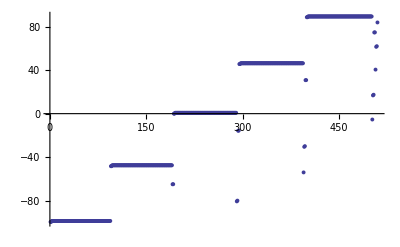

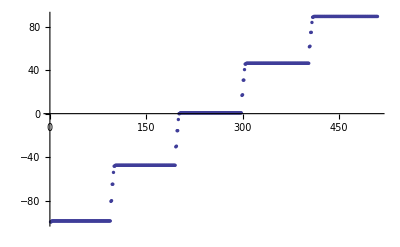

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

{50|3|7/2|1/2,50|3|5/2|1/2,50|4|7/2|1/2,50|4|9/2|1/2,50|5|9/2|1/2,50|5|11/2|1/2,50|6|11/2|1/2,50|6|13/2|1/2,50|7|13/2|1/2,50|7|15/2|1/2,50|8|15/2|1/2,50|8|17/2|1/2,50|9|17/2|1/2,50|9|19/2|1/2,50|10|19/2|1/2,50|10|21/2|1/2,50|11|21/2|1/2,50|11|23/2|1/2,50|12|23/2|1/2,50|12|25/2|1/2,50|13|25/2|1/2,50|13|27/2|1/2,50|14|27/2|1/2,50|14|29/2|1/2,50|15|29/2|1/2,50|15|31/2|1/2,50|16|31/2|1/2,50|16|33/2|1/2,50|17|33/2|1/2,50|17|35/2|1/2,50|18|35/2|1/2,50|18|37/2|1/2,50|19|37/2|1/2,50|19|39/2|1/2,50|20|39/2|1/2,50|20|41/2|1/2,50|21|41/2|1/2,50|21|43/2|1/2,50|22|43/2|1/2,50|22|45/2|1/2,50|23|45/2|1/2,50|23|47/2|1/2,50|24|47/2|1/2,50|24|49/2|1/2,50|25|49/2|1/2,50|25|51/2|1/2,50|26|51/2|1/2,50|26|53/2|1/2,50|27|53/2|1/2,50|27|55/2|1/2,50|28|55/2|1/2,50|28|57/2|1/2,50|29|57/2|1/2,50|29|59/2|1/2,50|30|59/2|1/2,50|30|61/2|1/2,50|31|61/2|1/2,50|31|63/2|1/2,50|32|63/2|1/2,50|32|65/2|1/2,50|33|65/2|1/2,50|33|67/2|1/2,50|34|67/2|1/2,50|34|69/2|1/2,50|35|69/2|1/2,50|35|71/2|1/2,50|36|71/2|1/2,50|36|73/2|1/2,50|37|73/2|1/2,50|37|75/2|1/2,50|38|75/2|1/2,50|38|77/2|1/2,50|39|77/2|1/2,50|39|79/2|1/2,50|40|79/2|1/2,50|40|81/2|1/2,50|41|81/2|1/2,50|41|83/2|1/2,50|42|83/2|1/2,50|42|85/2|1/2,50|43|85/2|1/2,50|43|87/2|1/2,50|44|87/2|1/2,50|44|89/2|1/2,50|45|89/2|1/2,50|45|91/2|1/2,50|46|91/2|1/2,50|46|93/2|1/2,50|47|93/2|1/2,50|47|95/2|1/2,50|48|95/2|1/2,50|48|97/2|1/2,50|49|97/2|1/2,50|49|99/2|1/2,53|1|1/2|1/2,53|1|3/2|1/2,52|2|3/2|1/2,52|2|5/2|1/2,54|0|1/2|1/2,51|3|7/2|1/2,51|3|5/2|1/2,51|4|7/2|1/2,51|4|9/2|1/2,51|5|9/2|1/2,51|5|11/2|1/2,51|6|11/2|1/2,51|6|13/2|1/2,51|7|13/2|1/2,51|7|15/2|1/2,51|8|15/2|1/2,51|8|17/2|1/2,51|9|17/2|1/2,51|9|19/2|1/2,51|10|19/2|1/2,51|10|21/2|1/2,51|11|21/2|1/2,51|11|23/2|1/2,51|12|23/2|1/2,51|12|25/2|1/2,51|13|25/2|1/2,51|13|27/2|1/2,51|14|27/2|1/2,51|14|29/2|1/2,51|15|29/2|1/2,51|15|31/2|1/2,51|16|31/2|1/2,51|16|33/2|1/2,51|17|33/2|1/2,51|17|35/2|1/2,51|18|35/2|1/2,51|18|37/2|1/2,51|19|37/2|1/2,51|19|39/2|1/2,51|20|39/2|1/2,51|20|41/2|1/2,51|21|41/2|1/2,51|21|43/2|1/2,51|22|43/2|1/2,51|22|45/2|1/2,51|23|45/2|1/2,51|23|47/2|1/2,51|24|47/2|1/2,51|24|49/2|1/2,51|25|49/2|1/2,51|25|51/2|1/2,51|26|51/2|1/2,51|26|53/2|1/2,51|27|53/2|1/2,51|27|55/2|1/2,51|28|55/2|1/2,51|28|57/2|1/2,51|29|57/2|1/2,51|29|59/2|1/2,51|30|59/2|1/2,51|30|61/2|1/2,51|31|61/2|1/2,51|31|63/2|1/2,51|32|63/2|1/2,51|32|65/2|1/2,51|33|65/2|1/2,51|33|67/2|1/2,51|34|67/2|1/2,51|34|69/2|1/2,51|35|69/2|1/2,51|35|71/2|1/2,51|36|71/2|1/2,51|36|73/2|1/2,51|37|73/2|1/2,51|37|75/2|1/2,51|38|75/2|1/2,51|38|77/2|1/2,51|39|77/2|1/2,51|39|79/2|1/2,51|40|79/2|1/2,51|40|81/2|1/2,51|41|81/2|1/2,51|41|83/2|1/2,51|42|83/2|1/2,51|42|85/2|1/2,51|43|85/2|1/2,51|43|87/2|1/2,51|44|87/2|1/2,51|44|89/2|1/2,51|45|89/2|1/2,51|45|91/2|1/2,51|46|91/2|1/2,51|46|93/2|1/2,51|47|93/2|1/2,51|47|95/2|1/2,51|48|95/2|1/2,51|48|97/2|1/2,51|49|97/2|1/2,51|49|99/2|1/2,51|50|99/2|1/2,51|50|101/2|1/2,54|1|1/2|1/2,54|1|3/2|1/2,53|2|3/2|1/2,53|2|5/2|1/2,55|0|1/2|1/2,52|3|7/2|1/2,52|3|5/2|1/2,52|4|7/2|1/2,52|4|9/2|1/2,52|5|9/2|1/2,52|5|11/2|1/2,52|6|11/2|1/2,52|6|13/2|1/2,52|7|13/2|1/2,52|7|15/2|1/2,52|8|15/2|1/2,52|8|17/2|1/2,52|9|17/2|1/2,52|9|19/2|1/2,52|10|19/2|1/2,52|10|21/2|1/2,52|11|21/2|1/2,52|11|23/2|1/2,52|12|23/2|1/2,52|12|25/2|1/2,52|13|25/2|1/2,52|13|27/2|1/2,52|14|27/2|1/2,52|14|29/2|1/2,52|15|29/2|1/2,52|15|31/2|1/2,52|16|31/2|1/2,52|16|33/2|1/2,52|17|33/2|1/2,52|17|35/2|1/2,52|18|35/2|1/2,52|18|37/2|1/2,52|19|37/2|1/2,52|19|39/2|1/2,52|20|39/2|1/2,52|20|41/2|1/2,52|21|41/2|1/2,52|21|43/2|1/2,52|22|43/2|1/2,52|22|45/2|1/2,52|23|45/2|1/2,52|23|47/2|1/2,52|24|47/2|1/2,52|24|49/2|1/2,52|25|49/2|1/2,52|25|51/2|1/2,52|26|51/2|1/2,52|26|53/2|1/2,52|27|53/2|1/2,52|27|55/2|1/2,52|28|55/2|1/2,52|28|57/2|1/2,52|29|57/2|1/2,52|29|59/2|1/2,52|30|59/2|1/2,52|30|61/2|1/2,52|31|61/2|1/2,52|31|63/2|1/2,52|32|63/2|1/2,52|32|65/2|1/2,52|33|65/2|1/2,52|33|67/2|1/2,52|34|67/2|1/2,52|34|69/2|1/2,52|35|69/2|1/2,52|35|71/2|1/2,52|36|71/2|1/2,52|36|73/2|1/2,52|37|73/2|1/2,52|37|75/2|1/2,52|38|75/2|1/2,52|38|77/2|1/2,52|39|77/2|1/2,52|39|79/2|1/2,52|40|79/2|1/2,52|40|81/2|1/2,52|41|81/2|1/2,52|41|83/2|1/2,52|42|83/2|1/2,52|42|85/2|1/2,52|43|85/2|1/2,52|43|87/2|1/2,52|44|87/2|1/2,52|44|89/2|1/2,52|45|89/2|1/2,52|45|91/2|1/2,52|46|91/2|1/2,52|46|93/2|1/2,52|47|93/2|1/2,52|47|95/2|1/2,52|48|95/2|1/2,52|48|97/2|1/2,52|49|97/2|1/2,52|49|99/2|1/2,52|50|99/2|1/2,52|50|101/2|1/2,52|51|101/2|1/2,52|51|103/2|1/2,55|1|1/2|1/2,55|1|3/2|1/2,54|2|3/2|1/2,54|2|5/2|1/2,56|0|1/2|1/2,53|3|7/2|1/2,53|3|5/2|1/2,53|4|7/2|1/2,53|4|9/2|1/2,53|5|9/2|1/2,53|5|11/2|1/2,53|6|11/2|1/2,53|6|13/2|1/2,53|7|13/2|1/2,53|7|15/2|1/2,53|8|15/2|1/2,53|8|17/2|1/2,53|9|17/2|1/2,53|9|19/2|1/2,53|10|19/2|1/2,53|10|21/2|1/2,53|11|21/2|1/2,53|11|23/2|1/2,53|12|23/2|1/2,53|12|25/2|1/2,53|13|25/2|1/2,53|13|27/2|1/2,53|14|27/2|1/2,53|14|29/2|1/2,53|15|29/2|1/2,53|15|31/2|1/2,53|16|31/2|1/2,53|16|33/2|1/2,53|17|33/2|1/2,53|17|35/2|1/2,53|18|35/2|1/2,53|18|37/2|1/2,53|19|37/2|1/2,53|19|39/2|1/2,53|20|39/2|1/2,53|20|41/2|1/2,53|21|41/2|1/2,53|21|43/2|1/2,53|22|43/2|1/2,53|22|45/2|1/2,53|23|45/2|1/2,53|23|47/2|1/2,53|24|47/2|1/2,53|24|49/2|1/2,53|25|49/2|1/2,53|25|51/2|1/2,53|26|51/2|1/2,53|26|53/2|1/2,53|27|53/2|1/2,53|27|55/2|1/2,53|28|55/2|1/2,53|28|57/2|1/2,53|29|57/2|1/2,53|29|59/2|1/2,53|30|59/2|1/2,53|30|61/2|1/2,53|31|61/2|1/2,53|31|63/2|1/2,53|32|63/2|1/2,53|32|65/2|1/2,53|33|65/2|1/2,53|33|67/2|1/2,53|34|67/2|1/2,53|34|69/2|1/2,53|35|69/2|1/2,53|35|71/2|1/2,53|36|71/2|1/2,53|36|73/2|1/2,53|37|73/2|1/2,53|37|75/2|1/2,53|38|75/2|1/2,53|38|77/2|1/2,53|39|77/2|1/2,53|39|79/2|1/2,53|40|79/2|1/2,53|40|81/2|1/2,53|41|81/2|1/2,53|41|83/2|1/2,53|42|83/2|1/2,53|42|85/2|1/2,53|43|85/2|1/2,53|43|87/2|1/2,53|44|87/2|1/2,53|44|89/2|1/2,53|45|89/2|1/2,53|45|91/2|1/2,53|46|91/2|1/2,53|46|93/2|1/2,53|47|93/2|1/2,53|47|95/2|1/2,53|48|95/2|1/2,53|48|97/2|1/2,53|49|97/2|1/2,53|49|99/2|1/2,53|50|99/2|1/2,53|50|101/2|1/2,53|51|101/2|1/2,53|51|103/2|1/2,53|52|103/2|1/2,53|52|105/2|1/2,56|1|1/2|1/2,56|1|3/2|1/2,55|2|3/2|1/2,55|2|5/2|1/2,57|0|1/2|1/2,54|3|7/2|1/2,54|3|5/2|1/2,54|4|7/2|1/2,54|4|9/2|1/2,54|5|9/2|1/2,54|5|11/2|1/2,54|6|11/2|1/2,54|6|13/2|1/2,54|7|13/2|1/2,54|7|15/2|1/2,54|8|15/2|1/2,54|8|17/2|1/2,54|9|17/2|1/2,54|9|19/2|1/2,54|10|19/2|1/2,54|10|21/2|1/2,54|11|21/2|1/2,54|11|23/2|1/2,54|12|23/2|1/2,54|12|25/2|1/2,54|13|25/2|1/2,54|13|27/2|1/2,54|14|27/2|1/2,54|14|29/2|1/2,54|15|29/2|1/2,54|15|31/2|1/2,54|16|31/2|1/2,54|16|33/2|1/2,54|17|33/2|1/2,54|17|35/2|1/2,54|18|35/2|1/2,54|18|37/2|1/2,54|19|37/2|1/2,54|19|39/2|1/2,54|20|39/2|1/2,54|20|41/2|1/2,54|21|41/2|1/2,54|21|43/2|1/2,54|22|43/2|1/2,54|22|45/2|1/2,54|23|45/2|1/2,54|23|47/2|1/2,54|24|47/2|1/2,54|24|49/2|1/2,54|25|49/2|1/2,54|25|51/2|1/2,54|26|51/2|1/2,54|26|53/2|1/2,54|27|53/2|1/2,54|27|55/2|1/2,54|28|55/2|1/2,54|28|57/2|1/2,54|29|57/2|1/2,54|29|59/2|1/2,54|30|59/2|1/2,54|30|61/2|1/2,54|31|61/2|1/2,54|31|63/2|1/2,54|32|63/2|1/2,54|32|65/2|1/2,54|33|65/2|1/2,54|33|67/2|1/2,54|34|67/2|1/2,54|34|69/2|1/2,54|35|69/2|1/2,54|35|71/2|1/2,54|36|71/2|1/2,54|36|73/2|1/2,54|37|73/2|1/2,54|37|75/2|1/2,54|38|75/2|1/2,54|38|77/2|1/2,54|39|77/2|1/2,54|39|79/2|1/2,54|40|79/2|1/2,54|40|81/2|1/2,54|41|81/2|1/2,54|41|83/2|1/2,54|42|83/2|1/2,54|42|85/2|1/2,54|43|85/2|1/2,54|43|87/2|1/2,54|44|87/2|1/2,54|44|89/2|1/2,54|45|89/2|1/2,54|45|91/2|1/2,54|46|91/2|1/2,54|46|93/2|1/2,54|47|93/2|1/2,54|47|95/2|1/2,54|48|95/2|1/2,54|48|97/2|1/2,54|49|97/2|1/2,54|49|99/2|1/2,54|50|99/2|1/2,54|50|101/2|1/2,54|51|101/2|1/2,54|51|103/2|1/2,54|52|103/2|1/2,54|52|105/2|1/2,54|53|105/2|1/2,54|53|107/2|1/2}

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, 0}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{4.28091,0.-4.28091 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{40.435,Null}

{0,0,0}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.3168×10^12,-1.3168×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.31593×10^12,-1.26565×10^12,-1.26565×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.26483×10^12,-1.28226×10^12,-1.28218×10^12,-1.21742×10^12,-1.21742×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.29795×10^12,-1.29727×10^12,-1.23309×10^12,-1.23301×10^12,-1.1719×10^12,-1.1719×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.27136×10^12,-1.24789×10^12,-1.24725×10^12,-1.1867×10^12,-1.18662×10^12,-1.12889×10^12,-1.12889×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.22281×10^12,-1.20066×10^12,-1.20006×10^12,-1.14287×10^12,-1.1428×10^12,-1.17699×10^12,-1.15607×10^12,-1.1555×10^12,-1.1337×10^12}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-1316.8,-1316.8,-1315.97,-1315.97,-1315.97,-1315.97,-1315.97,-1315.97,-1315.97,-1315.97,-1315.97,-1315.97,-1315.96,-1315.96,-1315.96,-1315.96,-1315.96,-1315.96,-1315.96,-1315.96,-1315.96,-1315.96,-1315.95,-1315.95,-1315.95,-1315.95,-1315.95,-1315.95,-1315.95,-1315.95,-1315.95,-1315.95,-1315.94,-1315.94,-1315.94,-1315.94,-1315.94,-1315.94,-1315.94,-1315.94,-1315.94,-1315.94,-1315.93,-1315.93,-1315.93,-1315.93,-1315.93,-1315.93,-1315.93,-1315.93,-1315.93,-1315.93,-1315.92,-1315.92,-1315.92,-1315.92,-1315.92,-1315.92,-1315.92,-1315.92,-1315.92,-1315.92,-1315.91,-1315.91,-1315.91,-1315.91,-1315.91,-1315.91,-1315.91,-1315.91,-1315.91,-1315.91,-1315.9,-1315.9,-1315.9,-1315.9,-1315.9,-1315.9,-1315.9,-1315.9,-1315.9,-1315.9,-1315.89,-1315.89,-1315.89,-1315.89,-1315.89,-1315.89,-1315.89,-1315.89,-1315.88,-1315.88,-1315.88,-1315.88,-1297.95,-1297.27,-1282.26,-1282.18,-1271.36,-1265.65,-1265.65,-1264.88,-1264.88,-1264.87,-1264.87,-1264.87,-1264.87,-1264.87,-1264.87,-1264.87,-1264.87,-1264.87,-1264.87,-1264.86,-1264.86,-1264.86,-1264.86,-1264.86,-1264.86,-1264.86,-1264.86,-1264.86,-1264.86,-1264.85,-1264.85,-1264.85,-1264.85,-1264.85,-1264.85,-1264.85,-1264.85,-1264.85,-1264.85,-1264.84,-1264.84,-1264.84,-1264.84,-1264.84,-1264.84,-1264.84,-1264.84,-1264.84,-1264.84,-1264.83,-1264.83,-1264.83,-1264.83,-1264.83,-1264.83,-1264.83,-1264.83,-1264.83,-1264.83,-1264.82,-1264.82,-1264.82,-1264.82,-1264.82,-1264.82,-1264.82,-1264.82,-1264.82,-1264.82,-1264.81,-1264.81,-1264.81,-1264.81,-1264.81,-1264.81,-1264.81,-1264.81,-1264.8,-1264.8,-1264.8,-1264.8,-1264.8,-1264.8,-1264.8,-1264.8,-1264.8,-1264.8,-1264.79,-1264.79,-1264.79,-1264.79,-1264.79,-1264.79,-1264.79,-1264.79,-1264.79,-1264.79,-1264.78,-1264.78,-1264.78,-1264.78,-1247.89,-1247.25,-1233.09,-1233.01,-1222.81,-1217.42,-1217.42,-1216.7,-1216.7,-1216.7,-1216.7,-1216.7,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.65,-1216.65,-1216.65,-1216.65,-1216.65,-1216.65,-1216.65,-1216.65,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.61,-1216.61,-1216.61,-1216.61,-1216.61,-1216.61,-1216.61,-1216.61,-1216.6,-1216.6,-1216.6,-1216.6,-1216.6,-1216.6,-1200.66,-1200.06,-1186.7,-1186.62,-1176.99,-1171.9,-1171.9,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.12,-1171.12,-1171.12,-1171.12,-1171.12,-1171.12,-1156.07,-1155.5,-1142.87,-1142.8,-1133.7,-1128.89,-1128.89,-1128.25,-1128.25,-1128.25,-1128.25,-1128.25,-1128.25,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.14,-1128.14}

{{300,-112.589,50|3|7/2|1/2},{300,-112.488,50|3|5/2|1/2},{300,-111.954,50|4|7/2|1/2},{300,-111.878,50|4|9/2|1/2},{300,-111.335,50|5|9/2|1/2},{300,-111.272,50|5|11/2|1/2},{300,-110.724,50|6|11/2|1/2},{300,-110.67,50|6|13/2|1/2},{300,-110.117,50|7|13/2|1/2},{300,-110.07,50|7|15/2|1/2},{300,-109.513,50|8|15/2|1/2},{300,-109.471,50|8|17/2|1/2},{300,-108.911,50|9|17/2|1/2},{300,-108.874,50|9|19/2|1/2},{300,-108.311,50|10|19/2|1/2},{300,-108.278,50|10|21/2|1/2},{300,-107.712,50|11|21/2|1/2},{300,-107.682,50|11|23/2|1/2},{300,-107.114,50|12|23/2|1/2},{300,-107.087,50|12|25/2|1/2},{300,-106.517,50|13|25/2|1/2},{300,-106.492,50|13|27/2|1/2},{300,-105.92,50|14|27/2|1/2},{300,-105.898,50|14|29/2|1/2},{300,-105.324,50|15|29/2|1/2},{300,-105.304,50|15|31/2|1/2},{300,-104.728,50|16|31/2|1/2},{300,-104.711,50|16|33/2|1/2},{300,-104.133,50|17|33/2|1/2},{300,-104.117,50|17|35/2|1/2},{300,-103.538,50|18|35/2|1/2},{300,-103.524,50|18|37/2|1/2},{300,-102.943,50|19|37/2|1/2},{300,-102.931,50|19|39/2|1/2},{300,-102.348,50|20|39/2|1/2},{300,-102.338,50|20|41/2|1/2},{300,-101.754,50|21|41/2|1/2},{300,-101.745,50|21|43/2|1/2},{300,-101.159,50|22|43/2|1/2},{300,-101.152,50|22|45/2|1/2},{300,-100.564,50|23|45/2|1/2},{300,-100.559,50|23|47/2|1/2},{300,-99.9696,50|24|47/2|1/2},{300,-99.9655,50|24|49/2|1/2},{300,-99.3746,50|25|49/2|1/2},{300,-99.372,50|25|51/2|1/2},{300,-98.7795,50|26|51/2|1/2},{300,-98.7783,50|26|53/2|1/2},{300,-98.1845,50|27|53/2|1/2},{300,-98.1842,50|27|55/2|1/2},{300,-97.5905,50|28|55/2|1/2},{300,-97.5888,50|28|57/2|1/2},{300,-96.9963,50|29|57/2|1/2},{300,-96.9932,50|29|59/2|1/2},{300,-96.402,50|30|59/2|1/2},{300,-96.3974,50|30|61/2|1/2},{300,-95.8074,50|31|61/2|1/2},{300,-95.8014,50|31|63/2|1/2},{300,-95.2126,50|32|63/2|1/2},{300,-95.2051,50|32|65/2|1/2},{300,-94.6175,50|33|65/2|1/2},{300,-94.6084,50|33|67/2|1/2},{300,-94.0219,50|34|67/2|1/2},{300,-94.0113,50|34|69/2|1/2},{300,-93.426,50|35|69/2|1/2},{300,-93.4137,50|35|71/2|1/2},{300,-92.8295,50|36|71/2|1/2},{300,-92.8156,50|36|73/2|1/2},{300,-92.2326,50|37|73/2|1/2},{300,-92.2168,50|37|75/2|1/2},{300,-91.6351,50|38|75/2|1/2},{300,-91.6174,50|38|77/2|1/2},{300,-91.0369,50|39|77/2|1/2},{300,-91.0172,50|39|79/2|1/2},{300,-90.438,50|40|79/2|1/2},{300,-90.416,50|40|81/2|1/2},{300,-89.8382,50|41|81/2|1/2},{300,-89.8138,50|41|83/2|1/2},{300,-89.2374,50|42|83/2|1/2},{300,-89.2103,50|42|85/2|1/2},{300,-88.6355,50|43|85/2|1/2},{300,-88.6053,50|43|87/2|1/2},{300,-88.0321,50|44|87/2|1/2},{300,-87.9983,50|44|89/2|1/2},{300,-87.427,50|45|89/2|1/2},{300,-87.3889,50|45|91/2|1/2},{300,-86.8197,50|46|91/2|1/2},{300,-86.7762,50|46|93/2|1/2},{300,-86.2092,50|47|93/2|1/2},{300,-86.1585,50|47|95/2|1/2},{300,-85.5942,50|48|95/2|1/2},{300,-85.5325,50|48|97/2|1/2},{300,-84.9712,50|49|97/2|1/2},{300,-84.8888,50|49|99/2|1/2},{300,-83.9738,53|1|1/2|1/2},{300,-82.3321,53|1|3/2|1/2},{300,-65.5043,52|2|3/2|1/2},{300,-65.3552,52|2|5/2|1/2},{300,-61.8326,54|0|1/2|1/2},{300,-61.755,51|3|7/2|1/2},{300,-61.1691,51|3|5/2|1/2},{300,-61.1133,51|4|7/2|1/2},{300,-60.5293,51|4|9/2|1/2},{300,-60.4844,51|5|9/2|1/2},{300,-59.9003,51|5|11/2|1/2},{300,-59.8625,51|6|11/2|1/2},{300,-59.2776,51|6|13/2|1/2},{300,-59.2451,51|7|13/2|1/2},{300,-58.6593,51|7|15/2|1/2},{300,-58.6307,51|8|15/2|1/2},{300,-58.0439,51|8|17/2|1/2},{300,-58.0186,51|9|17/2|1/2},{300,-57.4309,51|9|19/2|1/2},{300,-57.4083,51|10|19/2|1/2},{300,-56.8196,51|10|21/2|1/2},{300,-56.7993,51|11|21/2|1/2},{300,-56.21,51|11|23/2|1/2},{300,-56.1914,51|12|23/2|1/2},{300,-55.602,51|12|25/2|1/2},{300,-55.5843,51|13|25/2|1/2},{300,-54.9975,51|13|27/2|1/2},{300,-54.978,51|14|27/2|1/2},{300,-54.4897,51|14|29/2|1/2},{300,-54.3725,51|15|29/2|1/2},{300,-54.3477,51|15|31/2|1/2},{300,-53.7706,51|16|31/2|1/2},{300,-53.7667,51|16|33/2|1/2},{300,-53.1666,51|17|33/2|1/2},{300,-53.162,51|17|35/2|1/2},{300,-52.5615,51|18|35/2|1/2},{300,-52.5575,51|18|37/2|1/2},{300,-51.9563,51|19|37/2|1/2},{300,-51.9533,51|19|39/2|1/2},{300,-51.3512,51|20|39/2|1/2},{300,-51.3492,51|20|41/2|1/2},{300,-50.7464,51|21|41/2|1/2},{300,-50.7452,51|21|43/2|1/2},{300,-50.1422,51|22|43/2|1/2},{300,-50.1408,51|22|45/2|1/2},{300,-49.5384,51|23|45/2|1/2},{300,-49.5362,51|23|47/2|1/2},{300,-48.9348,51|24|47/2|1/2},{300,-48.9314,51|24|49/2|1/2},{300,-48.3311,51|25|49/2|1/2},{300,-48.3265,51|25|51/2|1/2},{300,-47.7275,51|26|51/2|1/2},{300,-47.7217,51|26|53/2|1/2},{300,-47.1238,51|27|53/2|1/2},{300,-47.1168,51|27|55/2|1/2},{300,-46.5201,51|28|55/2|1/2},{300,-46.5118,51|28|57/2|1/2},{300,-45.9165,51|29|57/2|1/2},{300,-45.9069,51|29|59/2|1/2},{300,-45.3128,51|30|59/2|1/2},{300,-45.3019,51|30|61/2|1/2},{300,-44.7091,51|31|61/2|1/2},{300,-44.6969,51|31|63/2|1/2},{300,-44.1053,51|32|63/2|1/2},{300,-44.0917,51|32|65/2|1/2},{300,-43.5013,51|33|65/2|1/2},{300,-43.4863,51|33|67/2|1/2},{300,-42.8971,51|34|67/2|1/2},{300,-42.8807,51|34|69/2|1/2},{300,-42.2926,51|35|69/2|1/2},{300,-42.2747,51|35|71/2|1/2},{300,-41.6879,51|36|71/2|1/2},{300,-41.6684,51|36|73/2|1/2},{300,-41.0827,51|37|73/2|1/2},{300,-41.0615,51|37|75/2|1/2},{300,-40.4772,51|38|75/2|1/2},{300,-40.4542,51|38|77/2|1/2},{300,-39.8711,51|39|77/2|1/2},{300,-39.8462,51|39|79/2|1/2},{300,-39.2644,51|40|79/2|1/2},{300,-39.2374,51|40|81/2|1/2},{300,-38.6571,51|41|81/2|1/2},{300,-38.6278,51|41|83/2|1/2},{300,-38.049,51|42|83/2|1/2},{300,-38.0171,51|42|85/2|1/2},{300,-37.4399,51|43|85/2|1/2},{300,-37.4051,51|43|87/2|1/2},{300,-36.8297,51|44|87/2|1/2},{300,-36.7916,51|44|89/2|1/2},{300,-36.2181,51|45|89/2|1/2},{300,-36.1762,51|45|91/2|1/2},{300,-35.6049,51|46|91/2|1/2},{300,-35.5582,51|46|93/2|1/2},{300,-34.9896,51|47|93/2|1/2},{300,-34.9369,51|47|95/2|1/2},{300,-34.3714,51|48|95/2|1/2},{300,-34.3107,51|48|97/2|1/2},{300,-33.7492,51|49|97/2|1/2},{300,-33.6765,51|49|99/2|1/2},{300,-33.1204,51|50|99/2|1/2},{300,-33.0258,51|50|101/2|1/2},{300,-32.5825,54|1|1/2|1/2},{300,-32.1919,54|1|3/2|1/2},{300,-16.462,53|2|3/2|1/2},{300,-16.312,53|2|5/2|1/2},{300,-14.1953,55|0|1/2|1/2},{300,-14.1265,52|3|7/2|1/2},{300,-13.5189,52|3|5/2|1/2},{300,-13.4699,52|4|7/2|1/2},{300,-12.8682,52|4|9/2|1/2},{300,-12.8288,52|5|9/2|1/2},{300,-12.229,52|5|11/2|1/2},{300,-12.1957,52|6|11/2|1/2},{300,-11.5963,52|6|13/2|1/2},{300,-11.5674,52|7|13/2|1/2},{300,-10.968,52|7|15/2|1/2},{300,-10.9424,52|8|15/2|1/2},{300,-10.3427,52|8|17/2|1/2},{300,-10.3198,52|9|17/2|1/2},{300,-9.71962,52|9|19/2|1/2},{300,-9.69903,52|10|19/2|1/2},{300,-9.09835,52|10|21/2|1/2},{300,-9.07961,52|11|21/2|1/2},{300,-8.47856,52|11|23/2|1/2},{300,-8.4613,52|12|23/2|1/2},{300,-7.86016,52|12|25/2|1/2},{300,-7.84388,52|13|25/2|1/2},{300,-7.24341,52|13|27/2|1/2},{300,-7.22719,52|14|27/2|1/2},{300,-6.63018,52|14|29/2|1/2},{300,-6.61111,52|15|29/2|1/2},{300,-6.05091,52|15|31/2|1/2},{300,-5.99555,52|16|31/2|1/2},{300,-5.8617,52|16|33/2|1/2},{300,-5.3805,52|17|33/2|1/2},{300,-5.37263,52|17|35/2|1/2},{300,-4.7659,52|18|35/2|1/2},{300,-4.76323,52|18|37/2|1/2},{300,-4.15134,52|19|37/2|1/2},{300,-4.14935,52|19|39/2|1/2},{300,-3.53671,52|20|39/2|1/2},{300,-3.53483,52|20|41/2|1/2},{300,-2.92221,52|21|41/2|1/2},{300,-2.92007,52|21|43/2|1/2},{300,-2.30789,52|22|43/2|1/2},{300,-2.30514,52|22|45/2|1/2},{300,-1.69366,52|23|45/2|1/2},{300,-1.69008,52|23|47/2|1/2},{300,-1.07944,52|24|47/2|1/2},{300,-1.07492,52|24|49/2|1/2},{300,-0.465171,52|25|49/2|1/2},{300,-0.459621,52|25|51/2|1/2},{300,0.149189,52|26|51/2|1/2},{300,0.155814,52|26|53/2|1/2},{300,0.763649,52|27|53/2|1/2},{300,0.771385,52|27|55/2|1/2},{300,1.37819,52|28|55/2|1/2},{300,1.38707,52|28|57/2|1/2},{300,1.99281,52|29|57/2|1/2},{300,2.00287,52|29|59/2|1/2},{300,2.60751,52|30|59/2|1/2},{300,2.61877,52|30|61/2|1/2},{300,3.22231,52|31|61/2|1/2},{300,3.23481,52|31|63/2|1/2},{300,3.83727,52|32|63/2|1/2},{300,3.85105,52|32|65/2|1/2},{300,4.45243,52|33|65/2|1/2},{300,4.46754,52|33|67/2|1/2},{300,5.06785,52|34|67/2|1/2},{300,5.08433,52|34|69/2|1/2},{300,5.68357,52|35|69/2|1/2},{300,5.70149,52|35|71/2|1/2},{300,6.29964,52|36|71/2|1/2},{300,6.31905,52|36|73/2|1/2},{300,6.91608,52|37|73/2|1/2},{300,6.93708,52|37|75/2|1/2},{300,7.53296,52|38|75/2|1/2},{300,7.55564,52|38|77/2|1/2},{300,8.15031,52|39|77/2|1/2},{300,8.17478,52|39|79/2|1/2},{300,8.76819,52|40|79/2|1/2},{300,8.79459,52|40|81/2|1/2},{300,9.38667,52|41|81/2|1/2},{300,9.41517,52|41|83/2|1/2},{300,10.0058,52|42|83/2|1/2},{300,10.0366,52|42|85/2|1/2},{300,10.6257,52|43|85/2|1/2},{300,10.6591,52|43|87/2|1/2},{300,11.2465,52|44|87/2|1/2},{300,11.2827,52|44|89/2|1/2},{300,11.8683,52|45|89/2|1/2},{300,11.9077,52|45|91/2|1/2},{300,12.4912,52|46|91/2|1/2},{300,12.5344,52|46|93/2|1/2},{300,13.1153,52|47|93/2|1/2},{300,13.1628,52|47|95/2|1/2},{300,13.7399,52|48|95/2|1/2},{300,13.7917,52|48|97/2|1/2},{300,14.3277,52|49|97/2|1/2},{300,14.3832,52|49|99/2|1/2},{300,14.487,52|50|99/2|1/2},{300,14.7392,52|50|101/2|1/2},{300,15.022,52|51|101/2|1/2},{300,15.0999,52|51|103/2|1/2},{300,15.6544,55|1|1/2|1/2},{300,15.757,55|1|3/2|1/2},{300,29.5284,54|2|3/2|1/2},{300,29.6393,54|2|5/2|1/2},{300,30.7572,56|0|1/2|1/2},{300,30.8108,53|3|7/2|1/2},{300,31.4386,53|3|5/2|1/2},{300,31.4779,53|4|7/2|1/2},{300,32.095,53|4|9/2|1/2},{300,32.1274,53|5|9/2|1/2},{300,32.7409,53|5|11/2|1/2},{300,32.7689,53|6|11/2|1/2},{300,33.3811,53|6|13/2|1/2},{300,33.4058,53|7|13/2|1/2},{300,34.0175,53|7|15/2|1/2},{300,34.0397,53|8|15/2|1/2},{300,34.6513,53|8|17/2|1/2},{300,34.6715,53|9|17/2|1/2},{300,35.2832,53|9|19/2|1/2},{300,35.3016,53|10|19/2|1/2},{300,35.9136,53|10|21/2|1/2},{300,35.9306,53|11|21/2|1/2},{300,36.5428,53|11|23/2|1/2},{300,36.5586,53|12|23/2|1/2},{300,37.1709,53|12|25/2|1/2},{300,37.1859,53|13|25/2|1/2},{300,37.7978,53|13|27/2|1/2},{300,37.8125,53|14|27/2|1/2},{300,38.4231,53|14|29/2|1/2},{300,38.4388,53|15|29/2|1/2},{300,39.0443,53|15|31/2|1/2},{300,39.0646,53|16|31/2|1/2},{300,39.6318,53|16|33/2|1/2},{300,39.6901,53|17|33/2|1/2},{300,39.8724,53|17|35/2|1/2},{300,40.3155,53|18|35/2|1/2},{300,40.3336,53|18|37/2|1/2},{300,40.9407,53|19|37/2|1/2},{300,40.9483,53|19|39/2|1/2},{300,41.5659,53|20|39/2|1/2},{300,41.5712,53|20|41/2|1/2},{300,42.1912,53|21|41/2|1/2},{300,42.1959,53|21|43/2|1/2},{300,42.8165,53|22|43/2|1/2},{300,42.8213,53|22|45/2|1/2},{300,43.4418,53|23|45/2|1/2},{300,43.4471,53|23|47/2|1/2},{300,44.0673,53|24|47/2|1/2},{300,44.0733,53|24|49/2|1/2},{300,44.6929,53|25|49/2|1/2},{300,44.6998,53|25|51/2|1/2},{300,45.3188,53|26|51/2|1/2},{300,45.3265,53|26|53/2|1/2},{300,45.9449,53|27|53/2|1/2},{300,45.9535,53|27|55/2|1/2},{300,46.5711,53|28|55/2|1/2},{300,46.5808,53|28|57/2|1/2},{300,47.1976,53|29|57/2|1/2},{300,47.2083,53|29|59/2|1/2},{300,47.8241,53|30|59/2|1/2},{300,47.836,53|30|61/2|1/2},{300,48.4509,53|31|61/2|1/2},{300,48.4639,53|31|63/2|1/2},{300,49.0778,53|32|63/2|1/2},{300,49.092,53|32|65/2|1/2},{300,49.7049,53|33|65/2|1/2},{300,49.7204,53|33|67/2|1/2},{300,50.3322,53|34|67/2|1/2},{300,50.349,53|34|69/2|1/2},{300,50.9599,53|35|69/2|1/2},{300,50.9781,53|35|71/2|1/2},{300,51.5878,53|36|71/2|1/2},{300,51.6075,53|36|73/2|1/2},{300,52.2161,53|37|73/2|1/2},{300,52.2373,53|37|75/2|1/2},{300,52.8448,53|38|75/2|1/2},{300,52.8675,53|38|77/2|1/2},{300,53.4738,53|39|77/2|1/2},{300,53.4983,53|39|79/2|1/2},{300,54.1033,53|40|79/2|1/2},{300,54.1296,53|40|81/2|1/2},{300,54.7332,53|41|81/2|1/2},{300,54.7615,53|41|83/2|1/2},{300,55.3636,53|42|83/2|1/2},{300,55.3941,53|42|85/2|1/2},{300,55.9945,53|43|85/2|1/2},{300,56.0274,53|43|87/2|1/2},{300,56.6259,53|44|87/2|1/2},{300,56.6615,53|44|89/2|1/2},{300,57.2576,53|45|89/2|1/2},{300,57.2964,53|45|91/2|1/2},{300,57.8889,53|46|91/2|1/2},{300,57.9318,53|46|93/2|1/2},{300,58.513,53|47|93/2|1/2},{300,58.5648,53|47|95/2|1/2},{300,58.8951,53|48|95/2|1/2},{300,59.1495,53|48|97/2|1/2},{300,59.2042,53|49|97/2|1/2},{300,59.3489,53|49|99/2|1/2},{300,59.8163,53|50|99/2|1/2},{300,59.878,53|50|101/2|1/2},{300,60.4537,53|51|101/2|1/2},{300,60.5212,53|51|103/2|1/2},{300,61.0974,53|52|103/2|1/2},{300,61.1775,53|52|105/2|1/2},{300,61.7485,56|1|1/2|1/2},{300,61.8534,56|1|3/2|1/2},{300,72.9524,55|2|3/2|1/2},{300,73.1541,55|2|5/2|1/2},{300,73.6295,57|0|1/2|1/2},{300,73.712,54|3|7/2|1/2},{300,74.2829,54|3|5/2|1/2},{300,74.3372,54|4|7/2|1/2},{300,74.931,54|4|9/2|1/2},{300,74.974,54|5|9/2|1/2},{300,75.5766,54|5|11/2|1/2},{300,75.6135,54|6|11/2|1/2},{300,76.2207,54|6|13/2|1/2},{300,76.2536,54|7|13/2|1/2},{300,76.8638,54|7|15/2|1/2},{300,76.8937,54|8|15/2|1/2},{300,77.5059,54|8|17/2|1/2},{300,77.5335,54|9|17/2|1/2},{300,78.1473,54|9|19/2|1/2},{300,78.1731,54|10|19/2|1/2},{300,78.788,54|10|21/2|1/2},{300,78.8123,54|11|21/2|1/2},{300,79.4282,54|11|23/2|1/2},{300,79.4512,54|12|23/2|1/2},{300,80.0677,54|12|25/2|1/2},{300,80.0897,54|13|25/2|1/2},{300,80.7067,54|13|27/2|1/2},{300,80.728,54|14|27/2|1/2},{300,81.3451,54|14|29/2|1/2},{300,81.3659,54|15|29/2|1/2},{300,81.9828,54|15|31/2|1/2},{300,82.0036,54|16|31/2|1/2},{300,82.6197,54|16|33/2|1/2},{300,82.6411,54|17|33/2|1/2},{300,83.2554,54|17|35/2|1/2},{300,83.2783,54|18|35/2|1/2},{300,83.8893,54|18|37/2|1/2},{300,83.9153,54|19|37/2|1/2},{300,84.5196,54|19|39/2|1/2},{300,84.5521,54|20|39/2|1/2},{300,85.1405,54|20|41/2|1/2},{300,85.1887,54|21|41/2|1/2},{300,85.7243,54|21|43/2|1/2},{300,85.8252,54|22|43/2|1/2},{300,86.1523,54|22|45/2|1/2},{300,86.4616,54|23|45/2|1/2},{300,86.5687,54|23|47/2|1/2},{300,87.0978,54|24|47/2|1/2},{300,87.1472,54|24|49/2|1/2},{300,87.7341,54|25|49/2|1/2},{300,87.7667,54|25|51/2|1/2},{300,88.3703,54|26|51/2|1/2},{300,88.396,54|26|53/2|1/2},{300,89.0065,54|27|53/2|1/2},{300,89.0288,54|27|55/2|1/2},{300,89.6428,54|28|55/2|1/2},{300,89.6634,54|28|57/2|1/2},{300,90.279,54|29|57/2|1/2},{300,90.2988,54|29|59/2|1/2},{300,90.9151,54|30|59/2|1/2},{300,90.9347,54|30|61/2|1/2},{300,91.5512,54|31|61/2|1/2},{300,91.571,54|31|63/2|1/2},{300,92.1872,54|32|63/2|1/2},{300,92.2075,54|32|65/2|1/2},{300,92.8232,54|33|65/2|1/2},{300,92.8442,54|33|67/2|1/2},{300,93.4593,54|34|67/2|1/2},{300,93.4811,54|34|69/2|1/2},{300,94.0954,54|35|69/2|1/2},{300,94.1182,54|35|71/2|1/2},{300,94.7317,54|36|71/2|1/2},{300,94.7556,54|36|73/2|1/2},{300,95.3682,54|37|73/2|1/2},{300,95.3934,54|37|75/2|1/2},{300,96.0049,54|38|75/2|1/2},{300,96.0314,54|38|77/2|1/2},{300,96.6419,54|39|77/2|1/2},{300,96.6699,54|39|79/2|1/2},{300,97.2792,54|40|79/2|1/2},{300,97.3088,54|40|81/2|1/2},{300,97.9168,54|41|81/2|1/2},{300,97.9483,54|41|83/2|1/2},{300,98.5549,54|42|83/2|1/2},{300,98.5884,54|42|85/2|1/2},{300,99.1935,54|43|85/2|1/2},{300,99.2292,54|43|87/2|1/2},{300,99.8327,54|44|87/2|1/2},{300,99.8708,54|44|89/2|1/2},{300,100.473,54|45|89/2|1/2},{300,100.513,54|45|91/2|1/2},{300,101.113,54|46|91/2|1/2},{300,101.157,54|46|93/2|1/2},{300,101.755,54|47|93/2|1/2},{300,101.803,54|47|95/2|1/2},{300,102.398,54|48|95/2|1/2},{300,102.45,54|48|97/2|1/2},{300,103.042,54|49|97/2|1/2},{300,103.1,54|49|99/2|1/2},{300,103.689,54|50|99/2|1/2},{300,103.753,54|50|101/2|1/2},{300,104.337,54|51|101/2|1/2},{300,104.41,54|51|103/2|1/2},{300,104.989,54|52|103/2|1/2},{300,105.076,54|52|105/2|1/2},{300,105.647,54|53|105/2|1/2},{300,105.76,54|53|107/2|1/2}}

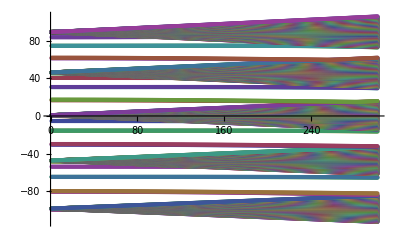

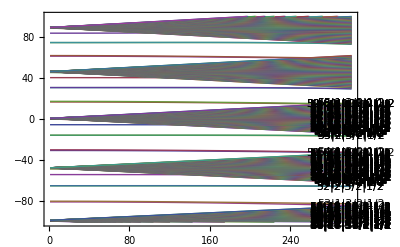

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

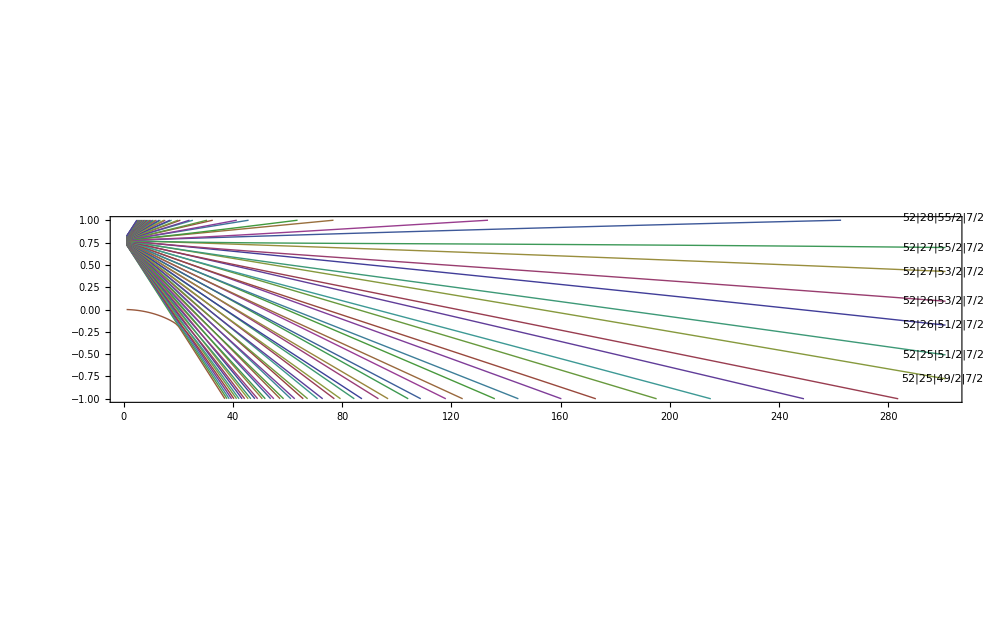

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
MPList
```

{{{1,-99.3757},{2,-99.3777},{3,-99.381},{4,-99.3856},{5,-99.3916},{6,-99.399},{7,-99.4077},{8,-99.4178},{9,-99.4292},{10,-99.442},{11,-99.4561},{12,-99.4716},{13,-99.4884},{14,-99.5065},{15,-99.526},{16,-99.5468},{17,-99.5689},«267»,{285,-111.875},{286,-111.923},{287,-111.97},{288,-112.018},{289,-112.065},{290,-112.113},{291,-112.161},{292,-112.208},{293,-112.256},{294,-112.303},{295,-112.351},{296,-112.399},{297,-112.446},{298,-112.494},{299,-112.541},{300,-112.589},{301,-112.637}},«508»,{«1»}}

```mathematica
While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_52f_1_2.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_52f_1_2.dat",Efieldlist]

Export["60p_j3_2_mj3_2_stark_Shift.dat",MPList[[218]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{{-99.3757,-99.3777,-99.381,-99.3856,-99.3916,-99.399,-99.4077,-99.4178,-99.4292,-99.442,-99.4561,-99.4716,-99.4884,-99.5065,-99.526,-99.5468,-99.5689,-99.5923,-99.617,-99.643,-99.6703,-99.6989,«258»,-111.685,-111.733,-111.78,-111.828,-111.875,-111.923,-111.97,-112.018,-112.065,-112.113,-112.161,-112.208,-112.256,-112.303,-112.351,-112.399,-112.446,-112.494,-112.541,-112.589,-112.637},«508»,{«1»}}

Stark_Shifts_around_52f_1_2.dat

Electric_fields_for_Stark_Shifts_around_52f_1_2.dat

60p_j3_2_mj3_2_stark_Shift.dat

```mathematica
LabelList[[112]]
LabelList[[113]]

MPList[[112]]

Export["59p1_2_stark_Shift.dat",MPList[[112]]] 
Export["59p3_2_stark_Shift.dat",MPList[[113]]]
```

59|1|1/2|1/2

59|1|3/2|1/2

{{1,-18.999},{2,-18.9992},{3,-18.9994},{4,-18.9998},{5,-19.0002},{6,-19.0008},{7,-19.0014},{8,-19.0022},{9,-19.003},{10,-19.004},{11,-19.005},{12,-19.0062},{13,-19.0074},{14,-19.0088},{15,-19.0102},{16,-19.0117},{17,-19.0134},{18,-19.0151},{19,-19.017},{20,-19.0189},{21,-19.021},{22,-19.0231},{23,-19.0253},{24,-19.0277},{25,-19.0301},{26,-19.0326},{27,-19.0353},{28,-19.038},{29,-19.0408},{30,-19.0438},{31,-19.0468},{32,-19.0499},{33,-19.0532},{34,-19.0565},{35,-19.0599},{36,-19.0634},{37,-19.067},{38,-19.0707},{39,-19.0746},{40,-19.0785},{41,-19.0825},{42,-19.0866},{43,-19.0908},{44,-19.0951},{45,-19.0995},{46,-19.104},{47,-19.1086},{48,-19.1133},{49,-19.118},{50,-19.1229},{51,-19.1279},{52,-19.133},{53,-19.1381},{54,-19.1434},{55,-19.1488},{56,-19.1542},{57,-19.1598},{58,-19.1654},{59,-19.1712},{60,-19.177},{61,-19.1829},{62,-19.189},{63,-19.1951},{64,-19.2013},{65,-19.2076},{66,-19.214},{67,-19.2205},{68,-19.2271},{69,-19.2338},{70,-19.2405},{71,-19.2474},{72,-19.2544},{73,-19.2614},{74,-19.2685},{75,-19.2758},{76,-19.2831},{77,-19.2905},{78,-19.298},{79,-19.3056},{80,-19.3133},{81,-19.3211},{82,-19.329},{83,-19.3369},{84,-19.345},{85,-19.3531},{86,-19.3613},{87,-19.3697},{88,-19.3781},{89,-19.3866},{90,-19.3951},{91,-19.4038},{92,-19.4126},{93,-19.4214},{94,-19.4303},{95,-19.4394},{96,-19.4485},{97,-19.4577},{98,-19.4669},{99,-19.4763},{100,-19.4857},{101,-19.4953},{102,-19.5049},{103,-19.5146},{104,-19.5243},{105,-19.5342},{106,-19.5441},{107,-19.5542},{108,-19.5643},{109,-19.5745},{110,-19.5847},{111,-19.5951},{112,-19.6055},{113,-19.616},{114,-19.6266},{115,-19.6373},{116,-19.648},{117,-19.6589},{118,-19.6698},{119,-19.6807},{120,-19.6918},{121,-19.7029},{122,-19.7141},{123,-19.7254},{124,-19.7368},{125,-19.7482},{126,-19.7597},{127,-19.7713},{128,-19.783},{129,-19.7947},{130,-19.8065},{131,-19.8184},{132,-19.8303},{133,-19.8423},{134,-19.8544},{135,-19.8665},{136,-19.8788},{137,-19.891},{138,-19.9034},{139,-19.9158},{140,-19.9283},{141,-19.9409},{142,-19.9535},{143,-19.9662},{144,-19.9789},{145,-19.9917},{146,-20.0046},{147,-20.0175},{148,-20.0305},{149,-20.0436},{150,-20.0567},{151,-20.0698},{152,-20.0831},{153,-20.0964},{154,-20.1097},{155,-20.1231},{156,-20.1366},{157,-20.1501},{158,-20.1636},{159,-20.1772},{160,-20.1909},{161,-20.2046},{162,-20.2184},{163,-20.2322},{164,-20.2461},{165,-20.26},{166,-20.2739},{167,-20.2879},{168,-20.3019},{169,-20.316},{170,-20.3301},{171,-20.3443},{172,-20.3585},{173,-20.3727},{174,-20.387},{175,-20.4012},{176,-20.4155},{177,-20.4299},{178,-20.4442},{179,-20.4586},{180,-20.473},{181,-20.4874},{182,-20.5017},{183,-20.5161},{184,-20.5304},{185,-20.5448},{186,-20.559},{187,-20.5732},{188,-20.5872},{189,-20.601},{190,-20.6146},{191,-20.6275},{192,-20.6395},{193,-20.649},{194,-20.6514},{195,-20.6326},{196,-20.5911},{197,-20.5428},{198,-20.4972},{199,-20.466},{200,-20.4319},{201,-20.3832},{202,-20.3301},{203,-20.2757},{204,-20.2208},{205,-20.1657},{206,-20.1104},{207,-20.055},{208,-19.9996},{209,-19.9441},{210,-19.8886},{211,-19.8331},{212,-19.7775},{213,-19.722},{214,-19.6665},{215,-19.6109},{216,-19.5554},{217,-19.4999},{218,-19.4443},{219,-19.3888},{220,-19.3333},{221,-19.2778},{222,-19.2223},{223,-19.1668},{224,-19.1113},{225,-19.0559},{226,-19.0004},{227,-18.9449},{228,-18.8895},{229,-18.8341},{230,-18.7786},{231,-18.7232},{232,-18.6678},{233,-18.6124},{234,-18.557},{235,-18.5016},{236,-18.4463},{237,-18.3909},{238,-18.3356},{239,-18.2802},{240,-18.2249},{241,-18.1696},{242,-18.1143},{243,-18.059},{244,-18.0037},{245,-17.9484},{246,-17.8932},{247,-17.8379},{248,-17.7827},{249,-17.7274},{250,-17.6722},{251,-17.617},{252,-17.5618},{253,-17.5066},{254,-17.4514},{255,-17.3963},{256,-17.3411},{257,-17.286},{258,-17.2308},{259,-17.1757},{260,-17.1206},{261,-17.0655},{262,-17.0104},{263,-16.9553},{264,-16.9003},{265,-16.8452},{266,-16.7902},{267,-16.7352},{268,-16.6801},{269,-16.6251},{270,-16.5701},{271,-16.5151},{272,-16.4602},{273,-16.4052},{274,-16.3502},{275,-16.2953},{276,-16.2404},{277,-16.1855},{278,-16.1305},{279,-16.0757},{280,-16.0208},{281,-15.9659},{282,-15.911},{283,-15.8562},{284,-15.8014},{285,-15.7465},{286,-15.6917},{287,-15.6369},{288,-15.5821},{289,-15.5274},{290,-15.4726},{291,-15.4179},{292,-15.3631},{293,-15.3084},{294,-15.2537},{295,-15.199},{296,-15.1443},{297,-15.0896},{298,-15.035},{299,-14.9803},{300,-14.9257},{301,-14.8711}}

59p1_2_stark_Shift.dat

59p3_2_stark_Shift.dat

```mathematica
LabelList[[225]]
LabelList[[226]]

MPList[[225]]

Export["60p1_2_stark_Shift.dat",MPList[[225]]] 
Export["60p3_2_stark_Shift.dat",MPList[[226]]]
```

60|1|1/2|1/2

60|1|3/2|1/2

{{1,16.8265},{2,16.8263},{3,16.8261},{4,16.8257},{5,16.8252},{6,16.8245},{7,16.8238},{8,16.823},{9,16.822},{10,16.821},{11,16.8198},{12,16.8185},{13,16.8171},{14,16.8156},{15,16.814},{16,16.8122},{17,16.8104},{18,16.8084},{19,16.8064},{20,16.8042},{21,16.8019},{22,16.7995},{23,16.797},{24,16.7944},{25,16.7916},{26,16.7888},{27,16.7858},{28,16.7828},{29,16.7796},{30,16.7763},{31,16.7729},{32,16.7694},{33,16.7658},{34,16.762},{35,16.7582},{36,16.7543},{37,16.7502},{38,16.746},{39,16.7418},{40,16.7374},{41,16.7329},{42,16.7283},{43,16.7236},{44,16.7188},{45,16.7138},{46,16.7088},{47,16.7036},{48,16.6984},{49,16.693},{50,16.6876},{51,16.682},{52,16.6763},{53,16.6705},{54,16.6646},{55,16.6586},{56,16.6525},{57,16.6463},{58,16.64},{59,16.6336},{60,16.6271},{61,16.6204},{62,16.6137},{63,16.6069},{64,16.5999},{65,16.5929},{66,16.5857},{67,16.5785},{68,16.5711},{69,16.5636},{70,16.5561},{71,16.5484},{72,16.5406},{73,16.5328},{74,16.5248},{75,16.5167},{76,16.5086},{77,16.5003},{78,16.4919},{79,16.4835},{80,16.4749},{81,16.4662},{82,16.4575},{83,16.4486},{84,16.4396},{85,16.4306},{86,16.4214},{87,16.4122},{88,16.4028},{89,16.3934},{90,16.3838},{91,16.3742},{92,16.3645},{93,16.3547},{94,16.3447},{95,16.3347},{96,16.3246},{97,16.3144},{98,16.3042},{99,16.2938},{100,16.2833},{101,16.2728},{102,16.2621},{103,16.2514},{104,16.2406},{105,16.2297},{106,16.2187},{107,16.2076},{108,16.1964},{109,16.1852},{110,16.1738},{111,16.1624},{112,16.1509},{113,16.1393},{114,16.1277},{115,16.1159},{116,16.1041},{117,16.0922},{118,16.0802},{119,16.0681},{120,16.0559},{121,16.0437},{122,16.0314},{123,16.019},{124,16.0066},{125,15.994},{126,15.9814},{127,15.9687},{128,15.956},{129,15.9432},{130,15.9303},{131,15.9173},{132,15.9043},{133,15.8912},{134,15.878},{135,15.8648},{136,15.8515},{137,15.8381},{138,15.8247},{139,15.8112},{140,15.7976},{141,15.784},{142,15.7704},{143,15.7566},{144,15.7428},{145,15.729},{146,15.7151},{147,15.7011},{148,15.6871},{149,15.6731},{150,15.659},{151,15.6448},{152,15.6306},{153,15.6164},{154,15.6021},{155,15.5877},{156,15.5734},{157,15.559},{158,15.5445},{159,15.5301},{160,15.5156},{161,15.501},{162,15.4865},{163,15.4719},{164,15.4574},{165,15.4428},{166,15.4283},{167,15.4137},{168,15.3992},{169,15.3848},{170,15.3705},{171,15.3564},{172,15.3426},{173,15.3293},{174,15.3173},{175,15.3089},{176,15.316},{177,15.356},{178,15.4087},{179,15.4596},{180,15.4925},{181,15.5313},{182,15.5862},{183,15.6443},{184,15.7033},{185,15.7626},{186,15.8222},{187,15.8818},{188,15.9415},{189,16.0012},{190,16.061},{191,16.1208},{192,16.1806},{193,16.2404},{194,16.3002},{195,16.36},{196,16.4199},{197,16.4797},{198,16.5396},{199,16.5995},{200,16.6593},{201,16.7192},{202,16.779},{203,16.8389},{204,16.8988},{205,16.9587},{206,17.0185},{207,17.0784},{208,17.1383},{209,17.1982},{210,17.258},{211,17.3179},{212,17.3778},{213,17.4377},{214,17.4976},{215,17.5574},{216,17.6173},{217,17.6772},{218,17.7371},{219,17.797},{220,17.8569},{221,17.9167},{222,17.9766},{223,18.0365},{224,18.0964},{225,18.1563},{226,18.2162},{227,18.2761},{228,18.3359},{229,18.3958},{230,18.4557},{231,18.5156},{232,18.5755},{233,18.6354},{234,18.6953},{235,18.7552},{236,18.815},{237,18.8749},{238,18.9348},{239,18.9947},{240,19.0546},{241,19.1145},{242,19.1743},{243,19.2342},{244,19.2941},{245,19.354},{246,19.4139},{247,19.4738},{248,19.5337},{249,19.5935},{250,19.6534},{251,19.7133},{252,19.7732},{253,19.8331},{254,19.8929},{255,19.9528},{256,20.0127},{257,20.0726},{258,20.1324},{259,20.1923},{260,20.2522},{261,20.3121},{262,20.3719},{263,20.4318},{264,20.4917},{265,20.5515},{266,20.6114},{267,20.6713},{268,20.7311},{269,20.791},{270,20.8508},{271,20.9107},{272,20.9705},{273,21.0304},{274,21.0902},{275,21.15},{276,21.2099},{277,21.2697},{278,21.3295},{279,21.3893},{280,21.4491},{281,21.5089},{282,21.5686},{283,21.6284},{284,21.688},{285,21.7476},{286,21.8069},{287,21.8154},{288,21.7591},{289,21.7022},{290,21.6457},{291,21.5927},{292,21.5809},{293,21.591},{294,21.6045},{295,21.6594},{296,21.7158},{297,21.7722},{298,21.8278},{299,21.8333},{300,21.782},{301,21.729}}

60p1_2_stark_Shift.dat

60p3_2_stark_Shift.dat

## | 60 p3/2, mj = 1/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=3/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=56; Subscript[n, max]=67;

δf=60*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.99955×10^11

{0.171,Null}

452

{{56,3,5/2,1/2,-1.04967×10^12,-1},{56,3,7/2,1/2,-1.04967×10^12,-1},{56,4,7/2,1/2,-1.04905×10^12,1},{56,4,9/2,1/2,-1.04905×10^12,1},{56,5,9/2,1/2,-1.04905×10^12,-1},{56,5,11/2,1/2,-1.04905×10^12,-1},{56,6,11/2,1/2,-1.04905×10^12,1},{56,6,13/2,1/2,-1.04905×10^12,1},{56,7,13/2,1/2,-1.04905×10^12,-1},{56,7,15/2,1/2,-1.04905×10^12,-1},{56,8,15/2,1/2,-1.04905×10^12,1},{56,8,17/2,1/2,-1.04905×10^12,1},{56,9,17/2,1/2,-1.04905×10^12,-1},{56,9,19/2,1/2,-1.04905×10^12,-1},{56,10,19/2,1/2,-1.04905×10^12,1},{56,10,21/2,1/2,-1.04905×10^12,1},{56,11,21/2,1/2,-1.04905×10^12,-1},{56,11,23/2,1/2,-1.04905×10^12,-1},{56,12,23/2,1/2,-1.04905×10^12,1},{56,12,25/2,1/2,-1.04905×10^12,1},{56,13,25/2,1/2,-1.04905×10^12,-1},{56,13,27/2,1/2,-1.04905×10^12,-1},{56,14,27/2,1/2,-1.04905×10^12,1},{56,14,29/2,1/2,-1.04905×10^12,1},{56,15,29/2,1/2,-1.04905×10^12,-1},{56,15,31/2,1/2,-1.04905×10^12,-1},{56,16,31/2,1/2,-1.04905×10^12,1},{56,16,33/2,1/2,-1.04905×10^12,1},{56,17,33/2,1/2,-1.04905×10^12,-1},{56,17,35/2,1/2,-1.04905×10^12,-1},{56,18,35/2,1/2,-1.04905×10^12,1},{56,18,37/2,1/2,-1.04905×10^12,1},{56,19,37/2,1/2,-1.04905×10^12,-1},{56,19,39/2,1/2,-1.04905×10^12,-1},{56,20,39/2,1/2,-1.04905×10^12,1},{56,20,41/2,1/2,-1.04905×10^12,1},{56,21,41/2,1/2,-1.04905×10^12,-1},{56,21,43/2,1/2,-1.04905×10^12,-1},{56,22,43/2,1/2,-1.04905×10^12,1},{56,22,45/2,1/2,-1.04905×10^12,1},{56,23,45/2,1/2,-1.04905×10^12,-1},{56,23,47/2,1/2,-1.04905×10^12,-1},{56,24,47/2,1/2,-1.04905×10^12,1},{56,24,49/2,1/2,-1.04905×10^12,1},{56,25,49/2,1/2,-1.04905×10^12,-1},{56,25,51/2,1/2,-1.04905×10^12,-1},{56,26,51/2,1/2,-1.04905×10^12,1},{56,26,53/2,1/2,-1.04905×10^12,1},{56,27,53/2,1/2,-1.04905×10^12,-1},{56,27,55/2,1/2,-1.04905×10^12,-1},{56,28,55/2,1/2,-1.04905×10^12,1},{56,28,57/2,1/2,-1.04905×10^12,1},{56,29,57/2,1/2,-1.04905×10^12,-1},{56,29,59/2,1/2,-1.04905×10^12,-1},{56,30,59/2,1/2,-1.04905×10^12,1},{56,30,61/2,1/2,-1.04905×10^12,1},{56,31,61/2,1/2,-1.04905×10^12,-1},{56,31,63/2,1/2,-1.04905×10^12,-1},{56,32,63/2,1/2,-1.04905×10^12,1},{56,32,65/2,1/2,-1.04905×10^12,1},{56,33,65/2,1/2,-1.04905×10^12,-1},{56,33,67/2,1/2,-1.04905×10^12,-1},{56,34,67/2,1/2,-1.04905×10^12,1},{56,34,69/2,1/2,-1.04905×10^12,1},{56,35,69/2,1/2,-1.04905×10^12,-1},{56,35,71/2,1/2,-1.04905×10^12,-1},{56,36,71/2,1/2,-1.04905×10^12,1},{56,36,73/2,1/2,-1.04905×10^12,1},{56,37,73/2,1/2,-1.04905×10^12,-1},{56,37,75/2,1/2,-1.04905×10^12,-1},{56,38,75/2,1/2,-1.04905×10^12,1},{56,38,77/2,1/2,-1.04905×10^12,1},{56,39,77/2,1/2,-1.04905×10^12,-1},{56,39,79/2,1/2,-1.04905×10^12,-1},{56,40,79/2,1/2,-1.04905×10^12,1},{56,40,81/2,1/2,-1.04905×10^12,1},{56,41,81/2,1/2,-1.04905×10^12,-1},{56,41,83/2,1/2,-1.04905×10^12,-1},{56,42,83/2,1/2,-1.04905×10^12,1},{56,42,85/2,1/2,-1.04905×10^12,1},{56,43,85/2,1/2,-1.04905×10^12,-1},{56,43,87/2,1/2,-1.04905×10^12,-1},{56,44,87/2,1/2,-1.04905×10^12,1},{56,44,89/2,1/2,-1.04905×10^12,1},{56,45,89/2,1/2,-1.04905×10^12,-1},{56,45,91/2,1/2,-1.04905×10^12,-1},{56,46,91/2,1/2,-1.04905×10^12,1},{56,46,93/2,1/2,-1.04905×10^12,1},{56,47,93/2,1/2,-1.04905×10^12,-1},{56,47,95/2,1/2,-1.04905×10^12,-1},{56,48,95/2,1/2,-1.04905×10^12,1},{56,48,97/2,1/2,-1.04905×10^12,1},{56,49,97/2,1/2,-1.04905×10^12,-1},{56,49,99/2,1/2,-1.04905×10^12,-1},{56,50,99/2,1/2,-1.04905×10^12,1},{56,50,101/2,1/2,-1.04905×10^12,1},{56,51,101/2,1/2,-1.04905×10^12,-1},{56,51,103/2,1/2,-1.04905×10^12,-1},{56,52,103/2,1/2,-1.04905×10^12,1},{56,52,105/2,1/2,-1.04905×10^12,1},{56,53,105/2,1/2,-1.04905×10^12,-1},{56,53,107/2,1/2,-1.04905×10^12,-1},{56,54,107/2,1/2,-1.04905×10^12,1},{56,54,109/2,1/2,-1.04905×10^12,1},{56,55,109/2,1/2,-1.04905×10^12,-1},{56,55,111/2,1/2,-1.04905×10^12,-1},{57,3,5/2,1/2,-1.01315×10^12,-1},{57,3,7/2,1/2,-1.01315×10^12,-1},{57,4,7/2,1/2,-1.01256×10^12,1},{57,4,9/2,1/2,-1.01256×10^12,1},{57,5,9/2,1/2,-1.01256×10^12,-1},{57,5,11/2,1/2,-1.01256×10^12,-1},{57,6,11/2,1/2,-1.01256×10^12,1},{57,6,13/2,1/2,-1.01256×10^12,1},{57,7,13/2,1/2,-1.01256×10^12,-1},{57,7,15/2,1/2,-1.01256×10^12,-1},{57,8,15/2,1/2,-1.01256×10^12,1},{57,8,17/2,1/2,-1.01256×10^12,1},{57,9,17/2,1/2,-1.01256×10^12,-1},{57,9,19/2,1/2,-1.01256×10^12,-1},{57,10,19/2,1/2,-1.01256×10^12,1},{57,10,21/2,1/2,-1.01256×10^12,1},{57,11,21/2,1/2,-1.01256×10^12,-1},{57,11,23/2,1/2,-1.01256×10^12,-1},{57,12,23/2,1/2,-1.01256×10^12,1},{57,12,25/2,1/2,-1.01256×10^12,1},{57,13,25/2,1/2,-1.01256×10^12,-1},{57,13,27/2,1/2,-1.01256×10^12,-1},{57,14,27/2,1/2,-1.01256×10^12,1},{57,14,29/2,1/2,-1.01256×10^12,1},{57,15,29/2,1/2,-1.01256×10^12,-1},{57,15,31/2,1/2,-1.01256×10^12,-1},{57,16,31/2,1/2,-1.01256×10^12,1},{57,16,33/2,1/2,-1.01256×10^12,1},{57,17,33/2,1/2,-1.01256×10^12,-1},{57,17,35/2,1/2,-1.01256×10^12,-1},{57,18,35/2,1/2,-1.01256×10^12,1},{57,18,37/2,1/2,-1.01256×10^12,1},{57,19,37/2,1/2,-1.01256×10^12,-1},{57,19,39/2,1/2,-1.01256×10^12,-1},{57,20,39/2,1/2,-1.01256×10^12,1},{57,20,41/2,1/2,-1.01256×10^12,1},{57,21,41/2,1/2,-1.01256×10^12,-1},{57,21,43/2,1/2,-1.01256×10^12,-1},{57,22,43/2,1/2,-1.01256×10^12,1},{57,22,45/2,1/2,-1.01256×10^12,1},{57,23,45/2,1/2,-1.01256×10^12,-1},{57,23,47/2,1/2,-1.01256×10^12,-1},{57,24,47/2,1/2,-1.01256×10^12,1},{57,24,49/2,1/2,-1.01256×10^12,1},{57,25,49/2,1/2,-1.01256×10^12,-1},{57,25,51/2,1/2,-1.01256×10^12,-1},{57,26,51/2,1/2,-1.01256×10^12,1},{57,26,53/2,1/2,-1.01256×10^12,1},{57,27,53/2,1/2,-1.01256×10^12,-1},{57,27,55/2,1/2,-1.01256×10^12,-1},{57,28,55/2,1/2,-1.01256×10^12,1},{57,28,57/2,1/2,-1.01256×10^12,1},{57,29,57/2,1/2,-1.01256×10^12,-1},{57,29,59/2,1/2,-1.01256×10^12,-1},{57,30,59/2,1/2,-1.01256×10^12,1},{57,30,61/2,1/2,-1.01256×10^12,1},{57,31,61/2,1/2,-1.01256×10^12,-1},{57,31,63/2,1/2,-1.01256×10^12,-1},{57,32,63/2,1/2,-1.01256×10^12,1},{57,32,65/2,1/2,-1.01256×10^12,1},{57,33,65/2,1/2,-1.01256×10^12,-1},{57,33,67/2,1/2,-1.01256×10^12,-1},{57,34,67/2,1/2,-1.01256×10^12,1},{57,34,69/2,1/2,-1.01256×10^12,1},{57,35,69/2,1/2,-1.01256×10^12,-1},{57,35,71/2,1/2,-1.01256×10^12,-1},{57,36,71/2,1/2,-1.01256×10^12,1},{57,36,73/2,1/2,-1.01256×10^12,1},{57,37,73/2,1/2,-1.01256×10^12,-1},{57,37,75/2,1/2,-1.01256×10^12,-1},{57,38,75/2,1/2,-1.01256×10^12,1},{57,38,77/2,1/2,-1.01256×10^12,1},{57,39,77/2,1/2,-1.01256×10^12,-1},{57,39,79/2,1/2,-1.01256×10^12,-1},{57,40,79/2,1/2,-1.01256×10^12,1},{57,40,81/2,1/2,-1.01256×10^12,1},{57,41,81/2,1/2,-1.01256×10^12,-1},{57,41,83/2,1/2,-1.01256×10^12,-1},{57,42,83/2,1/2,-1.01256×10^12,1},{57,42,85/2,1/2,-1.01256×10^12,1},{57,43,85/2,1/2,-1.01256×10^12,-1},{57,43,87/2,1/2,-1.01256×10^12,-1},{57,44,87/2,1/2,-1.01256×10^12,1},{57,44,89/2,1/2,-1.01256×10^12,1},{57,45,89/2,1/2,-1.01256×10^12,-1},{57,45,91/2,1/2,-1.01256×10^12,-1},{57,46,91/2,1/2,-1.01256×10^12,1},{57,46,93/2,1/2,-1.01256×10^12,1},{57,47,93/2,1/2,-1.01256×10^12,-1},{57,47,95/2,1/2,-1.01256×10^12,-1},{57,48,95/2,1/2,-1.01256×10^12,1},{57,48,97/2,1/2,-1.01256×10^12,1},{57,49,97/2,1/2,-1.01256×10^12,-1},{57,49,99/2,1/2,-1.01256×10^12,-1},{57,50,99/2,1/2,-1.01256×10^12,1},{57,50,101/2,1/2,-1.01256×10^12,1},{57,51,101/2,1/2,-1.01256×10^12,-1},{57,51,103/2,1/2,-1.01256×10^12,-1},{57,52,103/2,1/2,-1.01256×10^12,1},{57,52,105/2,1/2,-1.01256×10^12,1},{57,53,105/2,1/2,-1.01256×10^12,-1},{57,53,107/2,1/2,-1.01256×10^12,-1},{57,54,107/2,1/2,-1.01256×10^12,1},{57,54,109/2,1/2,-1.01256×10^12,1},{57,55,109/2,1/2,-1.01256×10^12,-1},{57,55,111/2,1/2,-1.01256×10^12,-1},{57,56,111/2,1/2,-1.01256×10^12,1},{57,56,113/2,1/2,-1.01256×10^12,1},{58,2,3/2,1/2,-1.02504×10^12,1},{58,2,5/2,1/2,-1.02498×10^12,1},{58,3,5/2,1/2,-9.78506×10^11,-1},{58,3,7/2,1/2,-9.78506×10^11,-1},{58,4,7/2,1/2,-9.77949×10^11,1},{58,4,9/2,1/2,-9.77949×10^11,1},{58,5,9/2,1/2,-9.77949×10^11,-1},{58,5,11/2,1/2,-9.77949×10^11,-1},{58,6,11/2,1/2,-9.77949×10^11,1},{58,6,13/2,1/2,-9.77949×10^11,1},{58,7,13/2,1/2,-9.77949×10^11,-1},{58,7,15/2,1/2,-9.77949×10^11,-1},{58,8,15/2,1/2,-9.77949×10^11,1},{58,8,17/2,1/2,-9.77949×10^11,1},{58,9,17/2,1/2,-9.77949×10^11,-1},{58,9,19/2,1/2,-9.77949×10^11,-1},{58,10,19/2,1/2,-9.77949×10^11,1},{58,10,21/2,1/2,-9.77949×10^11,1},{58,11,21/2,1/2,-9.77949×10^11,-1},{58,11,23/2,1/2,-9.77949×10^11,-1},{58,12,23/2,1/2,-9.77949×10^11,1},{58,12,25/2,1/2,-9.77949×10^11,1},{58,13,25/2,1/2,-9.77949×10^11,-1},{58,13,27/2,1/2,-9.77949×10^11,-1},{58,14,27/2,1/2,-9.77949×10^11,1},{58,14,29/2,1/2,-9.77949×10^11,1},{58,15,29/2,1/2,-9.77949×10^11,-1},{58,15,31/2,1/2,-9.77949×10^11,-1},{58,16,31/2,1/2,-9.77949×10^11,1},{58,16,33/2,1/2,-9.77949×10^11,1},{58,17,33/2,1/2,-9.77949×10^11,-1},{58,17,35/2,1/2,-9.77949×10^11,-1},{58,18,35/2,1/2,-9.77949×10^11,1},{58,18,37/2,1/2,-9.77949×10^11,1},{58,19,37/2,1/2,-9.77949×10^11,-1},{58,19,39/2,1/2,-9.77949×10^11,-1},{58,20,39/2,1/2,-9.77949×10^11,1},{58,20,41/2,1/2,-9.77949×10^11,1},{58,21,41/2,1/2,-9.77949×10^11,-1},{58,21,43/2,1/2,-9.77949×10^11,-1},{58,22,43/2,1/2,-9.77949×10^11,1},{58,22,45/2,1/2,-9.77949×10^11,1},{58,23,45/2,1/2,-9.77949×10^11,-1},{58,23,47/2,1/2,-9.77949×10^11,-1},{58,24,47/2,1/2,-9.77949×10^11,1},{58,24,49/2,1/2,-9.77949×10^11,1},{58,25,49/2,1/2,-9.77949×10^11,-1},{58,25,51/2,1/2,-9.77949×10^11,-1},{58,26,51/2,1/2,-9.77949×10^11,1},{58,26,53/2,1/2,-9.77949×10^11,1},{58,27,53/2,1/2,-9.77949×10^11,-1},{58,27,55/2,1/2,-9.77949×10^11,-1},{58,28,55/2,1/2,-9.77949×10^11,1},{58,28,57/2,1/2,-9.77949×10^11,1},{58,29,57/2,1/2,-9.77949×10^11,-1},{58,29,59/2,1/2,-9.77949×10^11,-1},{58,30,59/2,1/2,-9.77949×10^11,1},{58,30,61/2,1/2,-9.77949×10^11,1},{58,31,61/2,1/2,-9.77949×10^11,-1},{58,31,63/2,1/2,-9.77949×10^11,-1},{58,32,63/2,1/2,-9.77949×10^11,1},{58,32,65/2,1/2,-9.77949×10^11,1},{58,33,65/2,1/2,-9.77949×10^11,-1},{58,33,67/2,1/2,-9.77949×10^11,-1},{58,34,67/2,1/2,-9.77949×10^11,1},{58,34,69/2,1/2,-9.77949×10^11,1},{58,35,69/2,1/2,-9.77949×10^11,-1},{58,35,71/2,1/2,-9.77949×10^11,-1},{58,36,71/2,1/2,-9.77949×10^11,1},{58,36,73/2,1/2,-9.77949×10^11,1},{58,37,73/2,1/2,-9.77949×10^11,-1},{58,37,75/2,1/2,-9.77949×10^11,-1},{58,38,75/2,1/2,-9.77949×10^11,1},{58,38,77/2,1/2,-9.77949×10^11,1},{58,39,77/2,1/2,-9.77949×10^11,-1},{58,39,79/2,1/2,-9.77949×10^11,-1},{58,40,79/2,1/2,-9.77949×10^11,1},{58,40,81/2,1/2,-9.77949×10^11,1},{58,41,81/2,1/2,-9.77949×10^11,-1},{58,41,83/2,1/2,-9.77949×10^11,-1},{58,42,83/2,1/2,-9.77949×10^11,1},{58,42,85/2,1/2,-9.77949×10^11,1},{58,43,85/2,1/2,-9.77949×10^11,-1},{58,43,87/2,1/2,-9.77949×10^11,-1},{58,44,87/2,1/2,-9.77949×10^11,1},{58,44,89/2,1/2,-9.77949×10^11,1},{58,45,89/2,1/2,-9.77949×10^11,-1},{58,45,91/2,1/2,-9.77949×10^11,-1},{58,46,91/2,1/2,-9.77949×10^11,1},{58,46,93/2,1/2,-9.77949×10^11,1},{58,47,93/2,1/2,-9.77949×10^11,-1},{58,47,95/2,1/2,-9.77949×10^11,-1},{58,48,95/2,1/2,-9.77949×10^11,1},{58,48,97/2,1/2,-9.77949×10^11,1},{58,49,97/2,1/2,-9.77949×10^11,-1},{58,49,99/2,1/2,-9.77949×10^11,-1},{58,50,99/2,1/2,-9.77949×10^11,1},{58,50,101/2,1/2,-9.77949×10^11,1},{58,51,101/2,1/2,-9.77949×10^11,-1},{58,51,103/2,1/2,-9.77949×10^11,-1},{58,52,103/2,1/2,-9.77949×10^11,1},{58,52,105/2,1/2,-9.77949×10^11,1},{58,53,105/2,1/2,-9.77949×10^11,-1},{58,53,107/2,1/2,-9.77949×10^11,-1},{58,54,107/2,1/2,-9.77949×10^11,1},{58,54,109/2,1/2,-9.77949×10^11,1},{58,55,109/2,1/2,-9.77949×10^11,-1},{58,55,111/2,1/2,-9.77949×10^11,-1},{58,56,111/2,1/2,-9.77949×10^11,1},{58,56,113/2,1/2,-9.77949×10^11,1},{58,57,113/2,1/2,-9.77949×10^11,-1},{58,57,115/2,1/2,-9.77949×10^11,-1},{59,0,1/2,1/2,-1.05398×10^12,1},{59,1,1/2,1/2,-1.03624×10^12,-1},{59,1,3/2,1/2,-1.03576×10^12,-1},{59,2,3/2,1/2,-9.89787×10^11,1},{59,2,5/2,1/2,-9.89731×10^11,1},{59,3,5/2,1/2,-9.45608×10^11,-1},{59,3,7/2,1/2,-9.45609×10^11,-1},{59,4,7/2,1/2,-9.45079×10^11,1},{59,4,9/2,1/2,-9.45079×10^11,1},{59,5,9/2,1/2,-9.45079×10^11,-1},{59,5,11/2,1/2,-9.45079×10^11,-1},{59,6,11/2,1/2,-9.45079×10^11,1},{59,6,13/2,1/2,-9.45079×10^11,1},{59,7,13/2,1/2,-9.45079×10^11,-1},{59,7,15/2,1/2,-9.45079×10^11,-1},{59,8,15/2,1/2,-9.45079×10^11,1},{59,8,17/2,1/2,-9.45079×10^11,1},{59,9,17/2,1/2,-9.45079×10^11,-1},{59,9,19/2,1/2,-9.45079×10^11,-1},{59,10,19/2,1/2,-9.45079×10^11,1},{59,10,21/2,1/2,-9.45079×10^11,1},{59,11,21/2,1/2,-9.45079×10^11,-1},{59,11,23/2,1/2,-9.45079×10^11,-1},{59,12,23/2,1/2,-9.45079×10^11,1},{59,12,25/2,1/2,-9.45079×10^11,1},{59,13,25/2,1/2,-9.45079×10^11,-1},{59,13,27/2,1/2,-9.45079×10^11,-1},{59,14,27/2,1/2,-9.45079×10^11,1},{59,14,29/2,1/2,-9.45079×10^11,1},{59,15,29/2,1/2,-9.45079×10^11,-1},{59,15,31/2,1/2,-9.45079×10^11,-1},{59,16,31/2,1/2,-9.45079×10^11,1},{59,16,33/2,1/2,-9.45079×10^11,1},{59,17,33/2,1/2,-9.45079×10^11,-1},{59,17,35/2,1/2,-9.45079×10^11,-1},{59,18,35/2,1/2,-9.45079×10^11,1},{59,18,37/2,1/2,-9.45079×10^11,1},{59,19,37/2,1/2,-9.45079×10^11,-1},{59,19,39/2,1/2,-9.45079×10^11,-1},{59,20,39/2,1/2,-9.45079×10^11,1},{59,20,41/2,1/2,-9.45079×10^11,1},{59,21,41/2,1/2,-9.45079×10^11,-1},{59,21,43/2,1/2,-9.45079×10^11,-1},{59,22,43/2,1/2,-9.45079×10^11,1},{59,22,45/2,1/2,-9.45079×10^11,1},{59,23,45/2,1/2,-9.45079×10^11,-1},{59,23,47/2,1/2,-9.45079×10^11,-1},{59,24,47/2,1/2,-9.45079×10^11,1},{59,24,49/2,1/2,-9.45079×10^11,1},{59,25,49/2,1/2,-9.45079×10^11,-1},{59,25,51/2,1/2,-9.45079×10^11,-1},{59,26,51/2,1/2,-9.45079×10^11,1},{59,26,53/2,1/2,-9.45079×10^11,1},{59,27,53/2,1/2,-9.45079×10^11,-1},{59,27,55/2,1/2,-9.45079×10^11,-1},{59,28,55/2,1/2,-9.45079×10^11,1},{59,28,57/2,1/2,-9.45079×10^11,1},{59,29,57/2,1/2,-9.45079×10^11,-1},{59,29,59/2,1/2,-9.45079×10^11,-1},{59,30,59/2,1/2,-9.45079×10^11,1},{59,30,61/2,1/2,-9.45079×10^11,1},{59,31,61/2,1/2,-9.45079×10^11,-1},{59,31,63/2,1/2,-9.45079×10^11,-1},{59,32,63/2,1/2,-9.45079×10^11,1},{59,32,65/2,1/2,-9.45079×10^11,1},{59,33,65/2,1/2,-9.45079×10^11,-1},{59,33,67/2,1/2,-9.45079×10^11,-1},{59,34,67/2,1/2,-9.45079×10^11,1},{59,34,69/2,1/2,-9.45079×10^11,1},{59,35,69/2,1/2,-9.45079×10^11,-1},{59,35,71/2,1/2,-9.45079×10^11,-1},{59,36,71/2,1/2,-9.45079×10^11,1},{59,36,73/2,1/2,-9.45079×10^11,1},{59,37,73/2,1/2,-9.45079×10^11,-1},{59,37,75/2,1/2,-9.45079×10^11,-1},{59,38,75/2,1/2,-9.45079×10^11,1},{59,38,77/2,1/2,-9.45079×10^11,1},{59,39,77/2,1/2,-9.45079×10^11,-1},{59,39,79/2,1/2,-9.45079×10^11,-1},{59,40,79/2,1/2,-9.45079×10^11,1},{59,40,81/2,1/2,-9.45079×10^11,1},{59,41,81/2,1/2,-9.45079×10^11,-1},{59,41,83/2,1/2,-9.45079×10^11,-1},{59,42,83/2,1/2,-9.45079×10^11,1},{59,42,85/2,1/2,-9.45079×10^11,1},{59,43,85/2,1/2,-9.45079×10^11,-1},{59,43,87/2,1/2,-9.45079×10^11,-1},{59,44,87/2,1/2,-9.45079×10^11,1},{59,44,89/2,1/2,-9.45079×10^11,1},{59,45,89/2,1/2,-9.45079×10^11,-1},{59,45,91/2,1/2,-9.45079×10^11,-1},{59,46,91/2,1/2,-9.45079×10^11,1},{59,46,93/2,1/2,-9.45079×10^11,1},{59,47,93/2,1/2,-9.45079×10^11,-1},{59,47,95/2,1/2,-9.45079×10^11,-1},{59,48,95/2,1/2,-9.45079×10^11,1},{59,48,97/2,1/2,-9.45079×10^11,1},{59,49,97/2,1/2,-9.45079×10^11,-1},{59,49,99/2,1/2,-9.45079×10^11,-1},{59,50,99/2,1/2,-9.45079×10^11,1},{59,50,101/2,1/2,-9.45079×10^11,1},{59,51,101/2,1/2,-9.45079×10^11,-1},{59,51,103/2,1/2,-9.45079×10^11,-1},{59,52,103/2,1/2,-9.45079×10^11,1},{59,52,105/2,1/2,-9.45079×10^11,1},{59,53,105/2,1/2,-9.45079×10^11,-1},{59,53,107/2,1/2,-9.45079×10^11,-1},{59,54,107/2,1/2,-9.45079×10^11,1},{59,54,109/2,1/2,-9.45079×10^11,1},{59,55,109/2,1/2,-9.45079×10^11,-1},{59,55,111/2,1/2,-9.45079×10^11,-1},{59,56,111/2,1/2,-9.45079×10^11,1},{59,56,113/2,1/2,-9.45079×10^11,1},{59,57,113/2,1/2,-9.45079×10^11,-1},{59,57,115/2,1/2,-9.45079×10^11,-1},{59,58,115/2,1/2,-9.45079×10^11,1},{59,58,117/2,1/2,-9.45079×10^11,1},{60,0,1/2,1/2,-1.01724×10^12,1},{60,1,1/2,1/2,-1.00042×10^12,-1},{60,1,3/2,1/2,-9.99955×10^11,-1},{60,2,3/2,1/2,-9.56324×10^11,1},{60,2,5/2,1/2,-9.56271×10^11,1},{61,0,1/2,1/2,-9.82389×10^11,1},{61,1,1/2,1/2,-9.66416×10^11,-1},{61,1,3/2,1/2,-9.65979×10^11,-1},{62,0,1/2,1/2,-9.49297×10^11,1}}

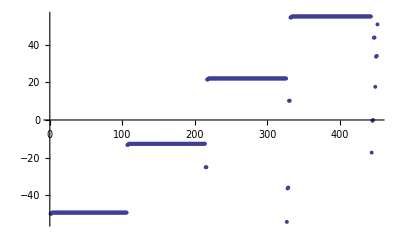

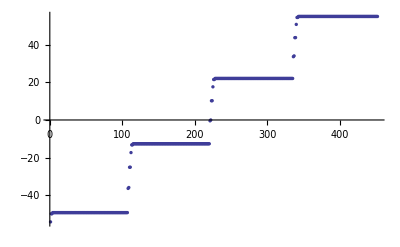

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

{59|0|1/2|1/2,56|3|7/2|1/2,56|3|5/2|1/2,56|4|7/2|1/2,56|4|9/2|1/2,56|5|9/2|1/2,56|5|11/2|1/2,56|6|11/2|1/2,56|6|13/2|1/2,56|7|13/2|1/2,56|7|15/2|1/2,56|8|15/2|1/2,56|8|17/2|1/2,56|9|17/2|1/2,56|9|19/2|1/2,56|10|19/2|1/2,56|10|21/2|1/2,56|11|21/2|1/2,56|11|23/2|1/2,56|12|23/2|1/2,56|12|25/2|1/2,56|13|25/2|1/2,56|13|27/2|1/2,56|14|27/2|1/2,56|14|29/2|1/2,56|15|29/2|1/2,56|15|31/2|1/2,56|16|31/2|1/2,56|16|33/2|1/2,56|17|33/2|1/2,56|17|35/2|1/2,56|18|35/2|1/2,56|18|37/2|1/2,56|19|37/2|1/2,56|19|39/2|1/2,56|20|39/2|1/2,56|20|41/2|1/2,56|21|41/2|1/2,56|21|43/2|1/2,56|22|43/2|1/2,56|22|45/2|1/2,56|23|45/2|1/2,56|23|47/2|1/2,56|24|47/2|1/2,56|24|49/2|1/2,56|25|49/2|1/2,56|25|51/2|1/2,56|26|51/2|1/2,56|26|53/2|1/2,56|27|53/2|1/2,56|27|55/2|1/2,56|28|55/2|1/2,56|28|57/2|1/2,56|29|57/2|1/2,56|29|59/2|1/2,56|30|59/2|1/2,56|30|61/2|1/2,56|31|61/2|1/2,56|31|63/2|1/2,56|32|63/2|1/2,56|32|65/2|1/2,56|33|65/2|1/2,56|33|67/2|1/2,56|34|67/2|1/2,56|34|69/2|1/2,56|35|69/2|1/2,56|35|71/2|1/2,56|36|71/2|1/2,56|36|73/2|1/2,56|37|73/2|1/2,56|37|75/2|1/2,56|38|75/2|1/2,56|38|77/2|1/2,56|39|77/2|1/2,56|39|79/2|1/2,56|40|79/2|1/2,56|40|81/2|1/2,56|41|81/2|1/2,56|41|83/2|1/2,56|42|83/2|1/2,56|42|85/2|1/2,56|43|85/2|1/2,56|43|87/2|1/2,56|44|87/2|1/2,56|44|89/2|1/2,56|45|89/2|1/2,56|45|91/2|1/2,56|46|91/2|1/2,56|46|93/2|1/2,56|47|93/2|1/2,56|47|95/2|1/2,56|48|95/2|1/2,56|48|97/2|1/2,56|49|97/2|1/2,56|49|99/2|1/2,56|50|99/2|1/2,56|50|101/2|1/2,56|51|101/2|1/2,56|51|103/2|1/2,56|52|103/2|1/2,56|52|105/2|1/2,56|53|105/2|1/2,56|53|107/2|1/2,56|54|107/2|1/2,56|54|109/2|1/2,56|55|109/2|1/2,56|55|111/2|1/2,59|1|1/2|1/2,59|1|3/2|1/2,58|2|3/2|1/2,58|2|5/2|1/2,60|0|1/2|1/2,57|3|7/2|1/2,57|3|5/2|1/2,57|4|7/2|1/2,57|4|9/2|1/2,57|5|9/2|1/2,57|5|11/2|1/2,57|6|11/2|1/2,57|6|13/2|1/2,57|7|13/2|1/2,57|7|15/2|1/2,57|8|15/2|1/2,57|8|17/2|1/2,57|9|17/2|1/2,57|9|19/2|1/2,57|10|19/2|1/2,57|10|21/2|1/2,57|11|21/2|1/2,57|11|23/2|1/2,57|12|23/2|1/2,57|12|25/2|1/2,57|13|25/2|1/2,57|13|27/2|1/2,57|14|27/2|1/2,57|14|29/2|1/2,57|15|29/2|1/2,57|15|31/2|1/2,57|16|31/2|1/2,57|16|33/2|1/2,57|17|33/2|1/2,57|17|35/2|1/2,57|18|35/2|1/2,57|18|37/2|1/2,57|19|37/2|1/2,57|19|39/2|1/2,57|20|39/2|1/2,57|20|41/2|1/2,57|21|41/2|1/2,57|21|43/2|1/2,57|22|43/2|1/2,57|22|45/2|1/2,57|23|45/2|1/2,57|23|47/2|1/2,57|24|47/2|1/2,57|24|49/2|1/2,57|25|49/2|1/2,57|25|51/2|1/2,57|26|51/2|1/2,57|26|53/2|1/2,57|27|53/2|1/2,57|27|55/2|1/2,57|28|55/2|1/2,57|28|57/2|1/2,57|29|57/2|1/2,57|29|59/2|1/2,57|30|59/2|1/2,57|30|61/2|1/2,57|31|61/2|1/2,57|31|63/2|1/2,57|32|63/2|1/2,57|32|65/2|1/2,57|33|65/2|1/2,57|33|67/2|1/2,57|34|67/2|1/2,57|34|69/2|1/2,57|35|69/2|1/2,57|35|71/2|1/2,57|36|71/2|1/2,57|36|73/2|1/2,57|37|73/2|1/2,57|37|75/2|1/2,57|38|75/2|1/2,57|38|77/2|1/2,57|39|77/2|1/2,57|39|79/2|1/2,57|40|79/2|1/2,57|40|81/2|1/2,57|41|81/2|1/2,57|41|83/2|1/2,57|42|83/2|1/2,57|42|85/2|1/2,57|43|85/2|1/2,57|43|87/2|1/2,57|44|87/2|1/2,57|44|89/2|1/2,57|45|89/2|1/2,57|45|91/2|1/2,57|46|91/2|1/2,57|46|93/2|1/2,57|47|93/2|1/2,57|47|95/2|1/2,57|48|95/2|1/2,57|48|97/2|1/2,57|49|97/2|1/2,57|49|99/2|1/2,57|50|99/2|1/2,57|50|101/2|1/2,57|51|101/2|1/2,57|51|103/2|1/2,57|52|103/2|1/2,57|52|105/2|1/2,57|53|105/2|1/2,57|53|107/2|1/2,57|54|107/2|1/2,57|54|109/2|1/2,57|55|109/2|1/2,57|55|111/2|1/2,57|56|111/2|1/2,57|56|113/2|1/2,60|1|1/2|1/2,60|1|3/2|1/2,59|2|3/2|1/2,59|2|5/2|1/2,61|0|1/2|1/2,58|3|7/2|1/2,58|3|5/2|1/2,58|4|7/2|1/2,58|4|9/2|1/2,58|5|9/2|1/2,58|5|11/2|1/2,58|6|11/2|1/2,58|6|13/2|1/2,58|7|13/2|1/2,58|7|15/2|1/2,58|8|15/2|1/2,58|8|17/2|1/2,58|9|17/2|1/2,58|9|19/2|1/2,58|10|19/2|1/2,58|10|21/2|1/2,58|11|21/2|1/2,58|11|23/2|1/2,58|12|23/2|1/2,58|12|25/2|1/2,58|13|25/2|1/2,58|13|27/2|1/2,58|14|27/2|1/2,58|14|29/2|1/2,58|15|29/2|1/2,58|15|31/2|1/2,58|16|31/2|1/2,58|16|33/2|1/2,58|17|33/2|1/2,58|17|35/2|1/2,58|18|35/2|1/2,58|18|37/2|1/2,58|19|37/2|1/2,58|19|39/2|1/2,58|20|39/2|1/2,58|20|41/2|1/2,58|21|41/2|1/2,58|21|43/2|1/2,58|22|43/2|1/2,58|22|45/2|1/2,58|23|45/2|1/2,58|23|47/2|1/2,58|24|47/2|1/2,58|24|49/2|1/2,58|25|49/2|1/2,58|25|51/2|1/2,58|26|51/2|1/2,58|26|53/2|1/2,58|27|53/2|1/2,58|27|55/2|1/2,58|28|55/2|1/2,58|28|57/2|1/2,58|29|57/2|1/2,58|29|59/2|1/2,58|30|59/2|1/2,58|30|61/2|1/2,58|31|61/2|1/2,58|31|63/2|1/2,58|32|63/2|1/2,58|32|65/2|1/2,58|33|65/2|1/2,58|33|67/2|1/2,58|34|67/2|1/2,58|34|69/2|1/2,58|35|69/2|1/2,58|35|71/2|1/2,58|36|71/2|1/2,58|36|73/2|1/2,58|37|73/2|1/2,58|37|75/2|1/2,58|38|75/2|1/2,58|38|77/2|1/2,58|39|77/2|1/2,58|39|79/2|1/2,58|40|79/2|1/2,58|40|81/2|1/2,58|41|81/2|1/2,58|41|83/2|1/2,58|42|83/2|1/2,58|42|85/2|1/2,58|43|85/2|1/2,58|43|87/2|1/2,58|44|87/2|1/2,58|44|89/2|1/2,58|45|89/2|1/2,58|45|91/2|1/2,58|46|91/2|1/2,58|46|93/2|1/2,58|47|93/2|1/2,58|47|95/2|1/2,58|48|95/2|1/2,58|48|97/2|1/2,58|49|97/2|1/2,58|49|99/2|1/2,58|50|99/2|1/2,58|50|101/2|1/2,58|51|101/2|1/2,58|51|103/2|1/2,58|52|103/2|1/2,58|52|105/2|1/2,58|53|105/2|1/2,58|53|107/2|1/2,58|54|107/2|1/2,58|54|109/2|1/2,58|55|109/2|1/2,58|55|111/2|1/2,58|56|111/2|1/2,58|56|113/2|1/2,58|57|113/2|1/2,58|57|115/2|1/2,61|1|1/2|1/2,61|1|3/2|1/2,60|2|3/2|1/2,60|2|5/2|1/2,62|0|1/2|1/2,59|3|7/2|1/2,59|3|5/2|1/2,59|4|7/2|1/2,59|4|9/2|1/2,59|5|9/2|1/2,59|5|11/2|1/2,59|6|11/2|1/2,59|6|13/2|1/2,59|7|13/2|1/2,59|7|15/2|1/2,59|8|15/2|1/2,59|8|17/2|1/2,59|9|17/2|1/2,59|9|19/2|1/2,59|10|19/2|1/2,59|10|21/2|1/2,59|11|21/2|1/2,59|11|23/2|1/2,59|12|23/2|1/2,59|12|25/2|1/2,59|13|25/2|1/2,59|13|27/2|1/2,59|14|27/2|1/2,59|14|29/2|1/2,59|15|29/2|1/2,59|15|31/2|1/2,59|16|31/2|1/2,59|16|33/2|1/2,59|17|33/2|1/2,59|17|35/2|1/2,59|18|35/2|1/2,59|18|37/2|1/2,59|19|37/2|1/2,59|19|39/2|1/2,59|20|39/2|1/2,59|20|41/2|1/2,59|21|41/2|1/2,59|21|43/2|1/2,59|22|43/2|1/2,59|22|45/2|1/2,59|23|45/2|1/2,59|23|47/2|1/2,59|24|47/2|1/2,59|24|49/2|1/2,59|25|49/2|1/2,59|25|51/2|1/2,59|26|51/2|1/2,59|26|53/2|1/2,59|27|53/2|1/2,59|27|55/2|1/2,59|28|55/2|1/2,59|28|57/2|1/2,59|29|57/2|1/2,59|29|59/2|1/2,59|30|59/2|1/2,59|30|61/2|1/2,59|31|61/2|1/2,59|31|63/2|1/2,59|32|63/2|1/2,59|32|65/2|1/2,59|33|65/2|1/2,59|33|67/2|1/2,59|34|67/2|1/2,59|34|69/2|1/2,59|35|69/2|1/2,59|35|71/2|1/2,59|36|71/2|1/2,59|36|73/2|1/2,59|37|73/2|1/2,59|37|75/2|1/2,59|38|75/2|1/2,59|38|77/2|1/2,59|39|77/2|1/2,59|39|79/2|1/2,59|40|79/2|1/2,59|40|81/2|1/2,59|41|81/2|1/2,59|41|83/2|1/2,59|42|83/2|1/2,59|42|85/2|1/2,59|43|85/2|1/2,59|43|87/2|1/2,59|44|87/2|1/2,59|44|89/2|1/2,59|45|89/2|1/2,59|45|91/2|1/2,59|46|91/2|1/2,59|46|93/2|1/2,59|47|93/2|1/2,59|47|95/2|1/2,59|48|95/2|1/2,59|48|97/2|1/2,59|49|97/2|1/2,59|49|99/2|1/2,59|50|99/2|1/2,59|50|101/2|1/2,59|51|101/2|1/2,59|51|103/2|1/2,59|52|103/2|1/2,59|52|105/2|1/2,59|53|105/2|1/2,59|53|107/2|1/2,59|54|107/2|1/2,59|54|109/2|1/2,59|55|109/2|1/2,59|55|111/2|1/2,59|56|111/2|1/2,59|56|113/2|1/2,59|57|113/2|1/2,59|57|115/2|1/2,59|58|115/2|1/2,59|58|117/2|1/2}

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, 0}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{4.28091,0.-4.28091 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{28.485,Null}

{0,0,0}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.04967×10^12,-1.04967×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.02504×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.05398×10^12,-1.03624×10^12,-1.03576×10^12,-9.89787×10^11,-9.89731×10^11,-9.45608×10^11,-9.45609×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-1.01724×10^12,-1.00042×10^12,-9.99955×10^11,-9.56324×10^11,-9.56271×10^11,-9.82389×10^11,-9.66416×10^11,-9.65979×10^11,-9.49297×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-1053.98,-1049.67,-1049.67,-1049.11,-1049.11,-1049.11,-1049.11,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1048.99,-1048.99,-1048.99,-1048.99,-1036.24,-1035.76,-1025.04,-1024.98,-1017.24,-1013.15,-1013.15,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.5,-1012.5,-1000.42,-999.955,-989.787,-989.731,-982.389,-978.508,-978.507,-978.012,-978.011,-978.009,-978.009,-978.007,-978.006,-978.004,-978.004,-978.002,-978.002,-977.999,-977.999,-977.997,-977.997,-977.995,-977.994,-977.992,-977.992,-977.99,-977.99,-977.988,-977.987,-977.985,-977.985,-977.983,-977.983,-977.981,-977.98,-977.978,-977.978,-977.976,-977.976,-977.974,-977.973,-977.971,-977.971,-977.969,-977.969,-977.967,-977.967,-977.964,-977.964,-977.962,-977.962,-977.96,-977.96,-977.957,-977.957,-977.955,-977.955,-977.953,-977.953,-977.95,-977.95,-977.948,-977.948,-977.946,-977.946,-977.943,-977.943,-977.941,-977.941,-977.939,-977.939,-977.936,-977.936,-977.934,-977.934,-977.932,-977.932,-977.93,-977.929,-977.927,-977.927,-977.925,-977.925,-977.923,-977.923,-977.92,-977.92,-977.918,-977.918,-977.916,-977.916,-977.913,-977.913,-977.911,-977.911,-977.909,-977.909,-977.906,-977.906,-977.904,-977.904,-977.902,-977.901,-977.899,-977.899,-977.897,-977.897,-977.894,-977.894,-977.892,-977.892,-977.89,-977.889,-977.887,-977.887,-966.416,-965.979,-956.324,-956.271,-949.297,-945.611,-945.61,-945.144,-945.144,-945.141,-945.141,-945.139,-945.139,-945.136,-945.136,-945.134,-945.134,-945.131,-945.131,-945.129,-945.129,-945.127,-945.127,-945.124,-945.124,-945.122,-945.122,-945.119,-945.119,-945.117,-945.117,-945.115,-945.115,-945.112,-945.112,-945.11,-945.11,-945.108,-945.108,-945.105,-945.105,-945.103,-945.103,-945.101,-945.1,-945.098,-945.098,-945.096,-945.096,-945.093,-945.093,-945.091,-945.091,-945.089,-945.089,-945.086,-945.086,-945.084,-945.084,-945.082,-945.082,-945.079,-945.079,-945.077,-945.077,-945.075,-945.075,-945.072,-945.072,-945.07,-945.07,-945.068,-945.068,-945.065,-945.065,-945.063,-945.063,-945.06,-945.06,-945.058,-945.058,-945.056,-945.056,-945.053,-945.053,-945.051,-945.051,-945.049,-945.049,-945.046,-945.046,-945.044,-945.044,-945.042,-945.042,-945.039,-945.039,-945.037,-945.037,-945.034,-945.034,-945.032,-945.032,-945.03,-945.03,-945.027,-945.027,-945.025,-945.025,-945.023,-945.022,-945.02,-945.02,-945.018,-945.017,-945.015,-945.015}

{{300,-67.029,59|0|1/2|1/2},{300,-66.9115,56|3|7/2|1/2},{300,-66.3222,56|3|5/2|1/2},{300,-66.2322,56|4|7/2|1/2},{300,-65.6332,56|4|9/2|1/2},{300,-65.558,56|5|9/2|1/2},{300,-64.9523,56|5|11/2|1/2},{300,-64.887,56|6|11/2|1/2},{300,-64.2761,56|6|13/2|1/2},{300,-64.2183,56|7|13/2|1/2},{300,-63.6033,56|7|15/2|1/2},{300,-63.5512,56|8|15/2|1/2},{300,-62.9328,56|8|17/2|1/2},{300,-62.8855,56|9|17/2|1/2},{300,-62.2641,56|9|19/2|1/2},{300,-62.2208,56|10|19/2|1/2},{300,-61.5969,56|10|21/2|1/2},{300,-61.5569,56|11|21/2|1/2},{300,-60.9308,56|11|23/2|1/2},{300,-60.8937,56|12|23/2|1/2},{300,-60.2659,56|12|25/2|1/2},{300,-60.231,56|13|25/2|1/2},{300,-59.6022,56|13|27/2|1/2},{300,-59.5689,56|14|27/2|1/2},{300,-58.94,56|14|29/2|1/2},{300,-58.9071,56|15|29/2|1/2},{300,-58.2821,56|15|31/2|1/2},{300,-58.2456,56|16|31/2|1/2},{300,-57.6831,56|16|33/2|1/2},{300,-57.5844,56|17|33/2|1/2},{300,-57.5016,56|17|35/2|1/2},{300,-56.9305,56|18|35/2|1/2},{300,-56.9234,56|18|37/2|1/2},{300,-56.2744,56|19|37/2|1/2},{300,-56.2625,56|19|39/2|1/2},{300,-55.614,56|20|39/2|1/2},{300,-55.6017,56|20|41/2|1/2},{300,-54.9527,56|21|41/2|1/2},{300,-54.941,56|21|43/2|1/2},{300,-54.2911,56|22|43/2|1/2},{300,-54.2804,56|22|45/2|1/2},{300,-53.6292,56|23|45/2|1/2},{300,-53.6197,56|23|47/2|1/2},{300,-52.9673,56|24|47/2|1/2},{300,-52.9589,56|24|49/2|1/2},{300,-52.3052,56|25|49/2|1/2},{300,-52.2981,56|25|51/2|1/2},{300,-51.6429,56|26|51/2|1/2},{300,-51.6371,56|26|53/2|1/2},{300,-50.9805,56|27|53/2|1/2},{300,-50.9759,56|27|55/2|1/2},{300,-50.3178,56|28|55/2|1/2},{300,-50.3145,56|28|57/2|1/2},{300,-49.655,56|29|57/2|1/2},{300,-49.653,56|29|59/2|1/2},{300,-48.9921,56|30|59/2|1/2},{300,-48.9913,56|30|61/2|1/2},{300,-48.3296,56|31|61/2|1/2},{300,-48.329,56|31|63/2|1/2},{300,-47.6678,56|32|63/2|1/2},{300,-47.666,56|32|65/2|1/2},{300,-47.0059,56|33|65/2|1/2},{300,-47.0029,56|33|67/2|1/2},{300,-46.344,56|34|67/2|1/2},{300,-46.3398,56|34|69/2|1/2},{300,-45.6821,56|35|69/2|1/2},{300,-45.6767,56|35|71/2|1/2},{300,-45.0202,56|36|71/2|1/2},{300,-45.0138,56|36|73/2|1/2},{300,-44.3586,56|37|73/2|1/2},{300,-44.3512,56|37|75/2|1/2},{300,-43.6976,56|38|75/2|1/2},{300,-43.6894,56|38|77/2|1/2},{300,-43.0377,56|39|77/2|1/2},{300,-43.0292,56|39|79/2|1/2},{300,-42.3804,56|40|79/2|1/2},{300,-42.3725,56|40|81/2|1/2},{300,-41.7303,56|41|81/2|1/2},{300,-41.7232,56|41|83/2|1/2},{300,-41.109,56|42|83/2|1/2},{300,-41.0894,56|42|85/2|1/2},{300,-40.5801,56|43|85/2|1/2},{300,-40.5104,56|43|87/2|1/2},{300,-40.1248,56|44|87/2|1/2},{300,-40.0545,56|44|89/2|1/2},{300,-39.5679,56|45|89/2|1/2},{300,-39.5463,56|45|91/2|1/2},{300,-38.9464,56|46|91/2|1/2},{300,-38.9223,56|46|93/2|1/2},{300,-38.2975,56|47|93/2|1/2},{300,-38.2686,56|47|95/2|1/2},{300,-37.6377,56|48|95/2|1/2},{300,-37.6052,56|48|97/2|1/2},{300,-36.9726,56|49|97/2|1/2},{300,-36.9366,56|49|99/2|1/2},{300,-36.3043,56|50|99/2|1/2},{300,-36.2645,56|50|101/2|1/2},{300,-35.6333,56|51|101/2|1/2},{300,-35.5891,56|51|103/2|1/2},{300,-34.9598,56|52|103/2|1/2},{300,-34.9104,56|52|105/2|1/2},{300,-34.2835,56|53|105/2|1/2},{300,-34.2274,56|53|107/2|1/2},{300,-33.6038,56|54|107/2|1/2},{300,-33.5387,56|54|109/2|1/2},{300,-32.9194,56|55|109/2|1/2},{300,-32.8406,56|55|111/2|1/2},{300,-32.227,59|1|1/2|1/2},{300,-32.1221,59|1|3/2|1/2},{300,-30.8931,58|2|3/2|1/2},{300,-30.7553,58|2|5/2|1/2},{300,-30.2028,60|0|1/2|1/2},{300,-30.0965,57|3|7/2|1/2},{300,-29.5297,57|3|5/2|1/2},{300,-29.4435,57|4|7/2|1/2},{300,-28.865,57|4|9/2|1/2},{300,-28.7948,57|5|9/2|1/2},{300,-28.2054,57|5|11/2|1/2},{300,-28.1484,57|6|11/2|1/2},{300,-27.5488,57|6|13/2|1/2},{300,-27.503,57|7|13/2|1/2},{300,-26.8936,57|7|15/2|1/2},{300,-26.8569,57|8|15/2|1/2},{300,-26.2387,57|8|17/2|1/2},{300,-26.2092,57|9|17/2|1/2},{300,-25.5834,57|9|19/2|1/2},{300,-25.5593,57|10|19/2|1/2},{300,-24.9271,57|10|21/2|1/2},{300,-24.907,57|11|21/2|1/2},{300,-24.2697,57|11|23/2|1/2},{300,-24.2524,57|12|23/2|1/2},{300,-23.611,57|12|25/2|1/2},{300,-23.5957,57|13|25/2|1/2},{300,-22.9513,57|13|27/2|1/2},{300,-22.9372,57|14|27/2|1/2},{300,-22.2907,57|14|29/2|1/2},{300,-22.277,57|15|29/2|1/2},{300,-21.6296,57|15|31/2|1/2},{300,-21.6155,57|16|31/2|1/2},{300,-20.9687,57|16|33/2|1/2},{300,-20.9528,57|17|33/2|1/2},{300,-20.3097,57|17|35/2|1/2},{300,-20.289,57|18|35/2|1/2},{300,-19.6575,57|18|37/2|1/2},{300,-19.6243,57|19|37/2|1/2},{300,-19.0429,57|19|39/2|1/2},{300,-18.9589,57|20|39/2|1/2},{300,-18.6468,57|20|41/2|1/2},{300,-18.2928,57|21|41/2|1/2},{300,-18.2156,57|21|43/2|1/2},{300,-17.6261,57|22|43/2|1/2},{300,-17.59,57|22|45/2|1/2},{300,-16.9589,57|23|45/2|1/2},{300,-16.934,57|23|47/2|1/2},{300,-16.2913,57|24|47/2|1/2},{300,-16.2711,57|24|49/2|1/2},{300,-15.6233,57|25|49/2|1/2},{300,-15.6054,57|25|51/2|1/2},{300,-14.9549,57|26|51/2|1/2},{300,-14.9381,57|26|53/2|1/2},{300,-14.2861,57|27|53/2|1/2},{300,-14.2699,57|27|55/2|1/2},{300,-13.617,57|28|55/2|1/2},{300,-13.6008,57|28|57/2|1/2},{300,-12.9476,57|29|57/2|1/2},{300,-12.9312,57|29|59/2|1/2},{300,-12.278,57|30|59/2|1/2},{300,-12.2612,57|30|61/2|1/2},{300,-11.6082,57|31|61/2|1/2},{300,-11.5908,57|31|63/2|1/2},{300,-10.9383,57|32|63/2|1/2},{300,-10.9202,57|32|65/2|1/2},{300,-10.2683,57|33|65/2|1/2},{300,-10.2493,57|33|67/2|1/2},{300,-9.59825,57|34|67/2|1/2},{300,-9.57827,57|34|69/2|1/2},{300,-8.92815,57|35|69/2|1/2},{300,-8.90704,57|35|71/2|1/2},{300,-8.25805,57|36|71/2|1/2},{300,-8.23562,57|36|73/2|1/2},{300,-7.58806,57|37|73/2|1/2},{300,-7.56405,57|37|75/2|1/2},{300,-6.91843,57|38|75/2|1/2},{300,-6.89245,57|38|77/2|1/2},{300,-6.24988,57|39|77/2|1/2},{300,-6.22109,57|39|79/2|1/2},{300,-5.58485,57|40|79/2|1/2},{300,-5.55079,57|40|81/2|1/2},{300,-4.93907,57|41|81/2|1/2},{300,-4.88527,57|41|83/2|1/2},{300,-4.51704,57|42|83/2|1/2},{300,-4.27432,57|42|85/2|1/2},{300,-4.16272,57|43|85/2|1/2},{300,-4.03521,57|43|87/2|1/2},{300,-3.52691,57|44|87/2|1/2},{300,-3.49494,57|44|89/2|1/2},{300,-2.86152,57|45|89/2|1/2},{300,-2.83133,57|45|91/2|1/2},{300,-2.19077,57|46|91/2|1/2},{300,-2.15887,57|46|93/2|1/2},{300,-1.51778,57|47|93/2|1/2},{300,-1.48364,57|47|95/2|1/2},{300,-0.843357,57|48|95/2|1/2},{300,-0.806715,57|48|97/2|1/2},{300,-0.167726,57|49|97/2|1/2},{300,-0.128321,57|49|99/2|1/2},{300,0.50908,57|50|99/2|1/2},{300,0.551574,57|50|101/2|1/2},{300,1.18713,57|51|101/2|1/2},{300,1.23313,57|51|103/2|1/2},{300,1.86658,57|52|103/2|1/2},{300,1.91661,57|52|105/2|1/2},{300,2.54755,57|53|105/2|1/2},{300,2.60208,57|53|107/2|1/2},{300,3.15225,57|54|107/2|1/2},{300,3.22471,57|54|109/2|1/2},{300,3.28308,57|55|109/2|1/2},{300,3.29675,57|55|111/2|1/2},{300,3.8693,57|56|111/2|1/2},{300,3.90852,57|56|113/2|1/2},{300,3.97727,60|1|1/2|1/2},{300,3.99695,60|1|3/2|1/2},{300,4.56839,59|2|3/2|1/2},{300,4.59703,59|2|5/2|1/2},{300,4.66454,61|0|1/2|1/2},{300,4.7047,58|3|7/2|1/2},{300,5.26077,58|3|5/2|1/2},{300,5.29222,58|4|7/2|1/2},{300,5.34749,58|4|9/2|1/2},{300,5.4297,58|5|9/2|1/2},{300,5.95045,58|5|11/2|1/2},{300,5.99996,58|6|11/2|1/2},{300,6.62318,58|6|13/2|1/2},{300,6.66598,58|7|13/2|1/2},{300,7.2925,58|7|15/2|1/2},{300,7.32878,58|8|15/2|1/2},{300,7.95833,58|8|17/2|1/2},{300,7.98881,58|9|17/2|1/2},{300,8.62135,58|9|19/2|1/2},{300,8.64695,58|10|19/2|1/2},{300,9.28246,58|10|21/2|1/2},{300,9.30418,58|11|21/2|1/2},{300,9.94261,58|11|23/2|1/2},{300,9.96151,58|12|23/2|1/2},{300,10.6027,58|12|25/2|1/2},{300,10.6198,58|13|25/2|1/2},{300,11.2635,58|13|27/2|1/2},{300,11.2796,58|14|27/2|1/2},{300,11.9252,58|14|29/2|1/2},{300,11.9414,58|15|29/2|1/2},{300,12.5879,58|15|31/2|1/2},{300,12.6053,58|16|31/2|1/2},{300,13.2513,58|16|33/2|1/2},{300,13.2713,58|17|33/2|1/2},{300,13.9141,58|17|35/2|1/2},{300,13.9392,58|18|35/2|1/2},{300,14.5734,58|18|37/2|1/2},{300,14.609,58|19|37/2|1/2},{300,15.2193,58|19|39/2|1/2},{300,15.2804,58|20|39/2|1/2},{300,15.7993,58|20|41/2|1/2},{300,15.9532,58|21|41/2|1/2},{300,16.2089,58|21|43/2|1/2},{300,16.6273,58|22|43/2|1/2},{300,16.7183,58|22|45/2|1/2},{300,17.3024,58|23|45/2|1/2},{300,17.3518,58|23|47/2|1/2},{300,17.9786,58|24|47/2|1/2},{300,18.0132,58|24|49/2|1/2},{300,18.6556,58|25|49/2|1/2},{300,18.6832,58|25|51/2|1/2},{300,19.3334,58|26|51/2|1/2},{300,19.3573,58|26|53/2|1/2},{300,20.012,58|27|53/2|1/2},{300,20.0336,58|27|55/2|1/2},{300,20.6912,58|28|55/2|1/2},{300,20.7117,58|28|57/2|1/2},{300,21.3711,58|29|57/2|1/2},{300,21.3909,58|29|59/2|1/2},{300,22.0516,58|30|59/2|1/2},{300,22.0712,58|30|61/2|1/2},{300,22.7325,58|31|61/2|1/2},{300,22.7522,58|31|63/2|1/2},{300,23.4138,58|32|63/2|1/2},{300,23.4338,58|32|65/2|1/2},{300,24.0954,58|33|65/2|1/2},{300,24.116,58|33|67/2|1/2},{300,24.7772,58|34|67/2|1/2},{300,24.7986,58|34|69/2|1/2},{300,25.4591,58|35|69/2|1/2},{300,25.4816,58|35|71/2|1/2},{300,26.1411,58|36|71/2|1/2},{300,26.165,58|36|73/2|1/2},{300,26.823,58|37|73/2|1/2},{300,26.8488,58|37|75/2|1/2},{300,27.5041,58|38|75/2|1/2},{300,27.5328,58|38|77/2|1/2},{300,28.1825,58|39|77/2|1/2},{300,28.217,58|39|79/2|1/2},{300,28.8461,58|40|79/2|1/2},{300,28.901,58|40|81/2|1/2},{300,29.2982,58|41|81/2|1/2},{300,29.5837,58|41|83/2|1/2},{300,29.6243,58|42|83/2|1/2},{300,30.2588,58|42|85/2|1/2},{300,30.2705,58|43|85/2|1/2},{300,30.746,58|43|87/2|1/2},{300,30.9482,58|44|87/2|1/2},{300,31.01,58|44|89/2|1/2},{300,31.6309,58|45|89/2|1/2},{300,31.6651,58|45|91/2|1/2},{300,32.3156,58|46|91/2|1/2},{300,32.3479,58|46|93/2|1/2},{300,33.0013,58|47|93/2|1/2},{300,33.0344,58|47|95/2|1/2},{300,33.6878,58|48|95/2|1/2},{300,33.7225,58|48|97/2|1/2},{300,34.375,58|49|97/2|1/2},{300,34.4116,58|49|99/2|1/2},{300,35.0629,58|50|99/2|1/2},{300,35.1014,58|50|101/2|1/2},{300,35.751,58|51|101/2|1/2},{300,35.7907,58|51|103/2|1/2},{300,36.0809,58|52|103/2|1/2},{300,36.1886,58|52|105/2|1/2},{300,36.4419,58|53|105/2|1/2},{300,36.4846,58|53|107/2|1/2},{300,36.8229,58|54|107/2|1/2},{300,36.9021,58|54|109/2|1/2},{300,37.1348,58|55|109/2|1/2},{300,37.1811,58|55|111/2|1/2},{300,37.5427,58|56|111/2|1/2},{300,37.6073,58|56|113/2|1/2},{300,37.8298,58|57|113/2|1/2},{300,37.8807,58|57|115/2|1/2},{300,38.2518,61|1|1/2|1/2},{300,38.3073,61|1|3/2|1/2},{300,38.5271,60|2|3/2|1/2},{300,38.5841,60|2|5/2|1/2},{300,38.9545,62|0|1/2|1/2},{300,39.0036,59|3|7/2|1/2},{300,39.2274,59|3|5/2|1/2},{300,39.2931,59|4|7/2|1/2},{300,39.6528,59|4|9/2|1/2},{300,39.6973,59|5|9/2|1/2},{300,39.9317,59|5|11/2|1/2},{300,40.0111,59|6|11/2|1/2},{300,40.3479,59|6|13/2|1/2},{300,40.3887,59|7|13/2|1/2},{300,40.6427,59|7|15/2|1/2},{300,40.7487,59|8|15/2|1/2},{300,41.0407,59|8|17/2|1/2},{300,41.0775,59|9|17/2|1/2},{300,41.7094,59|9|19/2|1/2},{300,41.755,59|10|19/2|1/2},{300,42.3803,59|10|21/2|1/2},{300,42.4309,59|11|21/2|1/2},{300,43.0483,59|11|23/2|1/2},{300,43.1042,59|12|23/2|1/2},{300,43.7141,59|12|25/2|1/2},{300,43.7752,59|13|25/2|1/2},{300,44.379,59|13|27/2|1/2},{300,44.4447,59|14|27/2|1/2},{300,45.0445,59|14|29/2|1/2},{300,45.1137,59|15|29/2|1/2},{300,45.7118,59|15|31/2|1/2},{300,45.7831,59|16|31/2|1/2},{300,46.3817,59|16|33/2|1/2},{300,46.4538,59|17|33/2|1/2},{300,47.0542,59|17|35/2|1/2},{300,47.1261,59|18|35/2|1/2},{300,47.7293,59|18|37/2|1/2},{300,47.8005,59|19|37/2|1/2},{300,48.4064,59|19|39/2|1/2},{300,48.4769,59|20|39/2|1/2},{300,49.0851,59|20|41/2|1/2},{300,49.1553,59|21|41/2|1/2},{300,49.7649,59|21|43/2|1/2},{300,49.8355,59|22|43/2|1/2},{300,50.4451,59|22|45/2|1/2},{300,50.5172,59|23|45/2|1/2},{300,51.125,59|23|47/2|1/2},{300,51.2002,59|24|47/2|1/2},{300,51.8036,59|24|49/2|1/2},{300,51.8843,59|25|49/2|1/2},{300,52.4794,59|25|51/2|1/2},{300,52.5694,59|26|51/2|1/2},{300,53.1497,59|26|53/2|1/2},{300,53.2553,59|27|53/2|1/2},{300,53.8092,59|27|55/2|1/2},{300,53.942,59|28|55/2|1/2},{300,54.4469,59|28|57/2|1/2},{300,54.6292,59|29|57/2|1/2},{300,55.0466,59|29|59/2|1/2},{300,55.3171,59|30|59/2|1/2},{300,55.6135,59|30|61/2|1/2},{300,56.0053,59|31|61/2|1/2},{300,56.1974,59|31|63/2|1/2},{300,56.6939,59|32|63/2|1/2},{300,56.8232,59|32|65/2|1/2},{300,57.3827,59|33|65/2|1/2},{300,57.4775,59|33|67/2|1/2},{300,58.0717,59|34|67/2|1/2},{300,58.1466,59|34|69/2|1/2},{300,58.7609,59|35|69/2|1/2},{300,58.8237,59|35|71/2|1/2},{300,59.4503,59|36|71/2|1/2},{300,59.5052,59|36|73/2|1/2},{300,60.1398,59|37|73/2|1/2},{300,60.1896,59|37|75/2|1/2},{300,60.8296,59|38|75/2|1/2},{300,60.876,59|38|77/2|1/2},{300,61.5196,59|39|77/2|1/2},{300,61.5638,59|39|79/2|1/2},{300,62.2098,59|40|79/2|1/2},{300,62.2527,59|40|81/2|1/2},{300,62.9003,59|41|81/2|1/2},{300,62.9426,59|41|83/2|1/2},{300,63.5912,59|42|83/2|1/2},{300,63.6332,59|42|85/2|1/2},{300,64.2823,59|43|85/2|1/2},{300,64.3246,59|43|87/2|1/2},{300,64.9738,59|44|87/2|1/2},{300,65.0167,59|44|89/2|1/2},{300,65.6657,59|45|89/2|1/2},{300,65.7096,59|45|91/2|1/2},{300,66.358,59|46|91/2|1/2},{300,66.4032,59|46|93/2|1/2},{300,67.0509,59|47|93/2|1/2},{300,67.0976,59|47|95/2|1/2},{300,67.7443,59|48|95/2|1/2},{300,67.7929,59|48|97/2|1/2},{300,68.4383,59|49|97/2|1/2},{300,68.4893,59|49|99/2|1/2},{300,69.1331,59|50|99/2|1/2},{300,69.1867,59|50|101/2|1/2},{300,69.8287,59|51|101/2|1/2},{300,69.8855,59|51|103/2|1/2},{300,70.5253,59|52|103/2|1/2},{300,70.5859,59|52|105/2|1/2},{300,71.223,59|53|105/2|1/2},{300,71.2882,59|53|107/2|1/2},{300,71.9222,59|54|107/2|1/2},{300,71.9931,59|54|109/2|1/2},{300,72.6231,59|55|109/2|1/2},{300,72.7013,59|55|111/2|1/2},{300,73.3262,59|56|111/2|1/2},{300,73.4145,59|56|113/2|1/2},{300,74.0326,59|57|113/2|1/2},{300,74.136,59|57|115/2|1/2},{300,74.7438,59|58|115/2|1/2},{300,74.8753,59|58|117/2|1/2}}

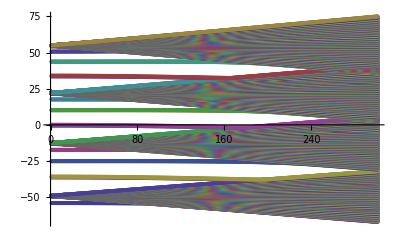

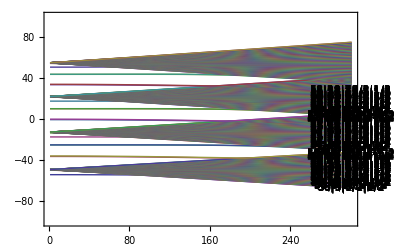

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

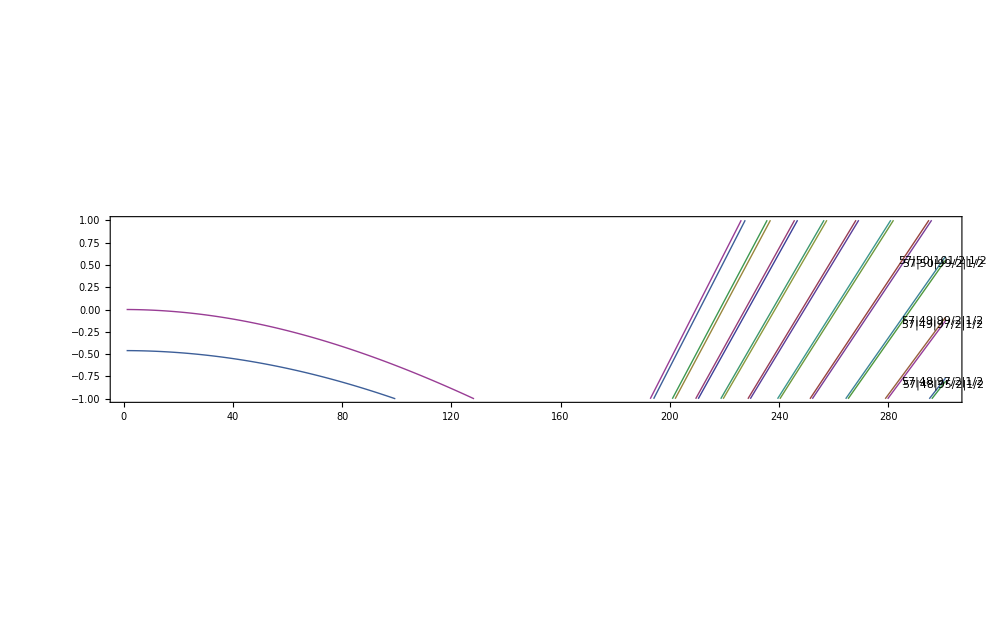

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[222]]

MPList[[222]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport


(*
Export["Stark_Shifts_around_60s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60s.dat",Efieldlist]
*)
Export["60p_j3_2_mj1_2_stark_Shift.dat",MPList[[222]]]
```

60|1|3/2|1/2

{{1,-0.0000678712},{2,-0.000271479},{3,-0.000610803},{4,-0.00108581},{5,-0.00169646},{6,-0.0024427},{7,-0.00332445},{8,-0.00434163},{9,-0.00549414},{10,-0.00678189},{11,-0.00820474},{12,-0.00976258},{13,-0.0114552},{14,-0.0132826},{15,-0.0152444},{16,-0.0173406},{17,-0.0195709},{18,-0.0219351},{19,-0.024433},{20,-0.0270644},{21,-0.0298291},{22,-0.0327267},{23,-0.035757},{24,-0.0389198},{25,-0.0422147},{26,-0.0456415},{27,-0.0491998},{28,-0.0528893},{29,-0.0567098},{30,-0.0606607},{31,-0.0647419},{32,-0.0689529},{33,-0.0732933},{34,-0.0777628},{35,-0.082361},{36,-0.0870875},{37,-0.0919418},{38,-0.0969235},{39,-0.102032},{40,-0.107267},{41,-0.112629},{42,-0.118116},{43,-0.123728},{44,-0.129465},{45,-0.135326},{46,-0.141311},{47,-0.147419},{48,-0.153649},{49,-0.160002},{50,-0.166477},{51,-0.173072},{52,-0.179788},{53,-0.186625},{54,-0.19358},{55,-0.200655},{56,-0.207848},{57,-0.215158},{58,-0.222586},{59,-0.230131},{60,-0.237791},{61,-0.245567},{62,-0.253458},{63,-0.261463},{64,-0.269581},{65,-0.277813},{66,-0.286157},{67,-0.294612},{68,-0.303179},{69,-0.311856},{70,-0.320643},{71,-0.32954},{72,-0.338544},{73,-0.347657},{74,-0.356877},{75,-0.366204},{76,-0.375637},{77,-0.385175},{78,-0.394818},{79,-0.404565},{80,-0.414415},{81,-0.424368},{82,-0.434423},{83,-0.444579},{84,-0.454836},{85,-0.465194},{86,-0.47565},{87,-0.486206},{88,-0.496859},{89,-0.50761},{90,-0.518458},{91,-0.529402},{92,-0.540442},{93,-0.551576},{94,-0.562805},{95,-0.574127},{96,-0.585542},{97,-0.597049},{98,-0.608648},{99,-0.620337},{100,-0.632117},{101,-0.643987},{102,-0.655945},{103,-0.667992},{104,-0.680127},{105,-0.692349},{106,-0.704657},{107,-0.717051},{108,-0.72953},{109,-0.742094},{110,-0.754742},{111,-0.767473},{112,-0.780287},{113,-0.793183},{114,-0.80616},{115,-0.819218},{116,-0.832357},{117,-0.845575},{118,-0.858872},{119,-0.872248},{120,-0.885702},{121,-0.899232},{122,-0.91284},{123,-0.926523},{124,-0.940282},{125,-0.954116},{126,-0.968024},{127,-0.982006},{128,-0.99606},{129,-1.01019},{130,-1.02439},{131,-1.03866},{132,-1.053},{133,-1.06741},{134,-1.08189},{135,-1.09644},{136,-1.11105},{137,-1.12574},{138,-1.14049},{139,-1.15531},{140,-1.17019},{141,-1.18514},{142,-1.20015},{143,-1.21522},{144,-1.23036},{145,-1.24556},{146,-1.26082},{147,-1.27615},{148,-1.29153},{149,-1.30697},{150,-1.32246},{151,-1.33802},{152,-1.35363},{153,-1.36929},{154,-1.38501},{155,-1.40078},{156,-1.4166},{157,-1.43247},{158,-1.44839},{159,-1.46435},{160,-1.48036},{161,-1.49641},{162,-1.5125},{163,-1.52863},{164,-1.54479},{165,-1.56098},{166,-1.57719},{167,-1.59343},{168,-1.60967},{169,-1.62592},{170,-1.64217},{171,-1.65839},{172,-1.67456},{173,-1.69066},{174,-1.70664},{175,-1.72241},{176,-1.73781},{177,-1.7525},{178,-1.76548},{179,-1.77242},{180,-1.75287},{181,-1.7029},{182,-1.64593},{183,-1.58734},{184,-1.52814},{185,-1.46866},{186,-1.40901},{187,-1.34925},{188,-1.28943},{189,-1.22956},{190,-1.16966},{191,-1.10973},{192,-1.04978},{193,-0.989809},{194,-0.929831},{195,-0.869843},{196,-0.809847},{197,-0.749845},{198,-0.689837},{199,-0.629826},{200,-0.569812},{201,-0.509795},{202,-0.449776},{203,-0.389756},{204,-0.329734},{205,-0.269711},{206,-0.209688},{207,-0.149665},{208,-0.0896418},{209,-0.0296186},{210,0.0304043},{211,0.0904267},{212,0.150449},{213,0.21047},{214,0.27049},{215,0.330509},{216,0.390528},{217,0.450545},{218,0.510561},{219,0.570575},{220,0.630588},{221,0.6906},{222,0.750611},{223,0.810619},{224,0.870627},{225,0.930632},{226,0.990636},{227,1.05064},{228,1.11064},{229,1.17064},{230,1.23063},{231,1.29063},{232,1.35062},{233,1.41061},{234,1.4706},{235,1.53058},{236,1.59057},{237,1.65055},{238,1.71052},{239,1.7705},{240,1.83047},{241,1.89044},{242,1.95041},{243,2.01038},{244,2.07034},{245,2.1303},{246,2.19026},{247,2.25021},{248,2.31016},{249,2.37011},{250,2.43005},{251,2.48999},{252,2.54992},{253,2.60985},{254,2.66978},{255,2.72971},{256,2.78963},{257,2.84954},{258,2.90945},{259,2.96935},{260,3.02925},{261,3.08915},{262,3.14903},{263,3.20891},{264,3.26879},{265,3.32865},{266,3.38851},{267,3.44836},{268,3.50819},{269,3.56802},{270,3.62783},{271,3.68763},{272,3.74741},{273,3.80717},{274,3.8669},{275,3.9266},{276,3.98625},{277,4.04584},{278,4.1053},{279,4.16454},{280,4.22314},{281,4.27799},{282,4.27329},{283,4.29481},{284,4.27124},{285,4.21043},{286,4.14884},{287,4.0873},{288,4.02667},{289,4.06572},{290,4.12133},{291,4.17676},{292,4.23012},{293,4.26486},{294,4.26033},{295,4.25852},{296,4.20406},{297,4.14607},{298,4.08773},{299,4.03},{300,3.99695},{301,4.04712}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{{-54.0283,-54.0284,-54.0286,-54.0289,-54.0293,-54.0297,-54.0302,-54.0308,-54.0314,-54.0322,-54.033,-54.0339,-54.0348,-54.0359,-54.037,-54.0382,-54.0395,-54.0409,-54.0423,-54.0438,-54.0454,-54.0471,«257»,-65.8059,-65.8669,-65.928,-65.9891,-66.0502,-66.1113,-66.1724,-66.2335,-66.2947,-66.3558,-66.417,-66.4781,-66.5393,-66.6005,-66.6617,-66.7229,-66.7841,-66.8453,-66.9065,-66.9678,-67.029,-67.0903},«450»,{«1»}}

60p_j3_2_mj1_2_stark_Shift.dat

## | 60 p3/2, mj = -1/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=3/2;Subscript[m, 1]=-1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=56; Subscript[n, max]=67;

δf=60*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.99955×10^11

{0.187,Null}

452

{{56,3,5/2,-1/2,-1.04967×10^12,-1},{56,3,7/2,-1/2,-1.04967×10^12,-1},{56,4,7/2,-1/2,-1.04905×10^12,1},{56,4,9/2,-1/2,-1.04905×10^12,1},{56,5,9/2,-1/2,-1.04905×10^12,-1},{56,5,11/2,-1/2,-1.04905×10^12,-1},{56,6,11/2,-1/2,-1.04905×10^12,1},{56,6,13/2,-1/2,-1.04905×10^12,1},{56,7,13/2,-1/2,-1.04905×10^12,-1},{56,7,15/2,-1/2,-1.04905×10^12,-1},{56,8,15/2,-1/2,-1.04905×10^12,1},{56,8,17/2,-1/2,-1.04905×10^12,1},{56,9,17/2,-1/2,-1.04905×10^12,-1},{56,9,19/2,-1/2,-1.04905×10^12,-1},{56,10,19/2,-1/2,-1.04905×10^12,1},{56,10,21/2,-1/2,-1.04905×10^12,1},{56,11,21/2,-1/2,-1.04905×10^12,-1},{56,11,23/2,-1/2,-1.04905×10^12,-1},{56,12,23/2,-1/2,-1.04905×10^12,1},{56,12,25/2,-1/2,-1.04905×10^12,1},{56,13,25/2,-1/2,-1.04905×10^12,-1},{56,13,27/2,-1/2,-1.04905×10^12,-1},{56,14,27/2,-1/2,-1.04905×10^12,1},{56,14,29/2,-1/2,-1.04905×10^12,1},{56,15,29/2,-1/2,-1.04905×10^12,-1},{56,15,31/2,-1/2,-1.04905×10^12,-1},{56,16,31/2,-1/2,-1.04905×10^12,1},{56,16,33/2,-1/2,-1.04905×10^12,1},{56,17,33/2,-1/2,-1.04905×10^12,-1},{56,17,35/2,-1/2,-1.04905×10^12,-1},{56,18,35/2,-1/2,-1.04905×10^12,1},{56,18,37/2,-1/2,-1.04905×10^12,1},{56,19,37/2,-1/2,-1.04905×10^12,-1},{56,19,39/2,-1/2,-1.04905×10^12,-1},{56,20,39/2,-1/2,-1.04905×10^12,1},{56,20,41/2,-1/2,-1.04905×10^12,1},{56,21,41/2,-1/2,-1.04905×10^12,-1},{56,21,43/2,-1/2,-1.04905×10^12,-1},{56,22,43/2,-1/2,-1.04905×10^12,1},{56,22,45/2,-1/2,-1.04905×10^12,1},{56,23,45/2,-1/2,-1.04905×10^12,-1},{56,23,47/2,-1/2,-1.04905×10^12,-1},{56,24,47/2,-1/2,-1.04905×10^12,1},{56,24,49/2,-1/2,-1.04905×10^12,1},{56,25,49/2,-1/2,-1.04905×10^12,-1},{56,25,51/2,-1/2,-1.04905×10^12,-1},{56,26,51/2,-1/2,-1.04905×10^12,1},{56,26,53/2,-1/2,-1.04905×10^12,1},{56,27,53/2,-1/2,-1.04905×10^12,-1},{56,27,55/2,-1/2,-1.04905×10^12,-1},{56,28,55/2,-1/2,-1.04905×10^12,1},{56,28,57/2,-1/2,-1.04905×10^12,1},{56,29,57/2,-1/2,-1.04905×10^12,-1},{56,29,59/2,-1/2,-1.04905×10^12,-1},{56,30,59/2,-1/2,-1.04905×10^12,1},{56,30,61/2,-1/2,-1.04905×10^12,1},{56,31,61/2,-1/2,-1.04905×10^12,-1},{56,31,63/2,-1/2,-1.04905×10^12,-1},{56,32,63/2,-1/2,-1.04905×10^12,1},{56,32,65/2,-1/2,-1.04905×10^12,1},{56,33,65/2,-1/2,-1.04905×10^12,-1},{56,33,67/2,-1/2,-1.04905×10^12,-1},{56,34,67/2,-1/2,-1.04905×10^12,1},{56,34,69/2,-1/2,-1.04905×10^12,1},{56,35,69/2,-1/2,-1.04905×10^12,-1},{56,35,71/2,-1/2,-1.04905×10^12,-1},{56,36,71/2,-1/2,-1.04905×10^12,1},{56,36,73/2,-1/2,-1.04905×10^12,1},{56,37,73/2,-1/2,-1.04905×10^12,-1},{56,37,75/2,-1/2,-1.04905×10^12,-1},{56,38,75/2,-1/2,-1.04905×10^12,1},{56,38,77/2,-1/2,-1.04905×10^12,1},{56,39,77/2,-1/2,-1.04905×10^12,-1},{56,39,79/2,-1/2,-1.04905×10^12,-1},{56,40,79/2,-1/2,-1.04905×10^12,1},{56,40,81/2,-1/2,-1.04905×10^12,1},{56,41,81/2,-1/2,-1.04905×10^12,-1},{56,41,83/2,-1/2,-1.04905×10^12,-1},{56,42,83/2,-1/2,-1.04905×10^12,1},{56,42,85/2,-1/2,-1.04905×10^12,1},{56,43,85/2,-1/2,-1.04905×10^12,-1},{56,43,87/2,-1/2,-1.04905×10^12,-1},{56,44,87/2,-1/2,-1.04905×10^12,1},{56,44,89/2,-1/2,-1.04905×10^12,1},{56,45,89/2,-1/2,-1.04905×10^12,-1},{56,45,91/2,-1/2,-1.04905×10^12,-1},{56,46,91/2,-1/2,-1.04905×10^12,1},{56,46,93/2,-1/2,-1.04905×10^12,1},{56,47,93/2,-1/2,-1.04905×10^12,-1},{56,47,95/2,-1/2,-1.04905×10^12,-1},{56,48,95/2,-1/2,-1.04905×10^12,1},{56,48,97/2,-1/2,-1.04905×10^12,1},{56,49,97/2,-1/2,-1.04905×10^12,-1},{56,49,99/2,-1/2,-1.04905×10^12,-1},{56,50,99/2,-1/2,-1.04905×10^12,1},{56,50,101/2,-1/2,-1.04905×10^12,1},{56,51,101/2,-1/2,-1.04905×10^12,-1},{56,51,103/2,-1/2,-1.04905×10^12,-1},{56,52,103/2,-1/2,-1.04905×10^12,1},{56,52,105/2,-1/2,-1.04905×10^12,1},{56,53,105/2,-1/2,-1.04905×10^12,-1},{56,53,107/2,-1/2,-1.04905×10^12,-1},{56,54,107/2,-1/2,-1.04905×10^12,1},{56,54,109/2,-1/2,-1.04905×10^12,1},{56,55,109/2,-1/2,-1.04905×10^12,-1},{56,55,111/2,-1/2,-1.04905×10^12,-1},{57,3,5/2,-1/2,-1.01315×10^12,-1},{57,3,7/2,-1/2,-1.01315×10^12,-1},{57,4,7/2,-1/2,-1.01256×10^12,1},{57,4,9/2,-1/2,-1.01256×10^12,1},{57,5,9/2,-1/2,-1.01256×10^12,-1},{57,5,11/2,-1/2,-1.01256×10^12,-1},{57,6,11/2,-1/2,-1.01256×10^12,1},{57,6,13/2,-1/2,-1.01256×10^12,1},{57,7,13/2,-1/2,-1.01256×10^12,-1},{57,7,15/2,-1/2,-1.01256×10^12,-1},{57,8,15/2,-1/2,-1.01256×10^12,1},{57,8,17/2,-1/2,-1.01256×10^12,1},{57,9,17/2,-1/2,-1.01256×10^12,-1},{57,9,19/2,-1/2,-1.01256×10^12,-1},{57,10,19/2,-1/2,-1.01256×10^12,1},{57,10,21/2,-1/2,-1.01256×10^12,1},{57,11,21/2,-1/2,-1.01256×10^12,-1},{57,11,23/2,-1/2,-1.01256×10^12,-1},{57,12,23/2,-1/2,-1.01256×10^12,1},{57,12,25/2,-1/2,-1.01256×10^12,1},{57,13,25/2,-1/2,-1.01256×10^12,-1},{57,13,27/2,-1/2,-1.01256×10^12,-1},{57,14,27/2,-1/2,-1.01256×10^12,1},{57,14,29/2,-1/2,-1.01256×10^12,1},{57,15,29/2,-1/2,-1.01256×10^12,-1},{57,15,31/2,-1/2,-1.01256×10^12,-1},{57,16,31/2,-1/2,-1.01256×10^12,1},{57,16,33/2,-1/2,-1.01256×10^12,1},{57,17,33/2,-1/2,-1.01256×10^12,-1},{57,17,35/2,-1/2,-1.01256×10^12,-1},{57,18,35/2,-1/2,-1.01256×10^12,1},{57,18,37/2,-1/2,-1.01256×10^12,1},{57,19,37/2,-1/2,-1.01256×10^12,-1},{57,19,39/2,-1/2,-1.01256×10^12,-1},{57,20,39/2,-1/2,-1.01256×10^12,1},{57,20,41/2,-1/2,-1.01256×10^12,1},{57,21,41/2,-1/2,-1.01256×10^12,-1},{57,21,43/2,-1/2,-1.01256×10^12,-1},{57,22,43/2,-1/2,-1.01256×10^12,1},{57,22,45/2,-1/2,-1.01256×10^12,1},{57,23,45/2,-1/2,-1.01256×10^12,-1},{57,23,47/2,-1/2,-1.01256×10^12,-1},{57,24,47/2,-1/2,-1.01256×10^12,1},{57,24,49/2,-1/2,-1.01256×10^12,1},{57,25,49/2,-1/2,-1.01256×10^12,-1},{57,25,51/2,-1/2,-1.01256×10^12,-1},{57,26,51/2,-1/2,-1.01256×10^12,1},{57,26,53/2,-1/2,-1.01256×10^12,1},{57,27,53/2,-1/2,-1.01256×10^12,-1},{57,27,55/2,-1/2,-1.01256×10^12,-1},{57,28,55/2,-1/2,-1.01256×10^12,1},{57,28,57/2,-1/2,-1.01256×10^12,1},{57,29,57/2,-1/2,-1.01256×10^12,-1},{57,29,59/2,-1/2,-1.01256×10^12,-1},{57,30,59/2,-1/2,-1.01256×10^12,1},{57,30,61/2,-1/2,-1.01256×10^12,1},{57,31,61/2,-1/2,-1.01256×10^12,-1},{57,31,63/2,-1/2,-1.01256×10^12,-1},{57,32,63/2,-1/2,-1.01256×10^12,1},{57,32,65/2,-1/2,-1.01256×10^12,1},{57,33,65/2,-1/2,-1.01256×10^12,-1},{57,33,67/2,-1/2,-1.01256×10^12,-1},{57,34,67/2,-1/2,-1.01256×10^12,1},{57,34,69/2,-1/2,-1.01256×10^12,1},{57,35,69/2,-1/2,-1.01256×10^12,-1},{57,35,71/2,-1/2,-1.01256×10^12,-1},{57,36,71/2,-1/2,-1.01256×10^12,1},{57,36,73/2,-1/2,-1.01256×10^12,1},{57,37,73/2,-1/2,-1.01256×10^12,-1},{57,37,75/2,-1/2,-1.01256×10^12,-1},{57,38,75/2,-1/2,-1.01256×10^12,1},{57,38,77/2,-1/2,-1.01256×10^12,1},{57,39,77/2,-1/2,-1.01256×10^12,-1},{57,39,79/2,-1/2,-1.01256×10^12,-1},{57,40,79/2,-1/2,-1.01256×10^12,1},{57,40,81/2,-1/2,-1.01256×10^12,1},{57,41,81/2,-1/2,-1.01256×10^12,-1},{57,41,83/2,-1/2,-1.01256×10^12,-1},{57,42,83/2,-1/2,-1.01256×10^12,1},{57,42,85/2,-1/2,-1.01256×10^12,1},{57,43,85/2,-1/2,-1.01256×10^12,-1},{57,43,87/2,-1/2,-1.01256×10^12,-1},{57,44,87/2,-1/2,-1.01256×10^12,1},{57,44,89/2,-1/2,-1.01256×10^12,1},{57,45,89/2,-1/2,-1.01256×10^12,-1},{57,45,91/2,-1/2,-1.01256×10^12,-1},{57,46,91/2,-1/2,-1.01256×10^12,1},{57,46,93/2,-1/2,-1.01256×10^12,1},{57,47,93/2,-1/2,-1.01256×10^12,-1},{57,47,95/2,-1/2,-1.01256×10^12,-1},{57,48,95/2,-1/2,-1.01256×10^12,1},{57,48,97/2,-1/2,-1.01256×10^12,1},{57,49,97/2,-1/2,-1.01256×10^12,-1},{57,49,99/2,-1/2,-1.01256×10^12,-1},{57,50,99/2,-1/2,-1.01256×10^12,1},{57,50,101/2,-1/2,-1.01256×10^12,1},{57,51,101/2,-1/2,-1.01256×10^12,-1},{57,51,103/2,-1/2,-1.01256×10^12,-1},{57,52,103/2,-1/2,-1.01256×10^12,1},{57,52,105/2,-1/2,-1.01256×10^12,1},{57,53,105/2,-1/2,-1.01256×10^12,-1},{57,53,107/2,-1/2,-1.01256×10^12,-1},{57,54,107/2,-1/2,-1.01256×10^12,1},{57,54,109/2,-1/2,-1.01256×10^12,1},{57,55,109/2,-1/2,-1.01256×10^12,-1},{57,55,111/2,-1/2,-1.01256×10^12,-1},{57,56,111/2,-1/2,-1.01256×10^12,1},{57,56,113/2,-1/2,-1.01256×10^12,1},{58,2,3/2,-1/2,-1.02504×10^12,1},{58,2,5/2,-1/2,-1.02498×10^12,1},{58,3,5/2,-1/2,-9.78506×10^11,-1},{58,3,7/2,-1/2,-9.78506×10^11,-1},{58,4,7/2,-1/2,-9.77949×10^11,1},{58,4,9/2,-1/2,-9.77949×10^11,1},{58,5,9/2,-1/2,-9.77949×10^11,-1},{58,5,11/2,-1/2,-9.77949×10^11,-1},{58,6,11/2,-1/2,-9.77949×10^11,1},{58,6,13/2,-1/2,-9.77949×10^11,1},{58,7,13/2,-1/2,-9.77949×10^11,-1},{58,7,15/2,-1/2,-9.77949×10^11,-1},{58,8,15/2,-1/2,-9.77949×10^11,1},{58,8,17/2,-1/2,-9.77949×10^11,1},{58,9,17/2,-1/2,-9.77949×10^11,-1},{58,9,19/2,-1/2,-9.77949×10^11,-1},{58,10,19/2,-1/2,-9.77949×10^11,1},{58,10,21/2,-1/2,-9.77949×10^11,1},{58,11,21/2,-1/2,-9.77949×10^11,-1},{58,11,23/2,-1/2,-9.77949×10^11,-1},{58,12,23/2,-1/2,-9.77949×10^11,1},{58,12,25/2,-1/2,-9.77949×10^11,1},{58,13,25/2,-1/2,-9.77949×10^11,-1},{58,13,27/2,-1/2,-9.77949×10^11,-1},{58,14,27/2,-1/2,-9.77949×10^11,1},{58,14,29/2,-1/2,-9.77949×10^11,1},{58,15,29/2,-1/2,-9.77949×10^11,-1},{58,15,31/2,-1/2,-9.77949×10^11,-1},{58,16,31/2,-1/2,-9.77949×10^11,1},{58,16,33/2,-1/2,-9.77949×10^11,1},{58,17,33/2,-1/2,-9.77949×10^11,-1},{58,17,35/2,-1/2,-9.77949×10^11,-1},{58,18,35/2,-1/2,-9.77949×10^11,1},{58,18,37/2,-1/2,-9.77949×10^11,1},{58,19,37/2,-1/2,-9.77949×10^11,-1},{58,19,39/2,-1/2,-9.77949×10^11,-1},{58,20,39/2,-1/2,-9.77949×10^11,1},{58,20,41/2,-1/2,-9.77949×10^11,1},{58,21,41/2,-1/2,-9.77949×10^11,-1},{58,21,43/2,-1/2,-9.77949×10^11,-1},{58,22,43/2,-1/2,-9.77949×10^11,1},{58,22,45/2,-1/2,-9.77949×10^11,1},{58,23,45/2,-1/2,-9.77949×10^11,-1},{58,23,47/2,-1/2,-9.77949×10^11,-1},{58,24,47/2,-1/2,-9.77949×10^11,1},{58,24,49/2,-1/2,-9.77949×10^11,1},{58,25,49/2,-1/2,-9.77949×10^11,-1},{58,25,51/2,-1/2,-9.77949×10^11,-1},{58,26,51/2,-1/2,-9.77949×10^11,1},{58,26,53/2,-1/2,-9.77949×10^11,1},{58,27,53/2,-1/2,-9.77949×10^11,-1},{58,27,55/2,-1/2,-9.77949×10^11,-1},{58,28,55/2,-1/2,-9.77949×10^11,1},{58,28,57/2,-1/2,-9.77949×10^11,1},{58,29,57/2,-1/2,-9.77949×10^11,-1},{58,29,59/2,-1/2,-9.77949×10^11,-1},{58,30,59/2,-1/2,-9.77949×10^11,1},{58,30,61/2,-1/2,-9.77949×10^11,1},{58,31,61/2,-1/2,-9.77949×10^11,-1},{58,31,63/2,-1/2,-9.77949×10^11,-1},{58,32,63/2,-1/2,-9.77949×10^11,1},{58,32,65/2,-1/2,-9.77949×10^11,1},{58,33,65/2,-1/2,-9.77949×10^11,-1},{58,33,67/2,-1/2,-9.77949×10^11,-1},{58,34,67/2,-1/2,-9.77949×10^11,1},{58,34,69/2,-1/2,-9.77949×10^11,1},{58,35,69/2,-1/2,-9.77949×10^11,-1},{58,35,71/2,-1/2,-9.77949×10^11,-1},{58,36,71/2,-1/2,-9.77949×10^11,1},{58,36,73/2,-1/2,-9.77949×10^11,1},{58,37,73/2,-1/2,-9.77949×10^11,-1},{58,37,75/2,-1/2,-9.77949×10^11,-1},{58,38,75/2,-1/2,-9.77949×10^11,1},{58,38,77/2,-1/2,-9.77949×10^11,1},{58,39,77/2,-1/2,-9.77949×10^11,-1},{58,39,79/2,-1/2,-9.77949×10^11,-1},{58,40,79/2,-1/2,-9.77949×10^11,1},{58,40,81/2,-1/2,-9.77949×10^11,1},{58,41,81/2,-1/2,-9.77949×10^11,-1},{58,41,83/2,-1/2,-9.77949×10^11,-1},{58,42,83/2,-1/2,-9.77949×10^11,1},{58,42,85/2,-1/2,-9.77949×10^11,1},{58,43,85/2,-1/2,-9.77949×10^11,-1},{58,43,87/2,-1/2,-9.77949×10^11,-1},{58,44,87/2,-1/2,-9.77949×10^11,1},{58,44,89/2,-1/2,-9.77949×10^11,1},{58,45,89/2,-1/2,-9.77949×10^11,-1},{58,45,91/2,-1/2,-9.77949×10^11,-1},{58,46,91/2,-1/2,-9.77949×10^11,1},{58,46,93/2,-1/2,-9.77949×10^11,1},{58,47,93/2,-1/2,-9.77949×10^11,-1},{58,47,95/2,-1/2,-9.77949×10^11,-1},{58,48,95/2,-1/2,-9.77949×10^11,1},{58,48,97/2,-1/2,-9.77949×10^11,1},{58,49,97/2,-1/2,-9.77949×10^11,-1},{58,49,99/2,-1/2,-9.77949×10^11,-1},{58,50,99/2,-1/2,-9.77949×10^11,1},{58,50,101/2,-1/2,-9.77949×10^11,1},{58,51,101/2,-1/2,-9.77949×10^11,-1},{58,51,103/2,-1/2,-9.77949×10^11,-1},{58,52,103/2,-1/2,-9.77949×10^11,1},{58,52,105/2,-1/2,-9.77949×10^11,1},{58,53,105/2,-1/2,-9.77949×10^11,-1},{58,53,107/2,-1/2,-9.77949×10^11,-1},{58,54,107/2,-1/2,-9.77949×10^11,1},{58,54,109/2,-1/2,-9.77949×10^11,1},{58,55,109/2,-1/2,-9.77949×10^11,-1},{58,55,111/2,-1/2,-9.77949×10^11,-1},{58,56,111/2,-1/2,-9.77949×10^11,1},{58,56,113/2,-1/2,-9.77949×10^11,1},{58,57,113/2,-1/2,-9.77949×10^11,-1},{58,57,115/2,-1/2,-9.77949×10^11,-1},{59,0,1/2,-1/2,-1.05398×10^12,1},{59,1,1/2,-1/2,-1.03624×10^12,-1},{59,1,3/2,-1/2,-1.03576×10^12,-1},{59,2,3/2,-1/2,-9.89787×10^11,1},{59,2,5/2,-1/2,-9.89731×10^11,1},{59,3,5/2,-1/2,-9.45608×10^11,-1},{59,3,7/2,-1/2,-9.45609×10^11,-1},{59,4,7/2,-1/2,-9.45079×10^11,1},{59,4,9/2,-1/2,-9.45079×10^11,1},{59,5,9/2,-1/2,-9.45079×10^11,-1},{59,5,11/2,-1/2,-9.45079×10^11,-1},{59,6,11/2,-1/2,-9.45079×10^11,1},{59,6,13/2,-1/2,-9.45079×10^11,1},{59,7,13/2,-1/2,-9.45079×10^11,-1},{59,7,15/2,-1/2,-9.45079×10^11,-1},{59,8,15/2,-1/2,-9.45079×10^11,1},{59,8,17/2,-1/2,-9.45079×10^11,1},{59,9,17/2,-1/2,-9.45079×10^11,-1},{59,9,19/2,-1/2,-9.45079×10^11,-1},{59,10,19/2,-1/2,-9.45079×10^11,1},{59,10,21/2,-1/2,-9.45079×10^11,1},{59,11,21/2,-1/2,-9.45079×10^11,-1},{59,11,23/2,-1/2,-9.45079×10^11,-1},{59,12,23/2,-1/2,-9.45079×10^11,1},{59,12,25/2,-1/2,-9.45079×10^11,1},{59,13,25/2,-1/2,-9.45079×10^11,-1},{59,13,27/2,-1/2,-9.45079×10^11,-1},{59,14,27/2,-1/2,-9.45079×10^11,1},{59,14,29/2,-1/2,-9.45079×10^11,1},{59,15,29/2,-1/2,-9.45079×10^11,-1},{59,15,31/2,-1/2,-9.45079×10^11,-1},{59,16,31/2,-1/2,-9.45079×10^11,1},{59,16,33/2,-1/2,-9.45079×10^11,1},{59,17,33/2,-1/2,-9.45079×10^11,-1},{59,17,35/2,-1/2,-9.45079×10^11,-1},{59,18,35/2,-1/2,-9.45079×10^11,1},{59,18,37/2,-1/2,-9.45079×10^11,1},{59,19,37/2,-1/2,-9.45079×10^11,-1},{59,19,39/2,-1/2,-9.45079×10^11,-1},{59,20,39/2,-1/2,-9.45079×10^11,1},{59,20,41/2,-1/2,-9.45079×10^11,1},{59,21,41/2,-1/2,-9.45079×10^11,-1},{59,21,43/2,-1/2,-9.45079×10^11,-1},{59,22,43/2,-1/2,-9.45079×10^11,1},{59,22,45/2,-1/2,-9.45079×10^11,1},{59,23,45/2,-1/2,-9.45079×10^11,-1},{59,23,47/2,-1/2,-9.45079×10^11,-1},{59,24,47/2,-1/2,-9.45079×10^11,1},{59,24,49/2,-1/2,-9.45079×10^11,1},{59,25,49/2,-1/2,-9.45079×10^11,-1},{59,25,51/2,-1/2,-9.45079×10^11,-1},{59,26,51/2,-1/2,-9.45079×10^11,1},{59,26,53/2,-1/2,-9.45079×10^11,1},{59,27,53/2,-1/2,-9.45079×10^11,-1},{59,27,55/2,-1/2,-9.45079×10^11,-1},{59,28,55/2,-1/2,-9.45079×10^11,1},{59,28,57/2,-1/2,-9.45079×10^11,1},{59,29,57/2,-1/2,-9.45079×10^11,-1},{59,29,59/2,-1/2,-9.45079×10^11,-1},{59,30,59/2,-1/2,-9.45079×10^11,1},{59,30,61/2,-1/2,-9.45079×10^11,1},{59,31,61/2,-1/2,-9.45079×10^11,-1},{59,31,63/2,-1/2,-9.45079×10^11,-1},{59,32,63/2,-1/2,-9.45079×10^11,1},{59,32,65/2,-1/2,-9.45079×10^11,1},{59,33,65/2,-1/2,-9.45079×10^11,-1},{59,33,67/2,-1/2,-9.45079×10^11,-1},{59,34,67/2,-1/2,-9.45079×10^11,1},{59,34,69/2,-1/2,-9.45079×10^11,1},{59,35,69/2,-1/2,-9.45079×10^11,-1},{59,35,71/2,-1/2,-9.45079×10^11,-1},{59,36,71/2,-1/2,-9.45079×10^11,1},{59,36,73/2,-1/2,-9.45079×10^11,1},{59,37,73/2,-1/2,-9.45079×10^11,-1},{59,37,75/2,-1/2,-9.45079×10^11,-1},{59,38,75/2,-1/2,-9.45079×10^11,1},{59,38,77/2,-1/2,-9.45079×10^11,1},{59,39,77/2,-1/2,-9.45079×10^11,-1},{59,39,79/2,-1/2,-9.45079×10^11,-1},{59,40,79/2,-1/2,-9.45079×10^11,1},{59,40,81/2,-1/2,-9.45079×10^11,1},{59,41,81/2,-1/2,-9.45079×10^11,-1},{59,41,83/2,-1/2,-9.45079×10^11,-1},{59,42,83/2,-1/2,-9.45079×10^11,1},{59,42,85/2,-1/2,-9.45079×10^11,1},{59,43,85/2,-1/2,-9.45079×10^11,-1},{59,43,87/2,-1/2,-9.45079×10^11,-1},{59,44,87/2,-1/2,-9.45079×10^11,1},{59,44,89/2,-1/2,-9.45079×10^11,1},{59,45,89/2,-1/2,-9.45079×10^11,-1},{59,45,91/2,-1/2,-9.45079×10^11,-1},{59,46,91/2,-1/2,-9.45079×10^11,1},{59,46,93/2,-1/2,-9.45079×10^11,1},{59,47,93/2,-1/2,-9.45079×10^11,-1},{59,47,95/2,-1/2,-9.45079×10^11,-1},{59,48,95/2,-1/2,-9.45079×10^11,1},{59,48,97/2,-1/2,-9.45079×10^11,1},{59,49,97/2,-1/2,-9.45079×10^11,-1},{59,49,99/2,-1/2,-9.45079×10^11,-1},{59,50,99/2,-1/2,-9.45079×10^11,1},{59,50,101/2,-1/2,-9.45079×10^11,1},{59,51,101/2,-1/2,-9.45079×10^11,-1},{59,51,103/2,-1/2,-9.45079×10^11,-1},{59,52,103/2,-1/2,-9.45079×10^11,1},{59,52,105/2,-1/2,-9.45079×10^11,1},{59,53,105/2,-1/2,-9.45079×10^11,-1},{59,53,107/2,-1/2,-9.45079×10^11,-1},{59,54,107/2,-1/2,-9.45079×10^11,1},{59,54,109/2,-1/2,-9.45079×10^11,1},{59,55,109/2,-1/2,-9.45079×10^11,-1},{59,55,111/2,-1/2,-9.45079×10^11,-1},{59,56,111/2,-1/2,-9.45079×10^11,1},{59,56,113/2,-1/2,-9.45079×10^11,1},{59,57,113/2,-1/2,-9.45079×10^11,-1},{59,57,115/2,-1/2,-9.45079×10^11,-1},{59,58,115/2,-1/2,-9.45079×10^11,1},{59,58,117/2,-1/2,-9.45079×10^11,1},{60,0,1/2,-1/2,-1.01724×10^12,1},{60,1,1/2,-1/2,-1.00042×10^12,-1},{60,1,3/2,-1/2,-9.99955×10^11,-1},{60,2,3/2,-1/2,-9.56324×10^11,1},{60,2,5/2,-1/2,-9.56271×10^11,1},{61,0,1/2,-1/2,-9.82389×10^11,1},{61,1,1/2,-1/2,-9.66416×10^11,-1},{61,1,3/2,-1/2,-9.65979×10^11,-1},{62,0,1/2,-1/2,-9.49297×10^11,1}}

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

-Graphics-

-Graphics-

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

{59|0|1/2|-1/2,56|3|7/2|-1/2,56|3|5/2|-1/2,56|4|7/2|-1/2,56|4|9/2|-1/2,56|5|9/2|-1/2,56|5|11/2|-1/2,56|6|11/2|-1/2,56|6|13/2|-1/2,56|7|13/2|-1/2,56|7|15/2|-1/2,56|8|15/2|-1/2,56|8|17/2|-1/2,56|9|17/2|-1/2,56|9|19/2|-1/2,56|10|19/2|-1/2,56|10|21/2|-1/2,56|11|21/2|-1/2,56|11|23/2|-1/2,56|12|23/2|-1/2,56|12|25/2|-1/2,56|13|25/2|-1/2,56|13|27/2|-1/2,56|14|27/2|-1/2,56|14|29/2|-1/2,56|15|29/2|-1/2,56|15|31/2|-1/2,56|16|31/2|-1/2,56|16|33/2|-1/2,56|17|33/2|-1/2,56|17|35/2|-1/2,56|18|35/2|-1/2,56|18|37/2|-1/2,56|19|37/2|-1/2,56|19|39/2|-1/2,56|20|39/2|-1/2,56|20|41/2|-1/2,56|21|41/2|-1/2,56|21|43/2|-1/2,56|22|43/2|-1/2,56|22|45/2|-1/2,56|23|45/2|-1/2,56|23|47/2|-1/2,56|24|47/2|-1/2,56|24|49/2|-1/2,56|25|49/2|-1/2,56|25|51/2|-1/2,56|26|51/2|-1/2,56|26|53/2|-1/2,56|27|53/2|-1/2,56|27|55/2|-1/2,56|28|55/2|-1/2,56|28|57/2|-1/2,56|29|57/2|-1/2,56|29|59/2|-1/2,56|30|59/2|-1/2,56|30|61/2|-1/2,56|31|61/2|-1/2,56|31|63/2|-1/2,56|32|63/2|-1/2,56|32|65/2|-1/2,56|33|65/2|-1/2,56|33|67/2|-1/2,56|34|67/2|-1/2,56|34|69/2|-1/2,56|35|69/2|-1/2,56|35|71/2|-1/2,56|36|71/2|-1/2,56|36|73/2|-1/2,56|37|73/2|-1/2,56|37|75/2|-1/2,56|38|75/2|-1/2,56|38|77/2|-1/2,56|39|77/2|-1/2,56|39|79/2|-1/2,56|40|79/2|-1/2,56|40|81/2|-1/2,56|41|81/2|-1/2,56|41|83/2|-1/2,56|42|83/2|-1/2,56|42|85/2|-1/2,56|43|85/2|-1/2,56|43|87/2|-1/2,56|44|87/2|-1/2,56|44|89/2|-1/2,56|45|89/2|-1/2,56|45|91/2|-1/2,56|46|91/2|-1/2,56|46|93/2|-1/2,56|47|93/2|-1/2,56|47|95/2|-1/2,56|48|95/2|-1/2,56|48|97/2|-1/2,56|49|97/2|-1/2,56|49|99/2|-1/2,56|50|99/2|-1/2,56|50|101/2|-1/2,56|51|101/2|-1/2,56|51|103/2|-1/2,56|52|103/2|-1/2,56|52|105/2|-1/2,56|53|105/2|-1/2,56|53|107/2|-1/2,56|54|107/2|-1/2,56|54|109/2|-1/2,56|55|109/2|-1/2,56|55|111/2|-1/2,59|1|1/2|-1/2,59|1|3/2|-1/2,58|2|3/2|-1/2,58|2|5/2|-1/2,60|0|1/2|-1/2,57|3|7/2|-1/2,57|3|5/2|-1/2,57|4|7/2|-1/2,57|4|9/2|-1/2,57|5|9/2|-1/2,57|5|11/2|-1/2,57|6|11/2|-1/2,57|6|13/2|-1/2,57|7|13/2|-1/2,57|7|15/2|-1/2,57|8|15/2|-1/2,57|8|17/2|-1/2,57|9|17/2|-1/2,57|9|19/2|-1/2,57|10|19/2|-1/2,57|10|21/2|-1/2,57|11|21/2|-1/2,57|11|23/2|-1/2,57|12|23/2|-1/2,57|12|25/2|-1/2,57|13|25/2|-1/2,57|13|27/2|-1/2,57|14|27/2|-1/2,57|14|29/2|-1/2,57|15|29/2|-1/2,57|15|31/2|-1/2,57|16|31/2|-1/2,57|16|33/2|-1/2,57|17|33/2|-1/2,57|17|35/2|-1/2,57|18|35/2|-1/2,57|18|37/2|-1/2,57|19|37/2|-1/2,57|19|39/2|-1/2,57|20|39/2|-1/2,57|20|41/2|-1/2,57|21|41/2|-1/2,57|21|43/2|-1/2,57|22|43/2|-1/2,57|22|45/2|-1/2,57|23|45/2|-1/2,57|23|47/2|-1/2,57|24|47/2|-1/2,57|24|49/2|-1/2,57|25|49/2|-1/2,57|25|51/2|-1/2,57|26|51/2|-1/2,57|26|53/2|-1/2,57|27|53/2|-1/2,57|27|55/2|-1/2,57|28|55/2|-1/2,57|28|57/2|-1/2,57|29|57/2|-1/2,57|29|59/2|-1/2,57|30|59/2|-1/2,57|30|61/2|-1/2,57|31|61/2|-1/2,57|31|63/2|-1/2,57|32|63/2|-1/2,57|32|65/2|-1/2,57|33|65/2|-1/2,57|33|67/2|-1/2,57|34|67/2|-1/2,57|34|69/2|-1/2,57|35|69/2|-1/2,57|35|71/2|-1/2,57|36|71/2|-1/2,57|36|73/2|-1/2,57|37|73/2|-1/2,57|37|75/2|-1/2,57|38|75/2|-1/2,57|38|77/2|-1/2,57|39|77/2|-1/2,57|39|79/2|-1/2,57|40|79/2|-1/2,57|40|81/2|-1/2,57|41|81/2|-1/2,57|41|83/2|-1/2,57|42|83/2|-1/2,57|42|85/2|-1/2,57|43|85/2|-1/2,57|43|87/2|-1/2,57|44|87/2|-1/2,57|44|89/2|-1/2,57|45|89/2|-1/2,57|45|91/2|-1/2,57|46|91/2|-1/2,57|46|93/2|-1/2,57|47|93/2|-1/2,57|47|95/2|-1/2,57|48|95/2|-1/2,57|48|97/2|-1/2,57|49|97/2|-1/2,57|49|99/2|-1/2,57|50|99/2|-1/2,57|50|101/2|-1/2,57|51|101/2|-1/2,57|51|103/2|-1/2,57|52|103/2|-1/2,57|52|105/2|-1/2,57|53|105/2|-1/2,57|53|107/2|-1/2,57|54|107/2|-1/2,57|54|109/2|-1/2,57|55|109/2|-1/2,57|55|111/2|-1/2,57|56|111/2|-1/2,57|56|113/2|-1/2,60|1|1/2|-1/2,60|1|3/2|-1/2,59|2|3/2|-1/2,59|2|5/2|-1/2,61|0|1/2|-1/2,58|3|7/2|-1/2,58|3|5/2|-1/2,58|4|7/2|-1/2,58|4|9/2|-1/2,58|5|9/2|-1/2,58|5|11/2|-1/2,58|6|11/2|-1/2,58|6|13/2|-1/2,58|7|13/2|-1/2,58|7|15/2|-1/2,58|8|15/2|-1/2,58|8|17/2|-1/2,58|9|17/2|-1/2,58|9|19/2|-1/2,58|10|19/2|-1/2,58|10|21/2|-1/2,58|11|21/2|-1/2,58|11|23/2|-1/2,58|12|23/2|-1/2,58|12|25/2|-1/2,58|13|25/2|-1/2,58|13|27/2|-1/2,58|14|27/2|-1/2,58|14|29/2|-1/2,58|15|29/2|-1/2,58|15|31/2|-1/2,58|16|31/2|-1/2,58|16|33/2|-1/2,58|17|33/2|-1/2,58|17|35/2|-1/2,58|18|35/2|-1/2,58|18|37/2|-1/2,58|19|37/2|-1/2,58|19|39/2|-1/2,58|20|39/2|-1/2,58|20|41/2|-1/2,58|21|41/2|-1/2,58|21|43/2|-1/2,58|22|43/2|-1/2,58|22|45/2|-1/2,58|23|45/2|-1/2,58|23|47/2|-1/2,58|24|47/2|-1/2,58|24|49/2|-1/2,58|25|49/2|-1/2,58|25|51/2|-1/2,58|26|51/2|-1/2,58|26|53/2|-1/2,58|27|53/2|-1/2,58|27|55/2|-1/2,58|28|55/2|-1/2,58|28|57/2|-1/2,58|29|57/2|-1/2,58|29|59/2|-1/2,58|30|59/2|-1/2,58|30|61/2|-1/2,58|31|61/2|-1/2,58|31|63/2|-1/2,58|32|63/2|-1/2,58|32|65/2|-1/2,58|33|65/2|-1/2,58|33|67/2|-1/2,58|34|67/2|-1/2,58|34|69/2|-1/2,58|35|69/2|-1/2,58|35|71/2|-1/2,58|36|71/2|-1/2,58|36|73/2|-1/2,58|37|73/2|-1/2,58|37|75/2|-1/2,58|38|75/2|-1/2,58|38|77/2|-1/2,58|39|77/2|-1/2,58|39|79/2|-1/2,58|40|79/2|-1/2,58|40|81/2|-1/2,58|41|81/2|-1/2,58|41|83/2|-1/2,58|42|83/2|-1/2,58|42|85/2|-1/2,58|43|85/2|-1/2,58|43|87/2|-1/2,58|44|87/2|-1/2,58|44|89/2|-1/2,58|45|89/2|-1/2,58|45|91/2|-1/2,58|46|91/2|-1/2,58|46|93/2|-1/2,58|47|93/2|-1/2,58|47|95/2|-1/2,58|48|95/2|-1/2,58|48|97/2|-1/2,58|49|97/2|-1/2,58|49|99/2|-1/2,58|50|99/2|-1/2,58|50|101/2|-1/2,58|51|101/2|-1/2,58|51|103/2|-1/2,58|52|103/2|-1/2,58|52|105/2|-1/2,58|53|105/2|-1/2,58|53|107/2|-1/2,58|54|107/2|-1/2,58|54|109/2|-1/2,58|55|109/2|-1/2,58|55|111/2|-1/2,58|56|111/2|-1/2,58|56|113/2|-1/2,58|57|113/2|-1/2,58|57|115/2|-1/2,61|1|1/2|-1/2,61|1|3/2|-1/2,60|2|3/2|-1/2,60|2|5/2|-1/2,62|0|1/2|-1/2,59|3|7/2|-1/2,59|3|5/2|-1/2,59|4|7/2|-1/2,59|4|9/2|-1/2,59|5|9/2|-1/2,59|5|11/2|-1/2,59|6|11/2|-1/2,59|6|13/2|-1/2,59|7|13/2|-1/2,59|7|15/2|-1/2,59|8|15/2|-1/2,59|8|17/2|-1/2,59|9|17/2|-1/2,59|9|19/2|-1/2,59|10|19/2|-1/2,59|10|21/2|-1/2,59|11|21/2|-1/2,59|11|23/2|-1/2,59|12|23/2|-1/2,59|12|25/2|-1/2,59|13|25/2|-1/2,59|13|27/2|-1/2,59|14|27/2|-1/2,59|14|29/2|-1/2,59|15|29/2|-1/2,59|15|31/2|-1/2,59|16|31/2|-1/2,59|16|33/2|-1/2,59|17|33/2|-1/2,59|17|35/2|-1/2,59|18|35/2|-1/2,59|18|37/2|-1/2,59|19|37/2|-1/2,59|19|39/2|-1/2,59|20|39/2|-1/2,59|20|41/2|-1/2,59|21|41/2|-1/2,59|21|43/2|-1/2,59|22|43/2|-1/2,59|22|45/2|-1/2,59|23|45/2|-1/2,59|23|47/2|-1/2,59|24|47/2|-1/2,59|24|49/2|-1/2,59|25|49/2|-1/2,59|25|51/2|-1/2,59|26|51/2|-1/2,59|26|53/2|-1/2,59|27|53/2|-1/2,59|27|55/2|-1/2,59|28|55/2|-1/2,59|28|57/2|-1/2,59|29|57/2|-1/2,59|29|59/2|-1/2,59|30|59/2|-1/2,59|30|61/2|-1/2,59|31|61/2|-1/2,59|31|63/2|-1/2,59|32|63/2|-1/2,59|32|65/2|-1/2,59|33|65/2|-1/2,59|33|67/2|-1/2,59|34|67/2|-1/2,59|34|69/2|-1/2,59|35|69/2|-1/2,59|35|71/2|-1/2,59|36|71/2|-1/2,59|36|73/2|-1/2,59|37|73/2|-1/2,59|37|75/2|-1/2,59|38|75/2|-1/2,59|38|77/2|-1/2,59|39|77/2|-1/2,59|39|79/2|-1/2,59|40|79/2|-1/2,59|40|81/2|-1/2,59|41|81/2|-1/2,59|41|83/2|-1/2,59|42|83/2|-1/2,59|42|85/2|-1/2,59|43|85/2|-1/2,59|43|87/2|-1/2,59|44|87/2|-1/2,59|44|89/2|-1/2,59|45|89/2|-1/2,59|45|91/2|-1/2,59|46|91/2|-1/2,59|46|93/2|-1/2,59|47|93/2|-1/2,59|47|95/2|-1/2,59|48|95/2|-1/2,59|48|97/2|-1/2,59|49|97/2|-1/2,59|49|99/2|-1/2,59|50|99/2|-1/2,59|50|101/2|-1/2,59|51|101/2|-1/2,59|51|103/2|-1/2,59|52|103/2|-1/2,59|52|105/2|-1/2,59|53|105/2|-1/2,59|53|107/2|-1/2,59|54|107/2|-1/2,59|54|109/2|-1/2,59|55|109/2|-1/2,59|55|111/2|-1/2,59|56|111/2|-1/2,59|56|113/2|-1/2,59|57|113/2|-1/2,59|57|115/2|-1/2,59|58|115/2|-1/2,59|58|117/2|-1/2}

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, 0}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{4.28091,0.-4.28091 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, -1/2}, {1, -1}, {5/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -1/2}, {1, 1}, {5/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -1/2}, {1, -1}, {5/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -1/2}, {1, -1}, {5/2, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -1/2}, {1, 1}, {5/2, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -1/2}, {1, -1}, {5/2, 1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{28.657,Null}

{0,0,0}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.04967×10^12,-1.04967×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.02504×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.05398×10^12,-1.03624×10^12,-1.03576×10^12,-9.89787×10^11,-9.89731×10^11,-9.45608×10^11,-9.45609×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-1.01724×10^12,-1.00042×10^12,-9.99955×10^11,-9.56324×10^11,-9.56271×10^11,-9.82389×10^11,-9.66416×10^11,-9.65979×10^11,-9.49297×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-1053.98,-1049.67,-1049.67,-1049.11,-1049.11,-1049.11,-1049.11,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1048.99,-1048.99,-1048.99,-1048.99,-1036.24,-1035.76,-1025.04,-1024.98,-1017.24,-1013.15,-1013.15,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.5,-1012.5,-1000.42,-999.955,-989.787,-989.731,-982.389,-978.508,-978.507,-978.012,-978.011,-978.009,-978.009,-978.007,-978.006,-978.004,-978.004,-978.002,-978.002,-977.999,-977.999,-977.997,-977.997,-977.995,-977.994,-977.992,-977.992,-977.99,-977.99,-977.988,-977.987,-977.985,-977.985,-977.983,-977.983,-977.981,-977.98,-977.978,-977.978,-977.976,-977.976,-977.974,-977.973,-977.971,-977.971,-977.969,-977.969,-977.967,-977.967,-977.964,-977.964,-977.962,-977.962,-977.96,-977.96,-977.957,-977.957,-977.955,-977.955,-977.953,-977.953,-977.95,-977.95,-977.948,-977.948,-977.946,-977.946,-977.943,-977.943,-977.941,-977.941,-977.939,-977.939,-977.936,-977.936,-977.934,-977.934,-977.932,-977.932,-977.93,-977.929,-977.927,-977.927,-977.925,-977.925,-977.923,-977.923,-977.92,-977.92,-977.918,-977.918,-977.916,-977.916,-977.913,-977.913,-977.911,-977.911,-977.909,-977.909,-977.906,-977.906,-977.904,-977.904,-977.902,-977.901,-977.899,-977.899,-977.897,-977.897,-977.894,-977.894,-977.892,-977.892,-977.89,-977.889,-977.887,-977.887,-966.416,-965.979,-956.324,-956.271,-949.297,-945.611,-945.61,-945.144,-945.144,-945.141,-945.141,-945.139,-945.139,-945.136,-945.136,-945.134,-945.134,-945.131,-945.131,-945.129,-945.129,-945.127,-945.127,-945.124,-945.124,-945.122,-945.122,-945.119,-945.119,-945.117,-945.117,-945.115,-945.115,-945.112,-945.112,-945.11,-945.11,-945.108,-945.108,-945.105,-945.105,-945.103,-945.103,-945.101,-945.1,-945.098,-945.098,-945.096,-945.096,-945.093,-945.093,-945.091,-945.091,-945.089,-945.089,-945.086,-945.086,-945.084,-945.084,-945.082,-945.082,-945.079,-945.079,-945.077,-945.077,-945.075,-945.075,-945.072,-945.072,-945.07,-945.07,-945.068,-945.068,-945.065,-945.065,-945.063,-945.063,-945.06,-945.06,-945.058,-945.058,-945.056,-945.056,-945.053,-945.053,-945.051,-945.051,-945.049,-945.049,-945.046,-945.046,-945.044,-945.044,-945.042,-945.042,-945.039,-945.039,-945.037,-945.037,-945.034,-945.034,-945.032,-945.032,-945.03,-945.03,-945.027,-945.027,-945.025,-945.025,-945.023,-945.022,-945.02,-945.02,-945.018,-945.017,-945.015,-945.015}

{{300,-67.029,59|0|1/2|-1/2},{300,-66.9115,56|3|7/2|-1/2},{300,-66.3222,56|3|5/2|-1/2},{300,-66.2322,56|4|7/2|-1/2},{300,-65.6332,56|4|9/2|-1/2},{300,-65.558,56|5|9/2|-1/2},{300,-64.9523,56|5|11/2|-1/2},{300,-64.887,56|6|11/2|-1/2},{300,-64.2761,56|6|13/2|-1/2},{300,-64.2183,56|7|13/2|-1/2},{300,-63.6033,56|7|15/2|-1/2},{300,-63.5512,56|8|15/2|-1/2},{300,-62.9328,56|8|17/2|-1/2},{300,-62.8855,56|9|17/2|-1/2},{300,-62.2641,56|9|19/2|-1/2},{300,-62.2208,56|10|19/2|-1/2},{300,-61.5969,56|10|21/2|-1/2},{300,-61.5569,56|11|21/2|-1/2},{300,-60.9308,56|11|23/2|-1/2},{300,-60.8937,56|12|23/2|-1/2},{300,-60.2659,56|12|25/2|-1/2},{300,-60.231,56|13|25/2|-1/2},{300,-59.6022,56|13|27/2|-1/2},{300,-59.5689,56|14|27/2|-1/2},{300,-58.94,56|14|29/2|-1/2},{300,-58.9071,56|15|29/2|-1/2},{300,-58.2821,56|15|31/2|-1/2},{300,-58.2456,56|16|31/2|-1/2},{300,-57.6831,56|16|33/2|-1/2},{300,-57.5844,56|17|33/2|-1/2},{300,-57.5016,56|17|35/2|-1/2},{300,-56.9305,56|18|35/2|-1/2},{300,-56.9234,56|18|37/2|-1/2},{300,-56.2744,56|19|37/2|-1/2},{300,-56.2625,56|19|39/2|-1/2},{300,-55.614,56|20|39/2|-1/2},{300,-55.6017,56|20|41/2|-1/2},{300,-54.9527,56|21|41/2|-1/2},{300,-54.941,56|21|43/2|-1/2},{300,-54.2911,56|22|43/2|-1/2},{300,-54.2804,56|22|45/2|-1/2},{300,-53.6292,56|23|45/2|-1/2},{300,-53.6197,56|23|47/2|-1/2},{300,-52.9673,56|24|47/2|-1/2},{300,-52.9589,56|24|49/2|-1/2},{300,-52.3052,56|25|49/2|-1/2},{300,-52.2981,56|25|51/2|-1/2},{300,-51.6429,56|26|51/2|-1/2},{300,-51.6371,56|26|53/2|-1/2},{300,-50.9805,56|27|53/2|-1/2},{300,-50.9759,56|27|55/2|-1/2},{300,-50.3178,56|28|55/2|-1/2},{300,-50.3145,56|28|57/2|-1/2},{300,-49.655,56|29|57/2|-1/2},{300,-49.653,56|29|59/2|-1/2},{300,-48.9921,56|30|59/2|-1/2},{300,-48.9913,56|30|61/2|-1/2},{300,-48.3296,56|31|61/2|-1/2},{300,-48.329,56|31|63/2|-1/2},{300,-47.6678,56|32|63/2|-1/2},{300,-47.666,56|32|65/2|-1/2},{300,-47.0059,56|33|65/2|-1/2},{300,-47.0029,56|33|67/2|-1/2},{300,-46.344,56|34|67/2|-1/2},{300,-46.3398,56|34|69/2|-1/2},{300,-45.6821,56|35|69/2|-1/2},{300,-45.6767,56|35|71/2|-1/2},{300,-45.0202,56|36|71/2|-1/2},{300,-45.0138,56|36|73/2|-1/2},{300,-44.3586,56|37|73/2|-1/2},{300,-44.3512,56|37|75/2|-1/2},{300,-43.6976,56|38|75/2|-1/2},{300,-43.6894,56|38|77/2|-1/2},{300,-43.0377,56|39|77/2|-1/2},{300,-43.0292,56|39|79/2|-1/2},{300,-42.3804,56|40|79/2|-1/2},{300,-42.3725,56|40|81/2|-1/2},{300,-41.7303,56|41|81/2|-1/2},{300,-41.7232,56|41|83/2|-1/2},{300,-41.109,56|42|83/2|-1/2},{300,-41.0894,56|42|85/2|-1/2},{300,-40.5801,56|43|85/2|-1/2},{300,-40.5104,56|43|87/2|-1/2},{300,-40.1248,56|44|87/2|-1/2},{300,-40.0545,56|44|89/2|-1/2},{300,-39.5679,56|45|89/2|-1/2},{300,-39.5463,56|45|91/2|-1/2},{300,-38.9464,56|46|91/2|-1/2},{300,-38.9223,56|46|93/2|-1/2},{300,-38.2975,56|47|93/2|-1/2},{300,-38.2686,56|47|95/2|-1/2},{300,-37.6377,56|48|95/2|-1/2},{300,-37.6052,56|48|97/2|-1/2},{300,-36.9726,56|49|97/2|-1/2},{300,-36.9366,56|49|99/2|-1/2},{300,-36.3043,56|50|99/2|-1/2},{300,-36.2645,56|50|101/2|-1/2},{300,-35.6333,56|51|101/2|-1/2},{300,-35.5891,56|51|103/2|-1/2},{300,-34.9598,56|52|103/2|-1/2},{300,-34.9104,56|52|105/2|-1/2},{300,-34.2835,56|53|105/2|-1/2},{300,-34.2274,56|53|107/2|-1/2},{300,-33.6038,56|54|107/2|-1/2},{300,-33.5387,56|54|109/2|-1/2},{300,-32.9194,56|55|109/2|-1/2},{300,-32.8406,56|55|111/2|-1/2},{300,-32.227,59|1|1/2|-1/2},{300,-32.1221,59|1|3/2|-1/2},{300,-30.8931,58|2|3/2|-1/2},{300,-30.7553,58|2|5/2|-1/2},{300,-30.2028,60|0|1/2|-1/2},{300,-30.0965,57|3|7/2|-1/2},{300,-29.5297,57|3|5/2|-1/2},{300,-29.4435,57|4|7/2|-1/2},{300,-28.865,57|4|9/2|-1/2},{300,-28.7948,57|5|9/2|-1/2},{300,-28.2054,57|5|11/2|-1/2},{300,-28.1484,57|6|11/2|-1/2},{300,-27.5488,57|6|13/2|-1/2},{300,-27.503,57|7|13/2|-1/2},{300,-26.8936,57|7|15/2|-1/2},{300,-26.8569,57|8|15/2|-1/2},{300,-26.2387,57|8|17/2|-1/2},{300,-26.2092,57|9|17/2|-1/2},{300,-25.5834,57|9|19/2|-1/2},{300,-25.5593,57|10|19/2|-1/2},{300,-24.9271,57|10|21/2|-1/2},{300,-24.907,57|11|21/2|-1/2},{300,-24.2697,57|11|23/2|-1/2},{300,-24.2524,57|12|23/2|-1/2},{300,-23.611,57|12|25/2|-1/2},{300,-23.5957,57|13|25/2|-1/2},{300,-22.9513,57|13|27/2|-1/2},{300,-22.9372,57|14|27/2|-1/2},{300,-22.2907,57|14|29/2|-1/2},{300,-22.277,57|15|29/2|-1/2},{300,-21.6296,57|15|31/2|-1/2},{300,-21.6155,57|16|31/2|-1/2},{300,-20.9687,57|16|33/2|-1/2},{300,-20.9528,57|17|33/2|-1/2},{300,-20.3097,57|17|35/2|-1/2},{300,-20.289,57|18|35/2|-1/2},{300,-19.6575,57|18|37/2|-1/2},{300,-19.6243,57|19|37/2|-1/2},{300,-19.0429,57|19|39/2|-1/2},{300,-18.9589,57|20|39/2|-1/2},{300,-18.6468,57|20|41/2|-1/2},{300,-18.2928,57|21|41/2|-1/2},{300,-18.2156,57|21|43/2|-1/2},{300,-17.6261,57|22|43/2|-1/2},{300,-17.59,57|22|45/2|-1/2},{300,-16.9589,57|23|45/2|-1/2},{300,-16.934,57|23|47/2|-1/2},{300,-16.2913,57|24|47/2|-1/2},{300,-16.2711,57|24|49/2|-1/2},{300,-15.6233,57|25|49/2|-1/2},{300,-15.6054,57|25|51/2|-1/2},{300,-14.9549,57|26|51/2|-1/2},{300,-14.9381,57|26|53/2|-1/2},{300,-14.2861,57|27|53/2|-1/2},{300,-14.2699,57|27|55/2|-1/2},{300,-13.617,57|28|55/2|-1/2},{300,-13.6008,57|28|57/2|-1/2},{300,-12.9476,57|29|57/2|-1/2},{300,-12.9312,57|29|59/2|-1/2},{300,-12.278,57|30|59/2|-1/2},{300,-12.2612,57|30|61/2|-1/2},{300,-11.6082,57|31|61/2|-1/2},{300,-11.5908,57|31|63/2|-1/2},{300,-10.9383,57|32|63/2|-1/2},{300,-10.9202,57|32|65/2|-1/2},{300,-10.2683,57|33|65/2|-1/2},{300,-10.2493,57|33|67/2|-1/2},{300,-9.59825,57|34|67/2|-1/2},{300,-9.57827,57|34|69/2|-1/2},{300,-8.92815,57|35|69/2|-1/2},{300,-8.90704,57|35|71/2|-1/2},{300,-8.25805,57|36|71/2|-1/2},{300,-8.23562,57|36|73/2|-1/2},{300,-7.58806,57|37|73/2|-1/2},{300,-7.56405,57|37|75/2|-1/2},{300,-6.91843,57|38|75/2|-1/2},{300,-6.89245,57|38|77/2|-1/2},{300,-6.24988,57|39|77/2|-1/2},{300,-6.22109,57|39|79/2|-1/2},{300,-5.58485,57|40|79/2|-1/2},{300,-5.55079,57|40|81/2|-1/2},{300,-4.93907,57|41|81/2|-1/2},{300,-4.88527,57|41|83/2|-1/2},{300,-4.51704,57|42|83/2|-1/2},{300,-4.27432,57|42|85/2|-1/2},{300,-4.16272,57|43|85/2|-1/2},{300,-4.03521,57|43|87/2|-1/2},{300,-3.52691,57|44|87/2|-1/2},{300,-3.49494,57|44|89/2|-1/2},{300,-2.86152,57|45|89/2|-1/2},{300,-2.83133,57|45|91/2|-1/2},{300,-2.19077,57|46|91/2|-1/2},{300,-2.15887,57|46|93/2|-1/2},{300,-1.51778,57|47|93/2|-1/2},{300,-1.48364,57|47|95/2|-1/2},{300,-0.843357,57|48|95/2|-1/2},{300,-0.806715,57|48|97/2|-1/2},{300,-0.167726,57|49|97/2|-1/2},{300,-0.128321,57|49|99/2|-1/2},{300,0.50908,57|50|99/2|-1/2},{300,0.551574,57|50|101/2|-1/2},{300,1.18713,57|51|101/2|-1/2},{300,1.23313,57|51|103/2|-1/2},{300,1.86658,57|52|103/2|-1/2},{300,1.91661,57|52|105/2|-1/2},{300,2.54755,57|53|105/2|-1/2},{300,2.60208,57|53|107/2|-1/2},{300,3.15225,57|54|107/2|-1/2},{300,3.22471,57|54|109/2|-1/2},{300,3.28308,57|55|109/2|-1/2},{300,3.29675,57|55|111/2|-1/2},{300,3.8693,57|56|111/2|-1/2},{300,3.90852,57|56|113/2|-1/2},{300,3.97727,60|1|1/2|-1/2},{300,3.99695,60|1|3/2|-1/2},{300,4.56839,59|2|3/2|-1/2},{300,4.59703,59|2|5/2|-1/2},{300,4.66454,61|0|1/2|-1/2},{300,4.7047,58|3|7/2|-1/2},{300,5.26077,58|3|5/2|-1/2},{300,5.29222,58|4|7/2|-1/2},{300,5.34749,58|4|9/2|-1/2},{300,5.4297,58|5|9/2|-1/2},{300,5.95045,58|5|11/2|-1/2},{300,5.99996,58|6|11/2|-1/2},{300,6.62318,58|6|13/2|-1/2},{300,6.66598,58|7|13/2|-1/2},{300,7.2925,58|7|15/2|-1/2},{300,7.32878,58|8|15/2|-1/2},{300,7.95833,58|8|17/2|-1/2},{300,7.98881,58|9|17/2|-1/2},{300,8.62135,58|9|19/2|-1/2},{300,8.64695,58|10|19/2|-1/2},{300,9.28246,58|10|21/2|-1/2},{300,9.30418,58|11|21/2|-1/2},{300,9.94261,58|11|23/2|-1/2},{300,9.96151,58|12|23/2|-1/2},{300,10.6027,58|12|25/2|-1/2},{300,10.6198,58|13|25/2|-1/2},{300,11.2635,58|13|27/2|-1/2},{300,11.2796,58|14|27/2|-1/2},{300,11.9252,58|14|29/2|-1/2},{300,11.9414,58|15|29/2|-1/2},{300,12.5879,58|15|31/2|-1/2},{300,12.6053,58|16|31/2|-1/2},{300,13.2513,58|16|33/2|-1/2},{300,13.2713,58|17|33/2|-1/2},{300,13.9141,58|17|35/2|-1/2},{300,13.9392,58|18|35/2|-1/2},{300,14.5734,58|18|37/2|-1/2},{300,14.609,58|19|37/2|-1/2},{300,15.2193,58|19|39/2|-1/2},{300,15.2804,58|20|39/2|-1/2},{300,15.7993,58|20|41/2|-1/2},{300,15.9532,58|21|41/2|-1/2},{300,16.2089,58|21|43/2|-1/2},{300,16.6273,58|22|43/2|-1/2},{300,16.7183,58|22|45/2|-1/2},{300,17.3024,58|23|45/2|-1/2},{300,17.3518,58|23|47/2|-1/2},{300,17.9786,58|24|47/2|-1/2},{300,18.0132,58|24|49/2|-1/2},{300,18.6556,58|25|49/2|-1/2},{300,18.6832,58|25|51/2|-1/2},{300,19.3334,58|26|51/2|-1/2},{300,19.3573,58|26|53/2|-1/2},{300,20.012,58|27|53/2|-1/2},{300,20.0336,58|27|55/2|-1/2},{300,20.6912,58|28|55/2|-1/2},{300,20.7117,58|28|57/2|-1/2},{300,21.3711,58|29|57/2|-1/2},{300,21.3909,58|29|59/2|-1/2},{300,22.0516,58|30|59/2|-1/2},{300,22.0712,58|30|61/2|-1/2},{300,22.7325,58|31|61/2|-1/2},{300,22.7522,58|31|63/2|-1/2},{300,23.4138,58|32|63/2|-1/2},{300,23.4338,58|32|65/2|-1/2},{300,24.0954,58|33|65/2|-1/2},{300,24.116,58|33|67/2|-1/2},{300,24.7772,58|34|67/2|-1/2},{300,24.7986,58|34|69/2|-1/2},{300,25.4591,58|35|69/2|-1/2},{300,25.4816,58|35|71/2|-1/2},{300,26.1411,58|36|71/2|-1/2},{300,26.165,58|36|73/2|-1/2},{300,26.823,58|37|73/2|-1/2},{300,26.8488,58|37|75/2|-1/2},{300,27.5041,58|38|75/2|-1/2},{300,27.5328,58|38|77/2|-1/2},{300,28.1825,58|39|77/2|-1/2},{300,28.217,58|39|79/2|-1/2},{300,28.8461,58|40|79/2|-1/2},{300,28.901,58|40|81/2|-1/2},{300,29.2982,58|41|81/2|-1/2},{300,29.5837,58|41|83/2|-1/2},{300,29.6243,58|42|83/2|-1/2},{300,30.2588,58|42|85/2|-1/2},{300,30.2705,58|43|85/2|-1/2},{300,30.746,58|43|87/2|-1/2},{300,30.9482,58|44|87/2|-1/2},{300,31.01,58|44|89/2|-1/2},{300,31.6309,58|45|89/2|-1/2},{300,31.6651,58|45|91/2|-1/2},{300,32.3156,58|46|91/2|-1/2},{300,32.3479,58|46|93/2|-1/2},{300,33.0013,58|47|93/2|-1/2},{300,33.0344,58|47|95/2|-1/2},{300,33.6878,58|48|95/2|-1/2},{300,33.7225,58|48|97/2|-1/2},{300,34.375,58|49|97/2|-1/2},{300,34.4116,58|49|99/2|-1/2},{300,35.0629,58|50|99/2|-1/2},{300,35.1014,58|50|101/2|-1/2},{300,35.751,58|51|101/2|-1/2},{300,35.7907,58|51|103/2|-1/2},{300,36.0809,58|52|103/2|-1/2},{300,36.1886,58|52|105/2|-1/2},{300,36.4419,58|53|105/2|-1/2},{300,36.4846,58|53|107/2|-1/2},{300,36.8229,58|54|107/2|-1/2},{300,36.9021,58|54|109/2|-1/2},{300,37.1348,58|55|109/2|-1/2},{300,37.1811,58|55|111/2|-1/2},{300,37.5427,58|56|111/2|-1/2},{300,37.6073,58|56|113/2|-1/2},{300,37.8298,58|57|113/2|-1/2},{300,37.8807,58|57|115/2|-1/2},{300,38.2518,61|1|1/2|-1/2},{300,38.3073,61|1|3/2|-1/2},{300,38.5271,60|2|3/2|-1/2},{300,38.5841,60|2|5/2|-1/2},{300,38.9545,62|0|1/2|-1/2},{300,39.0036,59|3|7/2|-1/2},{300,39.2274,59|3|5/2|-1/2},{300,39.2931,59|4|7/2|-1/2},{300,39.6528,59|4|9/2|-1/2},{300,39.6973,59|5|9/2|-1/2},{300,39.9317,59|5|11/2|-1/2},{300,40.0111,59|6|11/2|-1/2},{300,40.3479,59|6|13/2|-1/2},{300,40.3887,59|7|13/2|-1/2},{300,40.6427,59|7|15/2|-1/2},{300,40.7487,59|8|15/2|-1/2},{300,41.0407,59|8|17/2|-1/2},{300,41.0775,59|9|17/2|-1/2},{300,41.7094,59|9|19/2|-1/2},{300,41.755,59|10|19/2|-1/2},{300,42.3803,59|10|21/2|-1/2},{300,42.4309,59|11|21/2|-1/2},{300,43.0483,59|11|23/2|-1/2},{300,43.1042,59|12|23/2|-1/2},{300,43.7141,59|12|25/2|-1/2},{300,43.7752,59|13|25/2|-1/2},{300,44.379,59|13|27/2|-1/2},{300,44.4447,59|14|27/2|-1/2},{300,45.0445,59|14|29/2|-1/2},{300,45.1137,59|15|29/2|-1/2},{300,45.7118,59|15|31/2|-1/2},{300,45.7831,59|16|31/2|-1/2},{300,46.3817,59|16|33/2|-1/2},{300,46.4538,59|17|33/2|-1/2},{300,47.0542,59|17|35/2|-1/2},{300,47.1261,59|18|35/2|-1/2},{300,47.7293,59|18|37/2|-1/2},{300,47.8005,59|19|37/2|-1/2},{300,48.4064,59|19|39/2|-1/2},{300,48.4769,59|20|39/2|-1/2},{300,49.0851,59|20|41/2|-1/2},{300,49.1553,59|21|41/2|-1/2},{300,49.7649,59|21|43/2|-1/2},{300,49.8355,59|22|43/2|-1/2},{300,50.4451,59|22|45/2|-1/2},{300,50.5172,59|23|45/2|-1/2},{300,51.125,59|23|47/2|-1/2},{300,51.2002,59|24|47/2|-1/2},{300,51.8036,59|24|49/2|-1/2},{300,51.8843,59|25|49/2|-1/2},{300,52.4794,59|25|51/2|-1/2},{300,52.5694,59|26|51/2|-1/2},{300,53.1497,59|26|53/2|-1/2},{300,53.2553,59|27|53/2|-1/2},{300,53.8092,59|27|55/2|-1/2},{300,53.942,59|28|55/2|-1/2},{300,54.4469,59|28|57/2|-1/2},{300,54.6292,59|29|57/2|-1/2},{300,55.0466,59|29|59/2|-1/2},{300,55.3171,59|30|59/2|-1/2},{300,55.6135,59|30|61/2|-1/2},{300,56.0053,59|31|61/2|-1/2},{300,56.1974,59|31|63/2|-1/2},{300,56.6939,59|32|63/2|-1/2},{300,56.8232,59|32|65/2|-1/2},{300,57.3827,59|33|65/2|-1/2},{300,57.4775,59|33|67/2|-1/2},{300,58.0717,59|34|67/2|-1/2},{300,58.1466,59|34|69/2|-1/2},{300,58.7609,59|35|69/2|-1/2},{300,58.8237,59|35|71/2|-1/2},{300,59.4503,59|36|71/2|-1/2},{300,59.5052,59|36|73/2|-1/2},{300,60.1398,59|37|73/2|-1/2},{300,60.1896,59|37|75/2|-1/2},{300,60.8296,59|38|75/2|-1/2},{300,60.876,59|38|77/2|-1/2},{300,61.5196,59|39|77/2|-1/2},{300,61.5638,59|39|79/2|-1/2},{300,62.2098,59|40|79/2|-1/2},{300,62.2527,59|40|81/2|-1/2},{300,62.9003,59|41|81/2|-1/2},{300,62.9426,59|41|83/2|-1/2},{300,63.5912,59|42|83/2|-1/2},{300,63.6332,59|42|85/2|-1/2},{300,64.2823,59|43|85/2|-1/2},{300,64.3246,59|43|87/2|-1/2},{300,64.9738,59|44|87/2|-1/2},{300,65.0167,59|44|89/2|-1/2},{300,65.6657,59|45|89/2|-1/2},{300,65.7096,59|45|91/2|-1/2},{300,66.358,59|46|91/2|-1/2},{300,66.4032,59|46|93/2|-1/2},{300,67.0509,59|47|93/2|-1/2},{300,67.0976,59|47|95/2|-1/2},{300,67.7443,59|48|95/2|-1/2},{300,67.7929,59|48|97/2|-1/2},{300,68.4383,59|49|97/2|-1/2},{300,68.4893,59|49|99/2|-1/2},{300,69.1331,59|50|99/2|-1/2},{300,69.1867,59|50|101/2|-1/2},{300,69.8287,59|51|101/2|-1/2},{300,69.8855,59|51|103/2|-1/2},{300,70.5253,59|52|103/2|-1/2},{300,70.5859,59|52|105/2|-1/2},{300,71.223,59|53|105/2|-1/2},{300,71.2882,59|53|107/2|-1/2},{300,71.9222,59|54|107/2|-1/2},{300,71.9931,59|54|109/2|-1/2},{300,72.6231,59|55|109/2|-1/2},{300,72.7013,59|55|111/2|-1/2},{300,73.3262,59|56|111/2|-1/2},{300,73.4145,59|56|113/2|-1/2},{300,74.0326,59|57|113/2|-1/2},{300,74.136,59|57|115/2|-1/2},{300,74.7438,59|58|115/2|-1/2},{300,74.8753,59|58|117/2|-1/2}}

-Graphics-

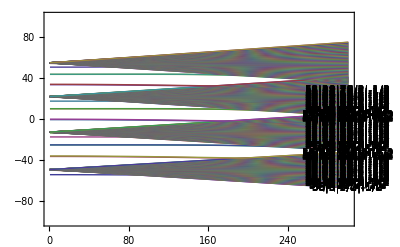

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

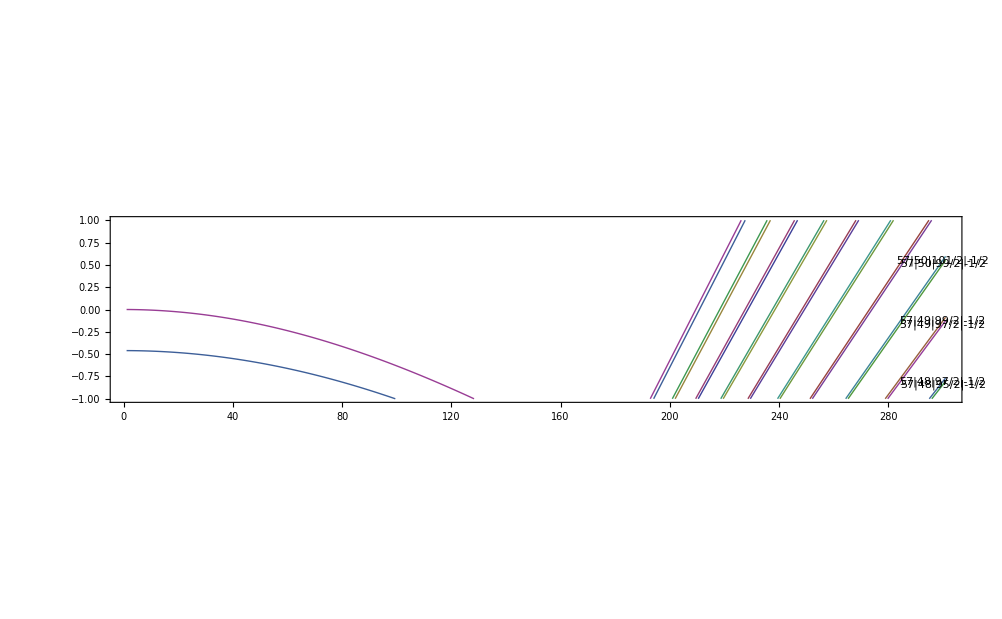

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[222]]

MPList[[222]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport


(*
Export["Stark_Shifts_around_60s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60s.dat",Efieldlist]
*)
Export["60p_j3_2_mj-1_2_stark_Shift.dat",MPList[[222]]]
```

60|1|3/2|-1/2

{{1,-0.0000678712},{2,-0.000271479},{3,-0.000610803},{4,-0.00108581},{5,-0.00169646},{6,-0.0024427},{7,-0.00332445},{8,-0.00434163},{9,-0.00549414},{10,-0.00678189},{11,-0.00820474},{12,-0.00976258},{13,-0.0114552},{14,-0.0132826},{15,-0.0152444},{16,-0.0173406},{17,-0.0195709},{18,-0.0219351},{19,-0.024433},{20,-0.0270644},{21,-0.0298291},{22,-0.0327267},{23,-0.035757},{24,-0.0389198},{25,-0.0422147},{26,-0.0456415},{27,-0.0491998},{28,-0.0528893},{29,-0.0567098},{30,-0.0606607},{31,-0.0647419},{32,-0.0689529},{33,-0.0732933},{34,-0.0777628},{35,-0.082361},{36,-0.0870875},{37,-0.0919418},{38,-0.0969235},{39,-0.102032},{40,-0.107267},{41,-0.112629},{42,-0.118116},{43,-0.123728},{44,-0.129465},{45,-0.135326},{46,-0.141311},{47,-0.147419},{48,-0.153649},{49,-0.160002},{50,-0.166477},{51,-0.173072},{52,-0.179788},{53,-0.186625},{54,-0.19358},{55,-0.200655},{56,-0.207848},{57,-0.215158},{58,-0.222586},{59,-0.230131},{60,-0.237791},{61,-0.245567},{62,-0.253458},{63,-0.261463},{64,-0.269581},{65,-0.277813},{66,-0.286157},{67,-0.294612},{68,-0.303179},{69,-0.311856},{70,-0.320643},{71,-0.32954},{72,-0.338544},{73,-0.347657},{74,-0.356877},{75,-0.366204},{76,-0.375637},{77,-0.385175},{78,-0.394818},{79,-0.404565},{80,-0.414415},{81,-0.424368},{82,-0.434423},{83,-0.444579},{84,-0.454836},{85,-0.465194},{86,-0.47565},{87,-0.486206},{88,-0.496859},{89,-0.50761},{90,-0.518458},{91,-0.529402},{92,-0.540442},{93,-0.551576},{94,-0.562805},{95,-0.574127},{96,-0.585542},{97,-0.597049},{98,-0.608648},{99,-0.620337},{100,-0.632117},{101,-0.643987},{102,-0.655945},{103,-0.667992},{104,-0.680127},{105,-0.692349},{106,-0.704657},{107,-0.717051},{108,-0.72953},{109,-0.742094},{110,-0.754742},{111,-0.767473},{112,-0.780287},{113,-0.793183},{114,-0.80616},{115,-0.819218},{116,-0.832357},{117,-0.845575},{118,-0.858872},{119,-0.872248},{120,-0.885702},{121,-0.899232},{122,-0.91284},{123,-0.926523},{124,-0.940282},{125,-0.954116},{126,-0.968024},{127,-0.982006},{128,-0.99606},{129,-1.01019},{130,-1.02439},{131,-1.03866},{132,-1.053},{133,-1.06741},{134,-1.08189},{135,-1.09644},{136,-1.11105},{137,-1.12574},{138,-1.14049},{139,-1.15531},{140,-1.17019},{141,-1.18514},{142,-1.20015},{143,-1.21522},{144,-1.23036},{145,-1.24556},{146,-1.26082},{147,-1.27615},{148,-1.29153},{149,-1.30697},{150,-1.32246},{151,-1.33802},{152,-1.35363},{153,-1.36929},{154,-1.38501},{155,-1.40078},{156,-1.4166},{157,-1.43247},{158,-1.44839},{159,-1.46435},{160,-1.48036},{161,-1.49641},{162,-1.5125},{163,-1.52863},{164,-1.54479},{165,-1.56098},{166,-1.57719},{167,-1.59343},{168,-1.60967},{169,-1.62592},{170,-1.64217},{171,-1.65839},{172,-1.67456},{173,-1.69066},{174,-1.70664},{175,-1.72241},{176,-1.73781},{177,-1.7525},{178,-1.76548},{179,-1.77242},{180,-1.75287},{181,-1.7029},{182,-1.64593},{183,-1.58734},{184,-1.52814},{185,-1.46866},{186,-1.40901},{187,-1.34925},{188,-1.28943},{189,-1.22956},{190,-1.16966},{191,-1.10973},{192,-1.04978},{193,-0.989809},{194,-0.929831},{195,-0.869843},{196,-0.809847},{197,-0.749845},{198,-0.689837},{199,-0.629826},{200,-0.569812},{201,-0.509795},{202,-0.449776},{203,-0.389756},{204,-0.329734},{205,-0.269711},{206,-0.209688},{207,-0.149665},{208,-0.0896418},{209,-0.0296186},{210,0.0304043},{211,0.0904267},{212,0.150449},{213,0.21047},{214,0.27049},{215,0.330509},{216,0.390528},{217,0.450545},{218,0.510561},{219,0.570575},{220,0.630588},{221,0.6906},{222,0.750611},{223,0.810619},{224,0.870627},{225,0.930632},{226,0.990636},{227,1.05064},{228,1.11064},{229,1.17064},{230,1.23063},{231,1.29063},{232,1.35062},{233,1.41061},{234,1.4706},{235,1.53058},{236,1.59057},{237,1.65055},{238,1.71052},{239,1.7705},{240,1.83047},{241,1.89044},{242,1.95041},{243,2.01038},{244,2.07034},{245,2.1303},{246,2.19026},{247,2.25021},{248,2.31016},{249,2.37011},{250,2.43005},{251,2.48999},{252,2.54992},{253,2.60985},{254,2.66978},{255,2.72971},{256,2.78963},{257,2.84954},{258,2.90945},{259,2.96935},{260,3.02925},{261,3.08915},{262,3.14903},{263,3.20891},{264,3.26879},{265,3.32865},{266,3.38851},{267,3.44836},{268,3.50819},{269,3.56802},{270,3.62783},{271,3.68763},{272,3.74741},{273,3.80717},{274,3.8669},{275,3.9266},{276,3.98625},{277,4.04584},{278,4.1053},{279,4.16454},{280,4.22314},{281,4.27799},{282,4.27329},{283,4.29481},{284,4.27124},{285,4.21043},{286,4.14884},{287,4.0873},{288,4.02667},{289,4.06572},{290,4.12133},{291,4.17676},{292,4.23012},{293,4.26486},{294,4.26033},{295,4.25852},{296,4.20406},{297,4.14607},{298,4.08773},{299,4.03},{300,3.99695},{301,4.04712}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{«1»}

60p_j3_2_mj-1_2_stark_Shift.dat

## Old data

```mathematica
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

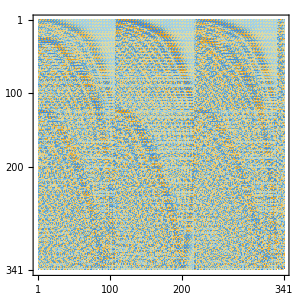

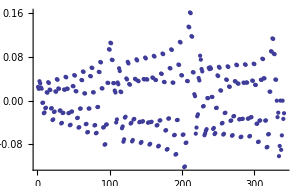

-0.0160281

-3.39745

{-72.2181,-66.8629,-62.1743,-61.9304,-61.0162,-60.796,-59.8912,-59.6823,-58.7823,-58.5808,-57.6836,-57.4878,-56.5921,-56.4014,-55.5061,-55.3205,-54.4245,-54.2442,-53.3464,-53.1721,-52.2711,-52.1037,-51.1979,-51.0385,-50.1264,-49.9762,-49.0562,-48.9161,-47.9868,-47.8576,-46.918,-46.8002,-45.8496,-45.7431,-44.7822,-44.6857,-43.7193,-43.6279,-42.7485,-42.5742,-42.468,-41.5433,-41.5007,-40.4774,-40.4383,-39.4051,-39.3725,-38.3302,-38.3041,-37.2535,-37.2332,-36.1751,-36.1599,-35.0955,-35.0842,-34.0149,-34.0059,-32.9342,-32.9248,-31.8536,-31.8414,-30.7739,-30.7565,-29.7012,-29.6709,-28.7635,-28.5863,-28.4451,-27.5145,-27.4773,-26.9365,-26.4001,-26.369,-25.5526,-25.5234,-25.3135,-25.2867,-24.3821,-24.3593,-24.2238,-24.2002,-23.2398,-23.2249,-23.1301,-23.1082,-22.1152,-22.107,-22.0299,-22.0086,-21.0046,-21.0014,-20.9218,-20.901,-19.904,-19.9026,-19.8082,-19.7879,-18.8094,-18.8054,-18.6929,-18.6723,-17.7163,-17.7094,-17.5775,-17.5556,-16.6232,-16.6135,-16.4626,-16.4385,-15.5298,-15.5173,-15.3482,-15.321,-14.4357,-14.4205,-14.2342,-14.203,-13.341,-13.3228,-13.1205,-13.0844,-12.2455,-12.2241,-12.0067,-11.9648,-11.1494,-11.1244,-10.8928,-10.8439,-10.0533,-10.0236,-9.77823,-9.72126,-8.958,-8.92151,-8.66275,-8.59616,-7.86658,-7.81817,-7.54566,-7.4678,-6.78973,-6.7136,-6.42593,-6.33655,-5.79359,-5.60798,-5.30168,-5.25631,-5.07862,-4.50187,-4.3888,-4.16823,-3.9819,-3.39745,-3.33767,-2.32451,-2.28271,-1.24121,-1.20881,-0.152056,-0.12512,0.94199,0.965646,2.04036,2.06207,3.14252,3.16317,4.24793,4.26811,5.35603,5.37615,6.46626,6.48662,7.40325,7.57815,7.59892,8.69106,8.71212,9.38115,9.79969,9.82872,9.86972,10.4722,10.9152,10.9447,11.0655,11.5098,12.0303,12.0585,12.236,12.5344,13.146,13.1704,13.3946,13.5811,14.2623,14.2818,14.5462,14.6583,15.3792,15.394,15.6931,15.7576,16.4968,16.5073,16.8365,16.8697,17.6149,17.6218,17.977,17.9887,18.7335,18.7374,19.1108,19.1154,19.852,19.8548,20.2346,20.2511,20.9697,20.9743,21.3583,21.3848,22.0875,22.0952,22.4813,22.5164,23.2055,23.2171,23.603,23.6458,24.3237,24.3401,24.7231,24.773,25.4418,25.4642,25.8414,25.8981,26.5592,26.5897,26.9582,27.0208,27.6753,27.7168,28.0737,28.1411,28.7888,28.8457,29.1889,29.2589,29.8981,29.9769,30.3055,30.3739,31.0009,31.1108,31.4263,31.4859,32.0949,32.2483,32.5557,32.5942,33.1784,33.391,33.6952,33.7037,34.2512,34.5422,34.7913,34.8831,35.3156,35.7133,36.3702,36.7745,37.396,37.8525,38.3745,38.9405,39.3197,40.0357,40.2888,41.1363,41.3108,42.2406,42.3731,43.3473,43.4588,44.4553,44.558,45.5635,45.665,46.6706,46.7771,47.7751,47.8926,48.8745,49.0103,49.9641,50.1297,51.0352,51.2503,52.0705,52.3718,53.0481,53.4936,53.9823,54.6157,54.9448,55.7374,55.9689,56.8581,57.0365,57.977,58.128,59.0922,59.2329,60.2003,60.3461,61.2942,61.4648,62.3583,62.5877,63.3624,63.7139,64.2934,64.8432,65.2335,65.9754,66.2538,67.1106,67.3352,68.2491,68.4506,69.3915,69.588,70.539,70.7458,71.6937,71.9352}

0.

```mathematica
(*Admixture of 60s1/2 at 500V/m*)
EField={0,0,500};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152,152]]
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152]]-Subscript[E, 12]/10^9
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]-Subscript[E, 12]/10^9
```

-Graphics-

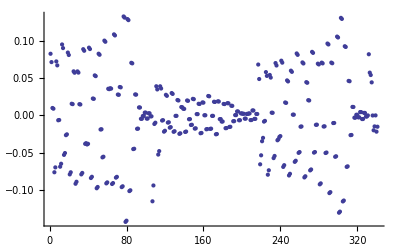

0.0478166

-13.5686

-7.79615

```mathematica
(*Admixture of 58d3/2 at 300V/m*)
EField={0,0,300};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114,114]]
EField={0,0,300};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
```

```mathematica
(*Export data for Origin*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=500;


E0=EMIN;
EStep=0.1;

TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={i,LabelList[[i]]} ]

Clear[i,k,L,MPList,R]
E0=EMIN;;
MPList={};
MPList=Join[MPList,{Join[{E0},Array[#&,Length[NList]]] }];
MPList=Join[MPList,{Join[{E0},LabelList] }];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;MPList=Join[MPList,{Join[{E0},Temp] }] ] 
Export[FileNameJoin[{Directory[],"Starkshift3.dat"}],MPList]
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkshift3.dat

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```